## Beyond reflexivity: Models

### Import packages

```mathematica
SetDirectory@NotebookDirectory[];
<<MaTeX`
<<QuiverGaugeTheory`
<<InterfaceM2`
```

## General Functions

```mathematica
ExportEPS[n_,x_]:=Export[n,StringReplace[ExportString[x,"EPS"],"3.25 M"->"25.0 M"],"Text"];
```

```mathematica
replaceTeXKeys=StringReplace[{
"\\mathbb{C}"->"ℂ",
"\\mathbb{Z}"->"ℤ",
"\\text{PdP}"->"PdP",
"\\text{dP}"->"dP",
"\\mathcal{C}"->"𝒞",
"\\text{SPP}"->"SPP",
"\\times":>"×",
"~"->""}]/*
StringReplace[{
x:(LetterCharacter..)~~"_"~~y:(DigitCharacter..):>
"\!\(\*SubscriptBox[\("<>x<>"\), \("<>y<>"\)]\)",x:(LetterCharacter..)~~"_{"~~y:(DigitCharacter..~~LetterCharacter..)~~"}":>
"\!\(\*SubscriptBox[\("<>x<>"\), \("<>StringReplace[y,z:(DigitCharacter..):>z<>"  "]<>"\)]\)",
x:(LetterCharacter..)~~"^"~~y:(DigitCharacter..):>
"\!\(\*SuperscriptBox[\("<>x<>"\), \("<>y<>"\)]\)",
x:(LetterCharacter..)~~"^{"~~y:(((DigitCharacter..)|",")..)~~"}":>
StringJoin["\!\(\*SuperscriptBox[\(",x, "\), \(", StringReplace[y,","->", "] , "\)]\)"]
}];
```

```mathematica
simplifyTag=StringReplace[{" ~("~~__~~EndOfString:>"","\\mathbb{Z}_":>"Z","\\mathbb{C}^3":>"C3","\\mathcal{C}":>"Conifold","/"|","|"{"|"}"|"\\times"|"\\text"|"("|")"|"^"|"_"->""}];
```

## Generate toric phases

### Import paper data (check typos)

```mathematica
BaoEtAlpotentials=Import["Bao-etal-data.tsv"];
```

```mathematica
modelspaper=Association@Map[If[Length[#]==1,First@#,Association@Thread[StringInsert[CharacterRange[65,64+Length@#],"Phase",1]->#]]&]@Map[First]@GroupBy[BaoEtAlpotentials,First->ToExpression@*Rest];
modelspaper=Association@KeyValueMap[If[AssociationQ@#2,Splice@Thread[Thread[{#1,Keys@#2}]->Values@#2],#1->#2]&,ReplaceAll[NonCommutativeMultiply->CenterDot]/@modelspaper];
```

```mathematica
toricpaper=Select[modelspaper,ToricPotentialQ];
nontoricpaper=Select[Not@*ToricPotentialQ]@modelspaper;
```

```mathematica
KeySort[Join@@AssociationThread@@@Thread[Map[Row[Flatten[{#}],Spacer[1]]&,Map[replaceTeXKeys]/@{Keys@toricpaper,Keys@nontoricpaper},{2}]->{True,False}]]//KeyValueMap[List]//ReplaceAll[False->Style[False,Bold]];
Grid[Prepend[#,Style[#,Italic, Bold,15]&/@{"Toric phase", "Is toric (typo free) ?"}],Frame->All,Dividers->{{1->Thick,2->Thick,-1->Thick},{1->Thick,2->Thick,-1->Thick}}]&/@Partition[%,Ceiling[Length[%]/3],Ceiling[Length[%]/3],{1,1},{}]
```

{Toric phase | Is toric (typo free) ?
PdP_(4  d) (2) | True
PdP_(4  e) (3) | True
PdP_(4  f) (2) | True
PdP_(5  b) (2) | True
PdP_(5  c) (3) | True
PdP_(6  a) (2) | True
PdP_(6  b) (3) | True
PdP_(6  c) (3) | True
K^(2, 4, 1, 1) | True
K^(2, 4, 1, 2) | True
K^(2, 4, 1, 3) | True
K^(2, 5, 1, 1) | True
K^(2, 5, 1, 2) | True
K^(2, 5, 1, 3) | True
K^(2, 5, 1, 4) | True
K^(4, 3, 2, 2) | True
K^(4, 4, 2, 2) | True
K^(4, 4, 2, 4) | True
L^(2, 4, 1) | True
L^(2, 5, 1) | True
L^(3, 3, 1) | True
L^(3, 5, 2) | True
L^(5, 4, 1) | True
L^(5, 6, 1) | True
ℂ^3/(ℤ_2×ℤ_5) (1,0,1)(0,1,4) | True
ℂ^3/(ℤ_2×ℤ_6) (1,0,1)(1,0,5) | True
ℂ^3/ℤ_5 (1,2,2) | True
ℂ^3/ℤ_6 (1,1,4) | True
ℂ^3/ℤ_8 (1,3,4) | True
SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)PhaseA | True
SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)PhaseB | True
SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)PhaseC | False
SPP/ℤ_3 (1,0,0,2)PhaseA | True,Toric phase | Is toric (typo free) ?
SPP/ℤ_3 (1,0,0,2)PhaseB | True
SPP/ℤ_3 (1,0,0,2)PhaseC | True
SPP/ℤ_3 (1,0,0,2)PhaseD | False
dP_1/ℤ_2 (1,0,0,1)PhaseA | True
dP_1/ℤ_2 (1,0,0,1)PhaseB | True
dP_1/ℤ_2 (1,0,0,1)PhaseC | True
PdP_2/ℤ_2 (1,1,1,1)PhaseA | True
PdP_2/ℤ_2 (1,1,1,1)PhaseB | True
PdP_2/ℤ_2 (1,1,1,1)PhaseC | True
PdP_(4  c) (2)PhaseA | True
PdP_(4  c) (2)PhaseB | True
PdP_(4  c) (2)PhaseC | True
PdP_(4  c) (2)PhaseD | True
PdP_(4  c) (2)PhaseE | True
PdP_(4  c) (2)PhaseF | False
PdP_(4  c) (2)PhaseG | True
PdP_(4  c) (2)PhaseH | True
PdP_(4  c) (2)PhaseI | False
PdP_(4  c) (2)PhaseJ | True
PdP_(4  c) (2)PhaseK | False
PdP_(4  c) (2)PhaseL | False
PdP_(4  c) (2)PhaseM | True
L^(1, 3, 1)/ℤ_2 (1,0,0,1)PhaseA | True
L^(1, 3, 1)/ℤ_2 (1,0,0,1)PhaseB | True
L^(1, 3, 2)PhaseA | True
L^(1, 3, 2)PhaseB | True
L^(1, 4, 1)/ℤ_2 (1,0,0,1)PhaseA | True
L^(1, 4, 1)/ℤ_2 (1,0,0,1)PhaseB | False
L^(1, 5, 1)/ℤ_2 (1,0,0,1)PhaseA | True
L^(1, 5, 1)/ℤ_2 (1,0,0,1)PhaseB | True
L^(2, 3, 2)/ℤ_2 (1,0,0,1)PhaseA | True
L^(2, 3, 2)/ℤ_2 (1,0,0,1)PhaseB | True
L^(2, 3, 2)/ℤ_2 (1,0,0,1)PhaseC | True,Toric phase | Is toric (typo free) ?
L^(2, 3, 2)/ℤ_2 (1,0,0,1)PhaseD | True
L^(3, 3, 2)PhaseA | True
L^(3, 3, 2)PhaseB | False
X^(3, 1)PhaseA | True
X^(3, 1)PhaseB | True
X^(3, 1)PhaseC | False
X^(3, 1)PhaseD | False
X^(3, 1)PhaseE | True
X^(3, 1)PhaseF | False
X^(3, 1)PhaseG | True
X^(3, 1)PhaseH | True
X^(3, 1)PhaseI | True
X^(3, 1)PhaseJ | False
X^(3, 2)PhaseA | True
X^(3, 2)PhaseB | False
X^(3, 2)PhaseC | False
X^(3, 2)PhaseD | True
X^(3, 2)PhaseE | False
X^(3, 2)PhaseF | True
Y^(3, 0)PhaseA | True
Y^(3, 0)PhaseB | False
Y^(3, 0)PhaseC | False
𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)PhaseA | True
𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)PhaseB | True
𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)PhaseC | True
𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)PhaseD | True
𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)PhaseE | True
𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)PhaseF | False
𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)PhaseG | False
𝒞/ℤ_4 (0,1,2,1)PhaseA | True
𝒞/ℤ_4 (0,1,2,1)PhaseB | False
𝒞/ℤ_4 (0,1,2,1)PhaseC | False}

### Generate toric-Seiberg duals from a seed

```mathematica
phaseSeedBaoEtAl=KeyMap[First@*Flatten@*List]@KeySelect[MatchQ[_String|{_,"PhaseA"}]]@toricpaper;
```


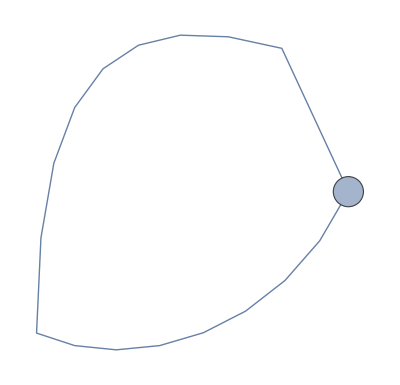
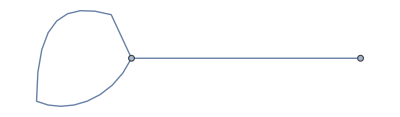
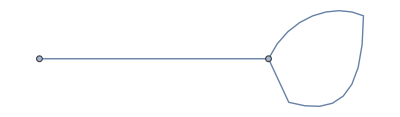
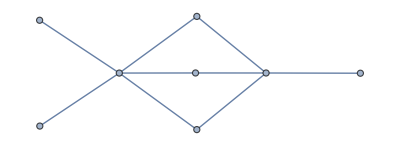
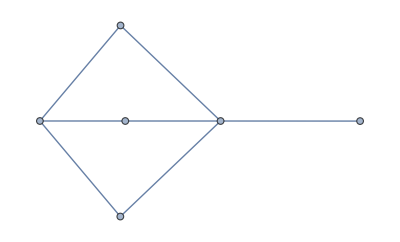


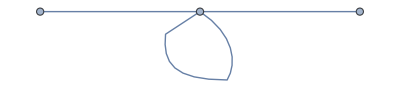
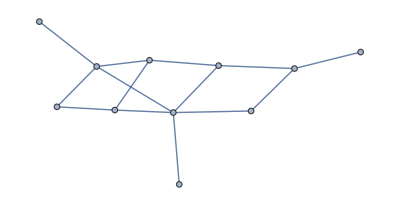

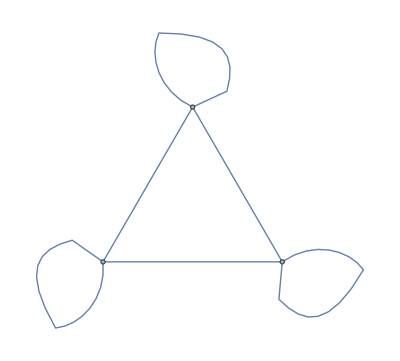
<|\mathbb{C}^3/\mathbb{Z}_6 ~(1,1,4)→-Graphics-,\mathbb{C}^3/\mathbb{Z}_5 ~(1,2,2)→-Graphics-,\mathbb{C}^3/\mathbb{Z}_8 ~(1,3,4)→-Graphics-,\mathbb{C}^3/(\mathbb{Z}_2\times\mathbb{Z}_5) ~(1,0,1)(0,1,4)→-Graphics-,\mathbb{C}^3/(\mathbb{Z}_2\times\mathbb{Z}_6) ~(1,0,1)(1,0,5)→-Graphics-,L^{3,3,1}→-Graphics-,L^{3,3,2}→-Graphics-,Y^{3,0}→-Graphics-,\text{SPP}/(\mathbb{Z}_2\times\mathbb{Z}_2) ~(1,0,0,1)(0,1,1,0)→-Graphics-,L^{2,3,2}/\mathbb{Z}_2 ~(1,0,0,1)→-Graphics-,\text{dP}_1/\mathbb{Z}_2 ~(1,0,0,1)→-Graphics-,L^{1,4,1}/\mathbb{Z}_2 ~(1,0,0,1)→-Graphics-,\text{PdP}_2/\mathbb{Z}_2 ~(1,1,1,1)→-Graphics-,L^{1,3,1}/\mathbb{Z}_2 ~(1,0,0,1)→-Graphics-,L^{3,5,2}→-Graphics-,L^{2,5,1}→-Graphics-,L^{5,6,1}→-Graphics-,L^{2,4,1}→-Graphics-,L^{5,4,1}→-Graphics-,L^{1,5,1}/\mathbb{Z}_2 ~(1,0,0,1)→-Graphics-,\text{SPP}/\mathbb{Z}_3 ~(1,0,0,2)→-Graphics-,\mathcal{C}/(\mathbb{Z}_3\times\mathbb{Z}_2) ~(1,0,0,2)(0,1,1,0)→-Graphics-,L^{1,3,2}→-Graphics-,\mathcal{C}/\mathbb{Z}_4 ~(0,1,2,1)→-Graphics-,X^{3,2}→-Graphics-,X^{3,1}→-Graphics-,\text{PdP}_{4c} ~(2)→-Graphics-,\text{PdP}_{4d} ~(2)→-Graphics-,\text{PdP}_{5b} ~(2)→-Graphics-,\text{PdP}_{6a} ~(2)→-Graphics-,K^{2,5,1,4}→-Graphics-,K^{2,5,1,3}→-Graphics-,K^{2,5,1,2}→-Graphics-,K^{2,5,1,1}→-Graphics-,K^{4,4,2,4}→-Graphics-,K^{4,4,2,2}→-Graphics-,K^{2,4,1,3}→-Graphics-,K^{2,4,1,2}→-Graphics-,K^{2,4,1,1}→-Graphics-,K^{4,3,2,2}→-Graphics-,\text{PdP}_{4e} ~(3)→-Graphics-,\text{PdP}_{5c} ~(3)→-Graphics-,\text{PdP}_{6b} ~(3)→-Graphics-,\text{PdP}_{4f} ~(2)→-Graphics-,\text{PdP}_{6c} ~(3)→-Graphics-|>

```mathematica
(*Takes some time*)
(*dualModels=Map[ToricSeibergDualsGraph,phaseSeedBaoEtAl]
Export["toric-phases-2-duality-graph.wl",dualModels];
```

```mathematica
(*sort phases by multiplicities of internal perfect matchings*)
sortedDualModels=Map[SortBy[{Length@FieldCases@#,Splice@Sort@Cases[Values@GroupBy[ToricDiagram@#,Identity,Last@*Keys],Subscript[(s|t), i_]]}&]@*VertexList,dualModels];
MapThread[Join[{#1},ReplaceAll[{CenterDot->NonCommutativeMultiply,Subscript[X, k_][i_,j_]:>XX[i,j,k]}]@Simplify@#2]&,{Keys@sortedDualModels,Values@sortedDualModels}]//StringDelete["\""]@StringReplace["XX"->"X"]@ExportString[#,"TSV"]&//Export["toric-phases-2.tsv", #,"Text"] &
```

toric-phases-2.tsv

### Organize models into a grid (gauge group factors vs. polytope vertices)

```mathematica
dualModels=Import["toric-phases-2-duality-graph.wl"];
sortedDualModels=GroupBy[Import["toric-phases-2.tsv"],First->ReplaceAll[NonCommutativeMultiply->CenterDot]@*ToExpression@*Rest,First];
```

```mathematica
modelsgrid=Map[
KeySort@GroupBy[#,First@*Map[Length]@*PolytopeVertices@*Values@*ToricDiagram@*First]&,
KeySort@GroupBy[sortedDualModels,Max@*ReplaceAll[Subscript[X,_]->Splice@*List]@*FieldCases@*First]
];
```

```mathematica
modelOrder=Map[Last]@Keys@AssociationFlatten@modelsgrid;
```

```mathematica
grid=Grid[
Join[Transpose[{Style[#,16,Bold]}&/@{"",Splice@Range[3,6]}],
Join[{Style[#,16,Bold]}&/@Range[5,12],
Table[Row@KeyValueMap[(Labeled[PolytopePlot[ToricDiagram@First@#2,ImageSize->{100,Automatic}],Style[replaceTeXKeys@#1,14],Left,RotateLabel->True]&)]@KeyTake[sortedDualModels,Lookup[modelsgrid[i],j,{},Keys]],{i,5,12},{j,3,6}],2]
],
Frame->All,ItemSize->{{Automatic,9,9*4,9*4,9*2},Automatic}
]
Export["grid-models-2.pdf",%]
```

| 3 | 4 | 5 | 6
5 | -Graphics-ℂ^3/ℤ_5 (1,2,2) |  |  | 
6 | -Graphics-ℂ^3/ℤ_6 (1,1,4) | -Graphics-L^(3, 3, 1)-Graphics-L^(3, 3, 2)-Graphics-Y^(3, 0)-Graphics-L^(2, 4, 1) |  | 
7 |  | -Graphics-L^(2, 5, 1)-Graphics-L^(1, 3, 2) | -Graphics-X^(3, 2)-Graphics-X^(3, 1)-Graphics-K^(2, 4, 1, 1) | 
8 | -Graphics-ℂ^3/ℤ_8 (1,3,4) | -Graphics-dP_1/ℤ_2 (1,0,0,1)-Graphics-L^(1, 3, 1)/ℤ_2 (1,0,0,1)-Graphics-L^(3, 5, 2)-Graphics-𝒞/ℤ_4 (0,1,2,1) | -Graphics-PdP_(4  c) (2)-Graphics-PdP_(4  d) (2)-Graphics-K^(2, 5, 1, 1)-Graphics-K^(2, 4, 1, 2) | -Graphics-PdP_(4  e) (3)-Graphics-PdP_(4  f) (2)
9 |  | -Graphics-L^(5, 4, 1)-Graphics-SPP/ℤ_3 (1,0,0,2) | -Graphics-PdP_(5  b) (2)-Graphics-K^(2, 5, 1, 2)-Graphics-K^(2, 4, 1, 3)-Graphics-K^(4, 3, 2, 2) | -Graphics-PdP_(5  c) (3)
10 | -Graphics-ℂ^3/(ℤ_2×ℤ_5) (1,0,1)(0,1,4) | -Graphics-L^(2, 3, 2)/ℤ_2 (1,0,0,1)-Graphics-L^(1, 4, 1)/ℤ_2 (1,0,0,1)-Graphics-PdP_2/ℤ_2 (1,1,1,1) | -Graphics-PdP_(6  a) (2)-Graphics-K^(2, 5, 1, 3)-Graphics-K^(4, 4, 2, 2) | -Graphics-PdP_(6  b) (3)-Graphics-PdP_(6  c) (3)
11 |  | -Graphics-L^(5, 6, 1) | -Graphics-K^(2, 5, 1, 4)-Graphics-K^(4, 4, 2, 4) | 
12 | -Graphics-ℂ^3/(ℤ_2×ℤ_6) (1,0,1)(1,0,5) | -Graphics-SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)-Graphics-L^(1, 5, 1)/ℤ_2 (1,0,0,1)-Graphics-𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0) |  |

grid-models-2.pdf

## Deformations (algorithm)

```mathematica
(*fuction that finds the redefinition*)
ClearAll[FindFieldRedefinition2]
FindFieldRedefinition2[w_?PotentialQ,param_:Automatic]:=
Module[{f,aa,vv,possParam,m,redefR0,s,nestF,nestS,redefR,ftermsSgn,sgnRule,sgnVars,sgnSol,solver},
f=FieldCases[w];
{aa,vv}={First[$RedefinitionVars],Rest[$RedefinitionVars]};
possParam=DeleteCases[Variables@Abelianize@w,Alternatives@@f];
m=Switch[{param,possParam},{Automatic,l_/;Length[l]==1},First[possParam],{Except[Automatic,(_Symbol)[__]|_Symbol],_},param,{_,l_/;Length[l]==1},First[possParam],_,Message[FindFieldRedefinition::paramerr];Return[$Failed]];
If[ToricPotentialQ@Expand@Simplify[m w],Return[{}]];
redefR0=FieldRedefinition[FieldCases[w],QuiverFromFields[w],2];
If[Length@redefR0==0,Message[FindFieldRedefinition::rdfnotavail];
Return[$Failed];];
If[Not@AllTrue[FTermsConstraint[(w/.redefR0),Expand@*Abs,List],Length[#]-Count[#,Abs[_Plus?(Not@*FreeQ[aa|vv])|_Times?(Not@*FreeQ[vv])],1]<=2&],Message[FindFieldRedefinition::rdfnotposs];
Return[$Failed];
];
sgnRule={Abs[s[__]]->1,Abs[HoldPattern[Times][r___,s[__],l___]]:>Abs[Times[l,r]]};
nestF[rule_]:=Block[{fterms,active,inactive,h,newR},
h=Abs@*HoldPattern[Times];
fterms=FTermsConstraint[Simplify[m (w/. rule)],Abs@*Factor,List]//.sgnRule;
active=Union@Join[
Cases[fterms,h[m^2,Subscript[aa,k1_][i1_,j1_],Subscript[aa,k2_][i2_,j2_]]:>Splice[{{i1,j1,k1},{i2,j2,k2}}],2],Cases[fterms,h[m,Subscript[aa,k1_][i1_,j1_]]:>{i1,j1,k1},2]
];
inactive=Union@Join[
Cases[fterms,x:h[(Subscript[aa,_][_,_])..]:>Splice[(List@@First@x)/.Subscript[_,k1_][i1_,j1_]:>{i1,j1,k1}],2],
Cases[fterms,Abs[(Subscript[aa,k1_][i1_,j1_])]:>{i1,j1,k1},2],
Cases[fterms,x:h[(Subscript[vv,_][_,_])..]:>Splice[(List@@First@x)/.Subscript[_,k1_][i1_,j1_]:>{i1,j1,k1}],2],
Cases[fterms,Abs[(Subscript[vv,k1_][i1_,j1_])]:>{i1,j1,k1},2]
];
newR=Join[Apply[Splice[{Subscript[aa,#3][#1,#2]->1,Subscript[vv,#3][#1,#2]->0}]&,inactive,{1}],Apply[Splice[{Subscript[aa,#3][#1,#2]->s[#1,#2,#3]/m,(Last@#->-Total@Most[#]&)@Union@Cases[redefR0,Subscript[aa|vv,#3][#1,#2],Infinity]}]&,active,{1}]];
MapAt[ReplaceRepeated[newR],rule,{All,2}]
];
nestS[rule_]:=Block[{fterms,h,solS},
h=Abs@*HoldPattern[Times];
fterms=FTermsConstraint[m (w/. rule),Simplify@*Abs@*Factor,List]//.sgnRule;
solS=First[
Solve[0==Flatten@Map[Cases[Abs@Alternatives[1+s[__],1-s[__],-1+s[__],-1-s[__]]],Expand@fterms]
],{}];
MapAt[ReplaceAll[solS],rule,{All,2}]
];
redefR=NestWhile[nestF,redefR0,UnsameQ,2];
redefR=NestWhile[nestS,redefR,UnsameQ,2];
If[ToricPotentialQ@Simplify[m w/. redefR],
Return@{DeleteCases[HoldPattern[Rule][x_,x_]]@redefR}
];
ftermsSgn=FTermsConstraint[Simplify[m w/. redefR],Simplify@*Abs,List];
sgnVars=Union@Cases[ftermsSgn,_s,Infinity];
sgnSol=Select[AssociationMap[{Map[Total,(ftermsSgn/. #)],FTermsConstraint[Simplify[m w/. redefR],Simplify]/. #}&,Thread[sgnVars->#]&/@Tuples[{1,-1},Length@sgnVars]],Not@*AnyTrue[True===Simplify[#>2]&]];
solver[eq_]:=ExpandAll[Normal@Solve[2==eq[[1]]&&0==eq[[2]]/.m->Zeta[3],Reals]/.{Zeta[3]->m}];
sgnSol=DeleteCases[{}]@Join[
Keys@Select[sgnSol,FreeQ[_Abs]],
KeyValueMap[Join@@Map[Append[Splice@#1],#2]&]@Map[solver,Select[sgnSol,Not@*FreeQ[_Abs]]]
];
redefR=DeleteCases[Map[MapAt[ReplaceRepeated[#],redefR,{All,2}]&,sgnSol],{___,HoldPattern[Rule][x_,-x_],___}];
redefR=DeleteCases[HoldPattern[Rule][x_,x_]]/@Select[DeleteCases[redefR,{___,HoldPattern[Rule][x_,-x_],___}],Not@PossibleZeroQ@Det@ReplaceAll[Untrace->1]@DG[Map[Last,#],{Map[First,#]}]&];
Collect[redefR,_?FieldProductQ|_?FieldQ,Expand]
];
```

```mathematica
(*fuction that find the deformations*)
ClearAll[findZZdefDetailed]
findZZdefDetailed[g_Integer,i_Integer,m:(_Integer|Automatic):Automatic,rng:({__Integer}|Automatic):Automatic]:=
Module[{compare,checkModels,defs,selZZ},
compare=modelsgrid[g,i+1];
checkModels[pot_]:=Block[{redef,ww,pos},
redef=Quiet@FindFieldRedefinition2@pot;
If[FailureQ@redef,Return[{}]];
ww=Simplify[μ pot/.First[redef,{}]];
pos=Position[
Map[IsomorphicQuiverQ[ww],compare,{2}],
True
];
If[Length@pos==1,Return@{pos,First[redef,{}]}];
pos=Keys@DeleteCases[{}]@AssociationMap[FindModelIsomorphism[ww,compare[[Sequence@@#]]]&,pos];
If[Length@pos==0,Return@{}];
{Keys@DeleteCases[{}]@AssociationMap[FindModelIsomorphism[ww,compare[[Sequence@@#]]]&,pos],First[redef,{}]}
];
selZZ[l_]:=DeleteCases[{0..}]@DeleteDuplicates[SortBy[Total]@Tuples[{0,1},{l}],#1+#2==Table[1,l]&];
defs[w_?ToricPotentialQ]:=
defs[w,GroupBy[ZigZagData[w],First->(Total[#[[4]]]&),KeyValueMap[List]]];
defs[w_?ToricPotentialQ,zzD_Association]:=
Block[{zzop=Map[Last]@zzD[{-1,0}],zz=Map[First]@zzD[{-1,0}]},
PrintTemporary@ReplaceAll[Key->Identity]@FirstPosition[modelsgrid[g,i],w];
KeyMap[{#,DeleteCases[# zz,0]}&]@DeleteCases[{}]@AssociationMap[
checkModels@*Expand@*IntegrateOutMassTerms@*((PrintTemporary[#];w+μ#.zzop)&),
selZZ[Length@zz]
]
];
Map[ReplaceAll[Key->Identity]]@MapIndexed[
{a,k}↦Splice@KeyValueMap[DirectedEdge[k/.Key->Identity,First[First@#2,{}]]->Append[#1,Last@#2]&,a],
Map[defs,(Switch[{m,rng},
{_Integer,{__Integer}},#[[{m},rng]],
{_Integer,Except[{__Integer}]},#[[{m}]],
_,#]&)@modelsgrid[g,i],{2}],{2}
]
];
```

```mathematica
(*defs74=findZZdefDetailed[7,4];
Export["Rank2/ZZdefs2-7-4.wl",%]*)
```

```mathematica
(*defs83=findZZdefDetailed[8,3];
Export["Rank2/ZZdefs2-8-3.wl",%]*)
```

```mathematica
(*defs84=findZZdefDetailed[8,4];
Export["Rank2/ZZdefs2-8-4.wl",%]*)
```

```mathematica
(*defs85=findZZdefDetailed[8,5];
Export["Rank2/ZZdefs2-8-5.wl",%]*)
```

```mathematica
(*defs94=findZZdefDetailed[9,4];
Export["Rank2/ZZdefs2-9-4.wl",%]*)
```

```mathematica
(*defs95=findZZdefDetailed[9,5];
Export["Rank2/ZZdefs2-9-5.wl",%]*)
```

```mathematica
(*defs103=findZZdefDetailed[10,3];
Export["Rank2/ZZdefs2-10-3.wl",%]*)
```

```mathematica
(*defs104=findZZdefDetailed[10,4];
Export["Rank2/ZZdefs2-10-4.wl",%]*)
```

```mathematica
(*defs105=findZZdefDetailed[10,5];
Export["Rank2/ZZdefs2-10-5.wl",%]*)
```

```mathematica
(*defs114=findZZdefDetailed[11,4];
Export["Rank2/ZZdefs2-11-4.wl",%]*)
```

```mathematica
(*defs123=findZZdefDetailed[12,3];
Export["Rank2/ZZdefs2-12-3.wl",%]*)
```

```mathematica
tags=Map["defs"<>#&,StringDelete[{"7-4","8-3","8-4","8-5","9-4","9-5","10-3","10-4","10-5","11-4","12-3"},"-"]];
{defs74,defs83,defs84,defs85,defs94,defs95,defs103,defs104,defs105,defs114,defs123}=Import/@Map["Rank2/ZZdefs2-"<>#<>".wl"&,{"7-4","8-3","8-4","8-5","9-4","9-5","10-3","10-4","10-5","11-4","12-3"}];
```

## Output

### Functions

```mathematica
FieldProductToTeX[w_?PotentialQ][fp_?FieldProductQ]:=FieldProductToTeX[fp,w];
FieldProductToTeX[fp_?FieldProductQ,w_?PotentialQ]:=
Module[{fields,rp},
fields=FieldCases[w];
rp=ReplaceAll[Subscript[X, k_][i_,j_]:>If[FreeQ[fields,Subscript[X, 2][i,j]],Subscript[X,Row[{i,j},If[AnyTrue[{i,j},#>9&],",",""]]],Subsuperscript[X,Row[{i,j},If[AnyTrue[{i,j},#>9&],",",""]],k]]];
StringRiffle[ToString[rp@#,TeXForm]&/@List@@fp]
]
```

```mathematica
PotentialToTeXLine[w_?PotentialQ]:=
Module[{rp,fields},
fields=FieldCases[w];
rp=ReplaceAll[Subscript[X, k_][i_,j_]:>If[FreeQ[fields,Subscript[X, 2][i,j]],Subscript[X,Row[{i,j},If[AnyTrue[{i,j},#>9&],",",""]]],Subsuperscript[X,Row[{i,j},If[AnyTrue[{i,j},#>9&],",",""]],k]]];
ToString[Expand@Simplify[w]//ReplaceAll[CenterDot->NonCommutativeMultiply]//rp,TeXForm]//StringReplace[{"\\text{**}"->" ",x:"+"|"-":>" "<>x<>" "}]
];
```

```mathematica
DeformationSectionSplit[defs_,tag_String]:=
Module[{start, end,rep,rifF,gps},
start="\\subsection{\\texorpdfstring{$XXXX$}{XXXX} to \\texorpdfstring{$YYYY$}{YYYY}}
\\label{sec:ZZZZ}\n
\\tabulinesep=1mm
\\begin{tabu}{@{\\hskip 0.1cm}l|l|l@{\\hskip 0.1cm}}
    $W_\\text{i}$  & Deformation zig-zags $\\eta$~~ & $W_\\text{f}$ \\\\
    \\hline\\hline";
end="\\end{tabu}";
rep={"~("->"\,(","PdP_"->"\\text{PdP}_","dP_"->"\\text{dP}_","SPP"->"\\text{SPP}"};
rifF=StringRiffle[#,{start<>"\n"," \\\\\n"," \\\\\n"<>end},{"        "," & ",""}]&;
gps=Map[
MapApply[
{wi,wf,eta}↦{
"$"<>wi[[1]]<>"$ ("<>RomanNumeral[wi[[2]]]<>")",
StringRiffle[FieldProductToTeX[#,sortedDualModels[[Sequence@@MapAt[Key,wi,{1}]]]]&/@eta,{"$","$, $","$"}],
"$"<>wf[[1]]<>"$ ("<>RomanNumeral[wf[[2]]]<>")"}
],
GroupBy[Map[Apply[{First@#1,Last@#1,#2[[2]]}&],Join@@Values@defs],#[[{1,2},1]]&,SortBy[{Length@#[[3]],#}&]]
];
StringRiffle[MapIndexed[
StringReplace[#1,{tag->tag<>"-"<>ToString@First[#2],Splice@rep}]&,
KeyValueMap[StringReplace[StringReplace[" ~("~~Shortest[__]~~")$"->"$"]@rifF@#2,{"XXXX"->First[#1],"YYYY"->Last[#1],"ZZZZ"->tag}]&,gps]
],"\n\n"]
]
```

### Toric phases LaTeX

```mathematica
StringRiffle[KeyValueMap[
StringRiffle[{
"\\subsection{\\texorpdfstring{$"<>#1<>"$}{"<>#1<>"}}",
"\\begin{enumerate}[(I)]",
#2,
"\\end{enumerate}"},"\n"]&,
Map[StringRiffle[Map[x↦"    \\item $"<>PotentialToTeXLine[x]<>"$"]@#,"\n"]&,KeyTake[modelOrder]@sortedDualModels]
],"\n\n"];
```

### Polytopes

```mathematica
KeyValueMap[ExportEPS["latex/figures/"<>simplifyTag[#1]<>"-td2.eps",
PolytopePlot[ToricDiagram[#2],
"PolytopeCellStyle"->{
"ExtremalPoints"->Directive[EdgeForm[{Thickness[0.015],Black}],FaceForm[Black]],
"NonExtremalPoints"->Directive[EdgeForm[{Thickness[0.010],Black}],FaceForm[Yellow]],
"InternalPoints"->Directive[EdgeForm[{Thickness[0.010],Black}],FaceForm[{Lighter[Red,0.6]}]]
},
"PolytopeCellFunction"->{
"ExtremalPoints"->(Disk[#1,0.12]&),
"NonExtremalPoints"->(Disk[#1,0.1]&),
"InternalPoints"->(Disk[#1,0.1]&)},
GridLines->{{-2,2},{-3,4}}
	]]&,
(Map[First]@sortedDualModels)
];
```

### Deformations tables

```mathematica
tags=StringSplit["defs74,defs83,defs84,defs85,defs94,defs95,defs103,defs104,defs105,defs114,defs123",","];
```

```mathematica
StringRiffle[Map[DeformationSectionSplit[ToExpression@#,#]&,tags],"\n\n"];
```

## Deformations

### L^(2,5,1) Phase A → L^(2,5,1) Phase A (reversal is the same)

```mathematica
ZigZagData[modelsgrid[7,4][[1,1]]]
```

<|X_1[2,3]·X_2[3,4]·X_1[4,6]·X_1[6,7]·X_1[7,1]·X_2[1,2]→{{0,-1},6,3,{-(X_1[2,7]·X_1[7,4]·X_1[4,2]),X_1[1,6]·X_1[6,5]·X_1[5,3]·X_1[3,1]},2.09689},X_1[1,2]·X_2[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,7]·X_2[7,1]→{{0,-1},6,3,{-(X_1[1,6]·X_1[6,5]·X_1[5,3]·X_1[3,1]),X_1[2,7]·X_1[7,4]·X_1[4,2]},2.09689},X_1[1,6]·X_1[6,7]·X_1[7,4]·X_1[4,5]·X_1[5,3]·X_2[3,4]·X_1[4,2]·X_2[2,3]·X_1[3,1]·X_2[1,2]·X_1[2,7]·X_2[7,1]→{{3,1},12,6,{X_1[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,6]·X_1[6,5]·X_1[5,7]·X_1[7,1],-(X_1[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,6]·X_1[6,5]·X_1[5,7]·X_1[7,1])},4.24863},X_1[1,2]·X_1[2,7]·X_1[7,1]·X_1[1,6]·X_1[6,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]·X_1[2,3]·X_1[3,1]→{{-2,1},10,5,{X_1[4,6]·X_1[6,7]·X_2[7,1]·X_2[1,2]·X_2[2,3]·X_2[3,4],-(X_1[4,5]·X_1[5,7]·X_2[7,1]·X_2[1,2]·X_2[2,3]·X_2[3,4])},3.67276},X_1[4,6]·X_1[6,5]·X_1[5,7]·X_1[7,4]→{{-1,0},4,2,{X_1[4,5]·X_1[5,3]·X_2[3,4],-(X_1[1,6]·X_1[6,7]·X_2[7,1])},1.88483}|>

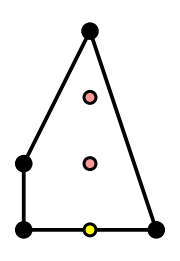

```mathematica
ZigZagDeformation[modelsgrid[7,4][[1,1]],Subscript[X, 1][4,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,7]·Subscript[X, 1][7,4]]//IntegrateOutMassTerms//ToricDiagram//PolytopePlot
```

### L^(1,3,2) Phase A → K^(2,4,1,1) Phase A

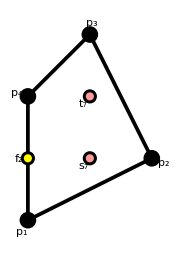
-Graphics- | {1,-2} | 10 | 5 | {X_1[1,5]·X_1[5,2]·X_1[2,4]·X_1[4,3]·X_1[3,6]·X_1[6,7]·X_1[7,1],-(X_1[1,5]·X_1[5,2]·X_1[2,4]·X_1[4,3]·X_1[3,6]·X_1[6,7]·X_1[7,1])} | 3.9296
 | {2,1} | 10 | 5 | {-(X_1[2,6]·X_1[6,7]·X_1[7,5]·X_1[5,4]·X_1[4,3]·X_1[3,1]·X_2[1,2]),X_1[2,6]·X_1[6,7]·X_1[7,5]·X_1[5,4]·X_1[4,3]·X_1[3,1]·X_2[1,2]} | 3.85425
 | {-1,1} | 6 | 3 | {-(X_1[1,2]·X_1[2,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]),X_1[1,2]·X_1[2,6]·X_1[6,5]·X_1[5,4]·X_1[4,1]} | 2.87139
 | {-1,0} | 4 | 2 | {X_1[1,2]·X_1[2,7]·X_1[7,1],-(X_1[3,6]·X_1[6,5]·X_1[5,3])} | 1.67238
 | {-1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,4]·X_1[4,1]),X_1[3,6]·X_1[6,5]·X_1[5,3]} | 1.67238

```mathematica
WL132PhaseA=modelsgrid[7,4][[2,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WL132PhaseAzz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

```mathematica
WL132PhaseADef1=WL132PhaseA+{0,μ}. WL132PhaseAzz[{-1,0}];
```

```mathematica
RedefChoice1={Subscript[β, 1][4,1]->1/μ,Subscript[α, 1][4,1]->-1/μ,Subscript[α, 1][2,7]->1/μ,Subscript[α, 1][5,3]->-1/μ,Subscript[α, 1][6,5]->1/μ,Subscript[γ, 1][1,2]->0,Subscript[β, 1][1,2]->-1/μ,Subscript[β, 1][2,7]->-1/μ,Subscript[α, 1][1,2]->1/μ,Subscript[β, 1][5,3]->1/μ,Subscript[β, 1][6,5]->-1/μ};
RedefRules1=FieldRedefinition[{Subscript[X, 1][1,2],Subscript[X, 1][2,7],Subscript[X, 1][4,1],Subscript[X, 1][5,3],Subscript[X, 1][6,5]},QuiverFromFields[WL132PhaseADef1],2]//.RedefChoice1;
RedefRules1Mass={Subscript[X, 1][4,1]->μ Subscript[X, 1][4,1],Subscript[X, 1][4,3]->μ Subscript[X, 1][4,3],Subscript[X, 1][5,2]->μ Subscript[X, 1][5,2],Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][7,1]->μ Subscript[X, 1][7,1]};
RedefRules1//Column
```

X_1[1,2]→X_1[1,2]/μ-X_2[1,2]/μ
X_1[2,7]→-(X_1[2,6]·X_1[6,7])/μ+X_1[2,7]/μ
X_1[4,1]→(X_1[4,3]·X_1[3,1])/μ-X_1[4,1]/μ
X_1[5,3]→(X_1[5,4]·X_1[4,3])/μ-X_1[5,3]/μ
X_1[6,5]→-(X_1[6,7]·X_1[7,5])/μ+X_1[6,5]/μ

```mathematica
WL132PhaseADef1Final=WL132PhaseADef1/.Echo@First@FindFieldRedefinition[WL132PhaseADef1,μ]//Simplify;
```

{X_1[1,2]→X_1[1,2]/μ-X_2[1,2]/μ,X_1[2,7]→-(X_1[2,6]·X_1[6,7])/μ+X_1[2,7]/μ,X_1[4,1]→(X_1[4,3]·X_1[3,1])/μ-X_1[4,1]/μ,X_1[5,3]→(X_1[5,4]·X_1[4,3])/μ-X_1[5,3]/μ,X_1[6,5]→-(X_1[6,7]·X_1[7,5])/μ+X_1[6,5]/μ}

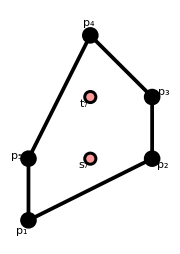
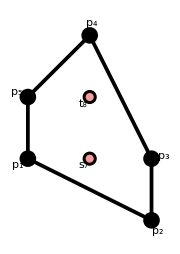
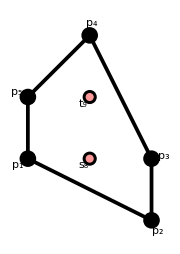
{{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"]&,{{WL132PhaseA},{WL132PhaseADef1Final},modelsgrid[7,5][[3]]},{2}]
```

```mathematica
WL132PhaseADef2=WL132PhaseA+{μ,0}. WL132PhaseAzz[{-1,0}];
```

```mathematica
WL132PhaseADef2Final=Simplify[μ WL132PhaseADef2/.Echo@First@FindFieldRedefinition[WL132PhaseADef2,μ]];
```

{X_1[1,2]→X_1[1,2]/μ-X_2[1,2]/μ,X_1[2,7]→(X_1[2,6]·X_1[6,7])/μ-X_1[2,7]/μ,X_1[4,1]→-(X_1[4,3]·X_1[3,1])/μ+X_1[4,1]/μ,X_1[5,3]→-(X_1[5,4]·X_1[4,3])/μ+X_1[5,3]/μ,X_1[6,5]→(X_1[6,7]·X_1[7,5])/μ-X_1[6,5]/μ}

<|X^(3, 2)→{False,False,False},X^(3, 1)→{False,False,False,False,False},K^(2, 4, 1, 1)→{True,False,False}|>

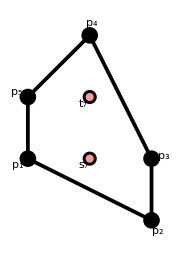
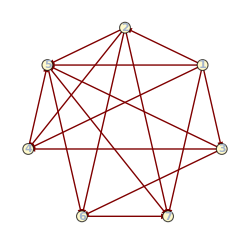
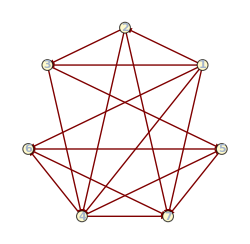
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[Simplify@WL132PhaseADef2Final,#]&,modelsgrid[7,5],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL132PhaseADef2Final,Splice@Extract[modelsgrid[7,5],Position[%,True]]}
]
```

### ℂ^3/ℤ_8 (1,3,4) → 𝒞/ℤ_4 (0,1,2,1) Phase B

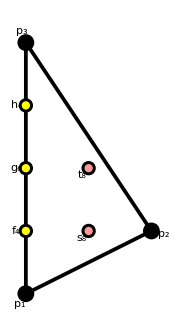
-Graphics- | {1,-2} | 16 | 8 | {-(X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,8]·X_1[8,2]·X_1[2,5]·X_1[5,7]·X_1[7,1]),X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,8]·X_1[8,2]·X_1[2,5]·X_1[5,7]·X_1[7,1]} | 5.33333
 | {3,2} | 16 | 8 | {X_1[1,6]·X_1[6,5]·X_1[5,3]·X_1[3,8]·X_1[8,7]·X_1[7,4]·X_1[4,2]·X_1[2,1],-(X_1[1,6]·X_1[6,5]·X_1[5,3]·X_1[3,8]·X_1[8,7]·X_1[7,4]·X_1[4,2]·X_1[2,1])} | 5.33333
 | {-1,0} | 4 | 2 | {X_1[1,8]·X_1[8,1],-(X_1[6,7]·X_1[7,6])} | 1.33333
 | {-1,0} | 4 | 2 | {-(X_1[4,5]·X_1[5,4]),X_1[6,7]·X_1[7,6]} | 1.33333
 | {-1,0} | 4 | 2 | {-(X_1[2,3]·X_1[3,2]),X_1[4,5]·X_1[5,4]} | 1.33333
 | {-1,0} | 4 | 2 | {-(X_1[1,8]·X_1[8,1]),X_1[2,3]·X_1[3,2]} | 1.33333

```mathematica
WC3Z8=modelsgrid[8,3][[1,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WC3Z8zz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

```mathematica
WC3Z8Def1=WC3Z8+{μ,0,μ,0}.WC3Z8zz[{-1,0}]//Simplify;
```

```mathematica
WC3Z8Def1Final=μ WC3Z8Def1//IntegrateOutMassTerms//Simplify;
```

<|dP_1/ℤ_2 (1,0,0,1)→{False,False,False},L^(1, 3, 1)/ℤ_2 (1,0,0,1)→{False,False},L^(3, 5, 2)→{False,False},𝒞/ℤ_4 (0,1,2,1)→{False,True,False,False}|>

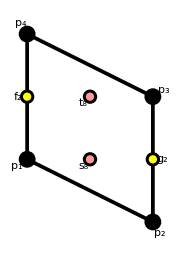
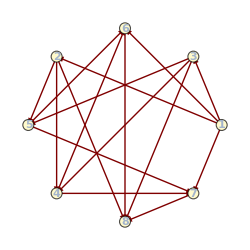
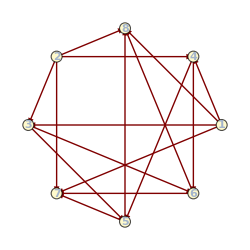
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[Simplify@WC3Z8Def1Final,#]&,modelsgrid[8,4],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z8Def1Final,Splice@Extract[modelsgrid[8,4],Position[%,True]]}
]
```

### ℂ^3/ℤ_8 (1,3,4) → L^(1,3,1)/ℤ_2 (1,0,0,1) Phase A

```mathematica
WC3Z8=modelsgrid[8,3][[1,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WC3Z8zz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

-Graphics- | {1,-2} | 16 | 8 | {-(X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,8]·X_1[8,2]·X_1[2,5]·X_1[5,7]·X_1[7,1]),X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,8]·X_1[8,2]·X_1[2,5]·X_1[5,7]·X_1[7,1]} | 5.33333
 | {3,2} | 16 | 8 | {X_1[1,6]·X_1[6,5]·X_1[5,3]·X_1[3,8]·X_1[8,7]·X_1[7,4]·X_1[4,2]·X_1[2,1],-(X_1[1,6]·X_1[6,5]·X_1[5,3]·X_1[3,8]·X_1[8,7]·X_1[7,4]·X_1[4,2]·X_1[2,1])} | 5.33333
 | {-1,0} | 4 | 2 | {X_1[1,8]·X_1[8,1],-(X_1[6,7]·X_1[7,6])} | 1.33333
 | {-1,0} | 4 | 2 | {-(X_1[4,5]·X_1[5,4]),X_1[6,7]·X_1[7,6]} | 1.33333
 | {-1,0} | 4 | 2 | {-(X_1[2,3]·X_1[3,2]),X_1[4,5]·X_1[5,4]} | 1.33333
 | {-1,0} | 4 | 2 | {-(X_1[1,8]·X_1[8,1]),X_1[2,3]·X_1[3,2]} | 1.33333

```mathematica
WC3Z8Def2=WC3Z8+{μ,0,0,0}.WC3Z8zz[{-1,0}]//Simplify;
```

```mathematica
WC3Z8Def2Min=WC3Z8Def2//IntegrateOutMassTerms//Simplify//Expand;
```

```mathematica
WC3Z8Def2Final=μ WC3Z8Def2Min/.First@FindFieldRedefinition[WC3Z8Def2Min,μ]//Simplify;
```

<|dP_1/ℤ_2 (1,0,0,1)→{False,False,False},L^(1, 3, 1)/ℤ_2 (1,0,0,1)→{True,False},L^(3, 5, 2)→{False,False},𝒞/ℤ_4 (0,1,2,1)→{False,False,False,False}|>

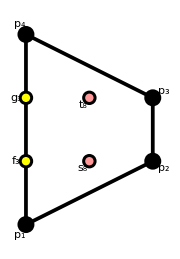
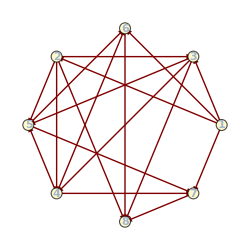
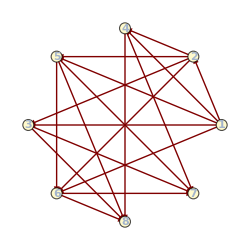
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[WC3Z8Def2Final,#]&,modelsgrid[8,4],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z8Def2Final,modelsgrid[8,4][[2,1]]}
]
```

### ℂ^3/ℤ_8 (1,3,4) → 𝒞/ℤ_4 (0,1,2,1) Phase A

```mathematica
WC3Z8=modelsgrid[8,3][[1,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WC3Z8zz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

-Graphics- | {1,-2} | 16 | 8 | {-(X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,8]·X_1[8,2]·X_1[2,5]·X_1[5,7]·X_1[7,1]),X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,8]·X_1[8,2]·X_1[2,5]·X_1[5,7]·X_1[7,1]} | 5.33333
 | {3,2} | 16 | 8 | {X_1[1,6]·X_1[6,5]·X_1[5,3]·X_1[3,8]·X_1[8,7]·X_1[7,4]·X_1[4,2]·X_1[2,1],-(X_1[1,6]·X_1[6,5]·X_1[5,3]·X_1[3,8]·X_1[8,7]·X_1[7,4]·X_1[4,2]·X_1[2,1])} | 5.33333
 | {-1,0} | 4 | 2 | {X_1[1,8]·X_1[8,1],-(X_1[6,7]·X_1[7,6])} | 1.33333
 | {-1,0} | 4 | 2 | {-(X_1[4,5]·X_1[5,4]),X_1[6,7]·X_1[7,6]} | 1.33333
 | {-1,0} | 4 | 2 | {-(X_1[2,3]·X_1[3,2]),X_1[4,5]·X_1[5,4]} | 1.33333
 | {-1,0} | 4 | 2 | {-(X_1[1,8]·X_1[8,1]),X_1[2,3]·X_1[3,2]} | 1.33333

```mathematica
WC3Z8Def3=WC3Z8+{μ,μ,0,0}.WC3Z8zz[{-1,0}]//Simplify;
```

```mathematica
WC3Z8Def3Min=WC3Z8Def3//IntegrateOutMassTerms//Simplify//Expand;
```

```mathematica
WC3Z8Def3Final=μ WC3Z8Def3Min/.First@Echo@FindFieldRedefinition[WC3Z8Def3Min,μ]//Simplify;
```

{{X_1[2,3]→X_1[2,1]·X_1[1,3] (-1/μ-β_1[2,3])+X_1[2,5]·X_1[5,3] β_1[2,3]+X_1[2,3]/μ,X_1[3,2]→X_1[3,4]·X_1[4,2] (-1/μ-β_1[2,3])+X_1[3,8]·X_1[8,2] β_1[2,3]+X_1[3,2]/μ,X_1[6,7]→X_1[6,5]·X_1[5,7] (1/μ-β_1[6,7])+X_1[6,8]·X_1[8,7] β_1[6,7]-X_1[6,7]/μ,X_1[7,6]→X_1[7,1]·X_1[1,6] (1/μ-β_1[6,7])+X_1[7,4]·X_1[4,6] β_1[6,7]-X_1[7,6]/μ}}

<|dP_1/ℤ_2 (1,0,0,1)→{False,False,False},L^(1, 3, 1)/ℤ_2 (1,0,0,1)→{False,False},L^(3, 5, 2)→{False,False},𝒞/ℤ_4 (0,1,2,1)→{True,False,False,False}|>

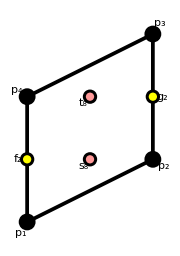
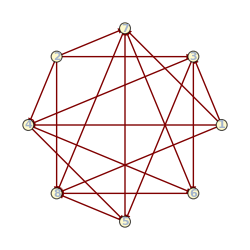
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[WC3Z8Def3Final,#]&,modelsgrid[8,4],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z8Def2Final,Splice@Extract[modelsgrid[8,4],Position[%,True]]}
]
```

### dP_1/ℤ_2 (1,0,0,1) Phase A → K^(2,5,1,1) Phase A

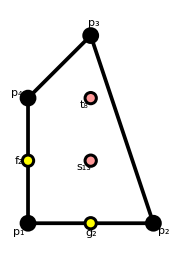
-Graphics- | {0,-1} | 6 | 3 | {-(X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,7]·X_1[7,1]),X_1[3,5]·X_1[5,8]·X_1[8,3]} | 2.26297
 | {0,-1} | 6 | 3 | {X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,7]·X_1[7,1],-(X_1[3,5]·X_1[5,8]·X_1[8,3])} | 2.26297
 | {3,1} | 12 | 6 | {X_1[1,2]·X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,5]·X_2[5,4]·X_2[4,3]·X_1[3,1],-(X_1[1,2]·X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,5]·X_2[5,4]·X_2[4,3]·X_1[3,1])} | 4.52593
 | {-1,1} | 8 | 4 | {-(X_1[1,8]·X_1[8,6]·X_1[6,5]·X_1[5,4]·X_1[4,3]·X_1[3,1]),X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,4]·X_1[4,3]·X_1[3,2]} | 3.47407
 | {-1,0} | 4 | 2 | {X_1[4,6]·X_1[6,5]·X_1[5,4],-(X_1[1,8]·X_1[8,7]·X_1[7,1])} | 1.73703
 | {-1,0} | 4 | 2 | {X_1[1,8]·X_1[8,7]·X_1[7,1],-(X_1[2,4]·X_1[4,3]·X_1[3,2])} | 1.73703

```mathematica
WdP1Z2PhaseA=modelsgrid[8,4][[1,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WdP1Z2PhaseAzz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

```mathematica
WdP1Z2PhaseADef1=WdP1Z2PhaseA+{μ,0}.WdP1Z2PhaseAzz[{-1,0}];
```

```mathematica
WdP1Z2PhaseADef1Final=(μ WdP1Z2PhaseADef1/.First@Echo@FindFieldRedefinition[WdP1Z2PhaseADef1,μ])//Simplify
```

{{X_1[1,8]→-(X_1[1,2]·X_1[2,8])/μ+X_1[1,8]/μ,X_1[3,2]→-(X_1[3,1]·X_1[1,2])/μ+X_1[3,2]/μ,X_1[4,3]→X_1[4,3]/μ-X_2[4,3]/μ,X_1[5,4]→X_1[5,4]/μ-X_2[5,4]/μ,X_1[6,5]→(X_1[6,7]·X_1[7,5])/μ-X_1[6,5]/μ,X_1[8,7]→(X_1[8,6]·X_1[6,7])/μ-X_1[8,7]/μ}}

-(X_1[1,8]·X_1[8,3]·X_1[3,1])+X_1[1,8]·X_1[8,7]·X_1[7,1]-X_1[2,4]·X_2[4,3]·X_1[3,2]+X_1[2,8]·X_1[8,3]·X_1[3,2]+X_1[3,5]·X_1[5,4]·X_2[4,3]-X_1[3,5]·X_2[5,4]·X_1[4,3]-X_1[4,6]·X_1[6,5]·X_1[5,4]+X_1[5,8]·X_1[8,6]·X_1[6,5]-X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[1,2]·X_1[2,4]·X_1[4,3]·X_1[3,1]+X_1[4,6]·X_1[6,7]·X_1[7,5]·X_2[5,4]-X_1[1,2]·X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,1]

<|PdP_(4  c) (2)→{False,False,False,False,False,False,False,False},PdP_(4  d) (2)→{False,False,False,False,False,False,False,False},K^(2, 5, 1, 1)→{True,False,False,False},K^(2, 4, 1, 2)→{False,False,False,False,False,False,False}|>

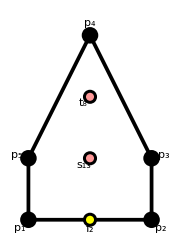
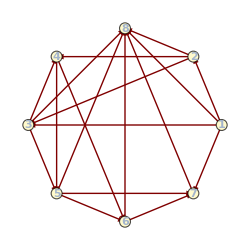
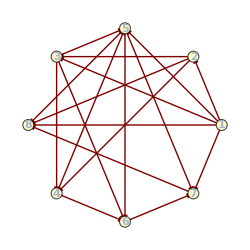
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[WdP1Z2PhaseADef1Final,#]&,modelsgrid[8,5],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WdP1Z2PhaseADef1Final,Splice@Extract[modelsgrid[8,5],Position[%,True]]}
]
```

### L^(1,3,1)/ℤ_2 (1,0,0,1) Phase A → Marginal of 𝒞/ℤ_4 (0,1,2,1)

```mathematica
WL131Z2PhaseA=modelsgrid[8,4][[2,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WL131Z2PhaseAzz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

-Graphics- | {1,-2} | 12 | 6 | {X_1[1,4]·X_1[4,7]·X_1[7,5]·X_1[5,2]·X_1[2,3]·X_1[3,8]·X_1[8,6]·X_1[6,1],-(X_1[1,4]·X_1[4,7]·X_1[7,5]·X_1[5,2]·X_1[2,3]·X_1[3,8]·X_1[8,6]·X_1[6,1])} | 4.4305
 | {1,0} | 4 | 2 | {X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1],-(X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5])} | 2.4305
 | {1,2} | 12 | 6 | {-(X_1[1,5]·X_1[5,8]·X_1[8,4]·X_1[4,2]·X_1[2,6]·X_1[6,7]·X_1[7,3]·X_1[3,1]),X_1[1,5]·X_1[5,8]·X_1[8,4]·X_1[4,2]·X_1[2,6]·X_1[6,7]·X_1[7,3]·X_1[3,1]} | 4.4305
 | {-1,0} | 4 | 2 | {X_1[1,2]·X_1[2,1],-(X_1[5,6]·X_1[6,5])} | 1.5695
 | {-1,0} | 4 | 2 | {X_1[5,6]·X_1[6,5],-(X_1[3,8]·X_1[8,4]·X_1[4,7]·X_1[7,3])} | 1.5695
 | {-1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,1]),X_1[3,8]·X_1[8,4]·X_1[4,7]·X_1[7,3]} | 1.5695

```mathematica
WL131Z2PhaseADef1=WL131Z2PhaseA+{μ,0,0}.WL131Z2PhaseAzz[{-1,0}]//IntegrateOutMassTerms//Expand;
```

### L^(3,5,2) Phase A → K^(2,4,1,2) Phase B

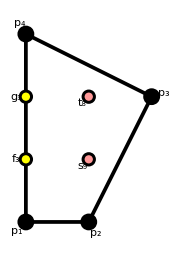
-Graphics- | {0,-1} | 6 | 3 | {X_1[1,2]·X_1[2,4]·X_1[4,7]·X_1[7,6]·X_1[6,1],-(X_1[1,3]·X_1[3,5]·X_1[5,7]·X_1[7,8]·X_1[8,1])} | 2.95626
 | {2,-1} | 10 | 5 | {X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,7]·X_1[7,8]·X_1[8,6]·X_1[6,1],-(X_1[1,3]·X_1[3,2]·X_1[2,4]·X_1[4,7]·X_1[7,8]·X_1[8,6]·X_1[6,1])} | 3.97025
 | {1,2} | 12 | 6 | {-(X_1[1,7]·X_1[7,3]·X_1[3,2]·X_1[2,8]·X_1[8,6]·X_1[6,5]·X_1[5,4]·X_1[4,1]),X_1[1,7]·X_1[7,3]·X_1[3,2]·X_1[2,8]·X_1[8,6]·X_1[6,5]·X_1[5,4]·X_1[4,1]} | 4.59447
 | {-1,0} | 4 | 2 | {X_1[1,2]·X_1[2,8]·X_1[8,1],-(X_1[5,7]·X_1[7,6]·X_1[6,5])} | 1.49301
 | {-1,0} | 4 | 2 | {-(X_1[3,4]·X_1[4,3]),X_1[5,7]·X_1[7,6]·X_1[6,5]} | 1.49301
 | {-1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,8]·X_1[8,1]),X_1[3,4]·X_1[4,3]} | 1.49301

```mathematica
WL352PhaseA=modelsgrid[8,4][[3,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WL352PhaseAzz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

```mathematica
WL352PhaseADef1=WL352PhaseA+{0,μ,0}.WL352PhaseAzz[{-1,0}];
WL352PhaseADef1Min=WL352PhaseADef1//IntegrateOutMassTerms//Expand;
```

```mathematica
FindFieldRedefinition[WL352PhaseADef1Min]
```

{{X_1[1,2]→-(X_1[1,3]·X_1[3,2])/μ+X_1[1,2]/μ,X_1[5,7]→(X_1[5,4]·X_1[4,7])/μ-X_1[5,7]/μ,X_1[7,6]→-(X_1[7,8]·X_1[8,6])/μ+X_1[7,6]/μ,X_1[8,1]→-(X_1[8,6]·X_1[6,1])/μ+X_1[8,1]/μ}}

```mathematica
WL352PhaseADef1Final=Simplify@Expand[μ WL352PhaseADef1Min/.First@Echo@FindFieldRedefinition[WL352PhaseADef1Min]]
```

{{X_1[1,2]→-(X_1[1,3]·X_1[3,2])/μ+X_1[1,2]/μ,X_1[5,7]→(X_1[5,4]·X_1[4,7])/μ-X_1[5,7]/μ,X_1[7,6]→-(X_1[7,8]·X_1[8,6])/μ+X_1[7,6]/μ,X_1[8,1]→-(X_1[8,6]·X_1[6,1])/μ+X_1[8,1]/μ}}

X_1[1,2]·X_1[2,4]·X_1[4,1]+X_1[1,7]·X_1[7,6]·X_1[6,1]-X_1[1,7]·X_1[7,8]·X_1[8,1]+X_1[3,5]·X_1[5,7]·X_1[7,3]-X_1[5,7]·X_1[7,6]·X_1[6,5]-X_1[1,2]·X_1[2,8]·X_1[8,6]·X_1[6,1]+X_1[1,3]·X_1[3,2]·X_1[2,8]·X_1[8,1]-X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,1]-X_1[2,4]·X_1[4,7]·X_1[7,3]·X_1[3,2]+X_1[4,7]·X_1[7,8]·X_1[8,6]·X_1[6,5]·X_1[5,4]

<|PdP_(4  c) (2)→{False,False,False,False,False,False,False,False},PdP_(4  d) (2)→{False,False,False,False,False,False,False,False},K^(2, 5, 1, 1)→{False,False,False,False},K^(2, 4, 1, 2)→{False,True,False,False,False,False,False}|>

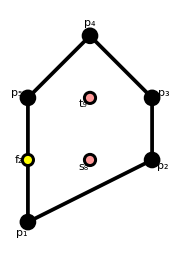
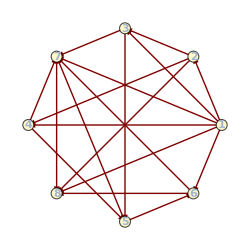
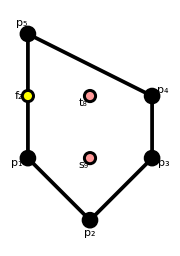
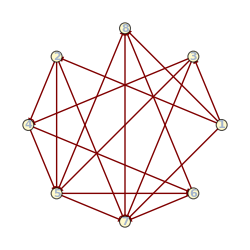

```mathematica
Map[IsomorphicQuiverQ[WL352PhaseADef1Final,#]&,modelsgrid[8,5],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL352PhaseADef1Final,Splice@Extract[modelsgrid[8,5],Position[%,True]]}
]
```

### L^(3,5,2) Phase A → K^(2,4,1,2) Phase C

```mathematica
WL352PhaseA=modelsgrid[8,4][[3,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WL352PhaseAzz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

-Graphics- | {0,-1} | 6 | 3 | {X_1[1,2]·X_1[2,4]·X_1[4,7]·X_1[7,6]·X_1[6,1],-(X_1[1,3]·X_1[3,5]·X_1[5,7]·X_1[7,8]·X_1[8,1])} | 2.95626
 | {2,-1} | 10 | 5 | {X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,7]·X_1[7,8]·X_1[8,6]·X_1[6,1],-(X_1[1,3]·X_1[3,2]·X_1[2,4]·X_1[4,7]·X_1[7,8]·X_1[8,6]·X_1[6,1])} | 3.97025
 | {1,2} | 12 | 6 | {-(X_1[1,7]·X_1[7,3]·X_1[3,2]·X_1[2,8]·X_1[8,6]·X_1[6,5]·X_1[5,4]·X_1[4,1]),X_1[1,7]·X_1[7,3]·X_1[3,2]·X_1[2,8]·X_1[8,6]·X_1[6,5]·X_1[5,4]·X_1[4,1]} | 4.59447
 | {-1,0} | 4 | 2 | {X_1[1,2]·X_1[2,8]·X_1[8,1],-(X_1[5,7]·X_1[7,6]·X_1[6,5])} | 1.49301
 | {-1,0} | 4 | 2 | {-(X_1[3,4]·X_1[4,3]),X_1[5,7]·X_1[7,6]·X_1[6,5]} | 1.49301
 | {-1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,8]·X_1[8,1]),X_1[3,4]·X_1[4,3]} | 1.49301

```mathematica
WL352PhaseADef2=WL352PhaseA+{μ,0,0}.WL352PhaseAzz[{-1,0}];
WL352PhaseADef2Min=WL352PhaseADef2//IntegrateOutMassTerms//Expand;
```

```mathematica
WL352PhaseADef2Final=Simplify@Expand[μ WL352PhaseADef2Min/.First@Echo@FindFieldRedefinition[WL352PhaseADef2Min]]
```

{{X_1[1,2]→-(X_1[1,3]·X_1[3,2])/μ+X_1[1,2]/μ,X_1[3,4]→X_1[3,2]·X_1[2,4] (-1/μ-β_1[3,4])+X_1[3,5]·X_1[5,4] β_1[3,4]+X_1[3,4]/μ,X_1[4,3]→X_1[4,7]·X_1[7,3] (-1/μ-β_1[3,4])+X_1[4,1]·X_1[1,3] β_1[3,4]+X_1[4,3]/μ,X_1[5,7]→-(X_1[5,4]·X_1[4,7])/μ+X_1[5,7]/μ,X_1[7,6]→(X_1[7,8]·X_1[8,6])/μ-X_1[7,6]/μ,X_1[8,1]→(X_1[8,6]·X_1[6,1])/μ-X_1[8,1]/μ}}

X_1[1,2]·X_1[2,4]·X_1[4,1]-X_1[1,2]·X_1[2,8]·X_1[8,1]-X_1[1,3]·X_1[3,4]·X_1[4,1]-X_1[1,7]·X_1[7,6]·X_1[6,1]+X_1[1,7]·X_1[7,8]·X_1[8,1]-X_1[2,4]·X_1[4,3]·X_1[3,2]+X_1[3,4]·X_1[4,7]·X_1[7,3]+X_1[3,5]·X_1[5,4]·X_1[4,3]-X_1[3,5]·X_1[5,7]·X_1[7,3]+X_1[5,7]·X_1[7,6]·X_1[6,5]+X_1[1,3]·X_1[3,2]·X_1[2,8]·X_1[8,6]·X_1[6,1]-X_1[4,7]·X_1[7,8]·X_1[8,6]·X_1[6,5]·X_1[5,4]

<|PdP_(4  c) (2)→{False,False,False,False,False,False,False,False},PdP_(4  d) (2)→{False,False,False,False,False,False,False,False},K^(2, 5, 1, 1)→{False,False,False,False},K^(2, 4, 1, 2)→{False,False,True,False,False,False,False}|>

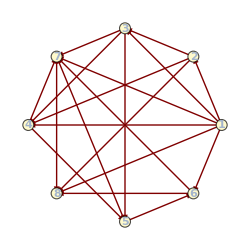
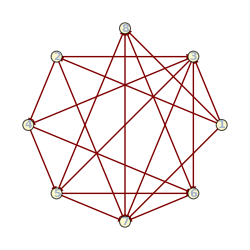
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[WL352PhaseADef2Final,#]&,modelsgrid[8,5],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL352PhaseADef2Final,Splice@Extract[modelsgrid[8,5],Position[%,True]]}
]
```

### PdP_(4c) Phase A → PdP_(4e) Phase A

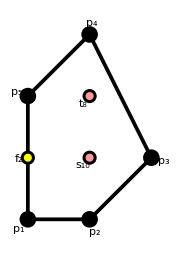
-Graphics- | {0,-1} | 6 | 3 | {X_1[1,2]·X_1[2,5]·X_1[5,6]·X_1[6,7]·X_1[7,1],-(X_1[1,3]·X_1[3,4]·X_1[4,8]·X_1[8,7]·X_1[7,1])} | 2.6225
 | {1,-1} | 6 | 3 | {X_1[1,3]·X_1[3,4]·X_1[4,8]·X_1[8,6]·X_1[6,7]·X_1[7,1],-(X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,6]·X_1[6,7]·X_1[7,1])} | 2.9223
 | {2,1} | 10 | 5 | {-(X_1[1,3]·X_1[3,2]·X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,4]·X_2[4,5]·X_1[5,1]),X_1[1,3]·X_1[3,2]·X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,4]·X_2[4,5]·X_1[5,1]} | 3.97709
 | {-1,1} | 6 | 3 | {X_1[1,2]·X_1[2,8]·X_1[8,6]·X_1[6,4]·X_1[4,5]·X_1[5,1],-(X_1[2,8]·X_1[8,7]·X_1[7,4]·X_1[4,5]·X_1[5,3]·X_1[3,2])} | 3.0777
 | {-1,0} | 4 | 2 | {-(X_1[4,5]·X_1[5,6]·X_1[6,4]),X_1[1,2]·X_1[2,8]·X_1[8,7]·X_1[7,1]} | 1.70021
 | {-1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,8]·X_1[8,7]·X_1[7,1]),X_1[3,4]·X_1[4,5]·X_1[5,3]} | 1.70021

```mathematica
WPdP4cPhaseA=modelsgrid[8,5][[1,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WPdP4cPhaseAzz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

```mathematica
WPdP4cPhaseADef1=WPdP4cPhaseA+{μ,0}.WPdP4cPhaseAzz[{-1,0}];
```

```mathematica
WPdP4cPhaseADef1Final=Simplify@Expand[μ WPdP4cPhaseADef1/.First@Echo@FindFieldRedefinition[WPdP4cPhaseADef1]]
```

{{X_1[1,2]→-(X_1[1,3]·X_1[3,2])/μ+X_1[1,2]/μ,X_1[4,5]→X_1[4,5]/μ-X_2[4,5]/μ,X_1[5,3]→-(X_1[5,1]·X_1[1,3])/μ+X_1[5,3]/μ,X_1[6,4]→(X_1[6,7]·X_1[7,4])/μ-X_1[6,4]/μ,X_1[8,7]→(X_1[8,6]·X_1[6,7])/μ-X_1[8,7]/μ}}

X_1[1,2]·X_1[2,5]·X_1[5,1]-X_1[2,5]·X_1[5,3]·X_1[3,2]+X_1[3,4]·X_2[4,5]·X_1[5,3]+X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[4,8]·X_1[8,6]·X_1[6,4]+X_1[4,8]·X_1[8,7]·X_1[7,4]-X_1[1,2]·X_1[2,8]·X_1[8,7]·X_1[7,1]-X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]-X_1[5,6]·X_1[6,7]·X_1[7,4]·X_2[4,5]+X_1[1,3]·X_1[3,2]·X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,1]

<|PdP_(4  e) (3)→{True,False,False,False,False,False,False,False,False,False,False,False,False},PdP_(4  f) (2)→{False,False,False,False,False,False,False,False,False,False,False,False,False}|>

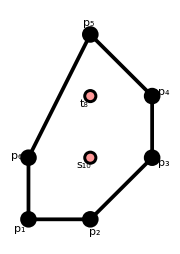
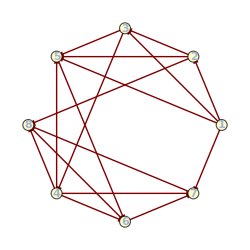
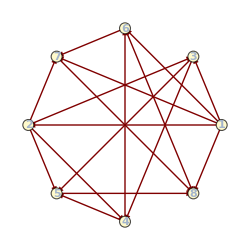
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[WPdP4cPhaseADef1Final,#]&,modelsgrid[8,6],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP4cPhaseADef1Final,Splice@Extract[modelsgrid[8,6],Position[%,True]]}
]
```

### PdP_(4d) Phase A → PdP_(4f) Phase A

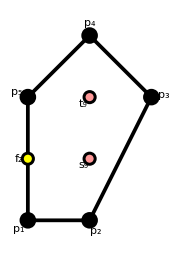
-Graphics- | {0,-1} | 6 | 3 | {-(X_1[1,7]·X_1[7,5]·X_2[5,6]·X_1[6,4]·X_1[4,3]·X_1[3,1]),X_1[2,8]·X_1[8,7]·X_1[7,5]·X_2[5,6]·X_1[6,4]·X_1[4,2]} | 2.8441
 | {2,-1} | 8 | 4 | {X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,4]·X_1[4,2]·X_1[2,3]·X_1[3,1],-(X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,4]·X_1[4,2]·X_1[2,8]·X_1[8,1])} | 3.4677
 | {1,1} | 8 | 4 | {X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,5]·X_1[5,6]·X_1[6,8]·X_1[8,1],-(X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,5]·X_1[5,6]·X_1[6,8]·X_1[8,1])} | 3.4677
 | {-1,1} | 6 | 3 | {-(X_1[1,4]·X_1[4,3]·X_1[3,5]·X_2[5,6]·X_1[6,8]·X_1[8,1]),X_1[2,3]·X_1[3,5]·X_2[5,6]·X_1[6,8]·X_1[8,7]·X_1[7,2]} | 2.8441
 | {-1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,1]),X_1[3,5]·X_2[5,6]·X_1[6,4]·X_1[4,3]} | 1.6882
 | {-1,0} | 4 | 2 | {X_1[1,2]·X_1[2,1],-(X_1[6,8]·X_1[8,7]·X_1[7,5]·X_2[5,6])} | 1.6882

```mathematica
WPdP4dPhaseA=modelsgrid[8,5][[2,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WPdP4dPhaseAzz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

```mathematica
WPdP4dPhaseADef1=WPdP4dPhaseA+{μ,0}. WPdP4dPhaseAzz[{-1,0}]//IntegrateOutMassTerms//Expand;
```

```mathematica
WPdP4dPhaseADef1Final=Expand@Simplify[μ WPdP4dPhaseADef1/.First@Echo@FindFieldRedefinition[WPdP4dPhaseADef1]];
```

{{X_1[4,3]→(X_1[4,2]·X_1[2,3])/μ-X_1[4,3]/μ,X_2[5,6]→-X_1[5,6]/μ+X_2[5,6]/μ,X_1[8,7]→-(X_1[8,1]·X_1[1,7])/μ+X_1[8,7]/μ}}

<|PdP_(4  e) (3)→{False,False,False,False,False,False,False,False,False,False,False,False,False},PdP_(4  f) (2)→{True,False,False,False,False,False,False,False,False,False,False,False,False}|>

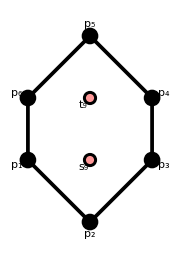
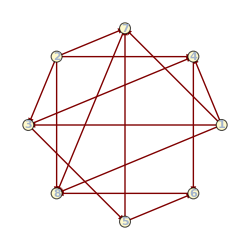
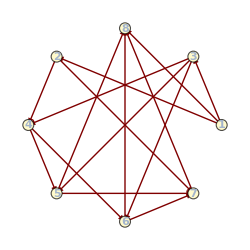
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[WPdP4dPhaseADef1Final,#]&,modelsgrid[8,6],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP4dPhaseADef1Final,Splice@Extract[modelsgrid[8,6],Position[%,True]]}
]
```

### L^(5,4,1) → K^(2,4,1,3) Phase B

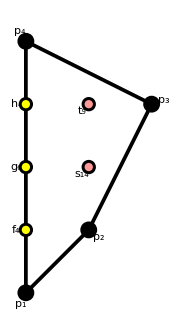
-Graphics- | {1,-1} | 8 | 4 | {-(X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,8]·X_1[8,1]),X_1[2,3]·X_1[3,6]·X_1[6,7]·X_1[7,9]·X_1[9,2]} | 3.18041
 | {2,-1} | 10 | 5 | {X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,6]·X_1[6,8]·X_1[8,1],-(X_1[2,3]·X_1[3,6]·X_1[6,8]·X_1[8,7]·X_1[7,9]·X_1[9,2])} | 3.80448
 | {1,2} | 16 | 8 | {-(X_1[1,9]·X_1[9,6]·X_1[6,4]·X_1[4,2]·X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]),X_1[1,9]·X_1[9,6]·X_1[6,4]·X_1[4,2]·X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]} | 5.51139
 | {-1,0} | 4 | 2 | {X_1[1,2]·X_1[2,1],-(X_1[8,9]·X_1[9,8])} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[5,6]·X_1[6,7]·X_1[7,5]),X_1[8,9]·X_1[9,8]} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[3,4]·X_1[4,3]),X_1[5,6]·X_1[6,7]·X_1[7,5]} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,1]),X_1[3,4]·X_1[4,3]} | 1.37593

```mathematica
WL541=modelsgrid[9,4][[1,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WL541zz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

```mathematica
WL541Def1=WL541+{μ,0,0,0}.WL541zz[{-1,0}]//IntegrateOutMassTerms//Expand;
```

```mathematica
WL541Def1Final=Simplify[μ WL541Def1/.First@Echo@FindFieldRedefinition[WL541Def1]];
```

{{X_1[3,4]→X_1[3,1]·X_1[1,4] (-1/μ-β_1[3,4])+X_1[3,6]·X_1[6,4] β_1[3,4]+X_1[3,4]/μ,X_1[4,3]→X_1[4,5]·X_1[5,3] (-1/μ-β_1[3,4])+X_1[4,2]·X_1[2,3] β_1[3,4]+X_1[4,3]/μ,X_1[5,6]→-(X_1[5,3]·X_1[3,6])/μ+X_1[5,6]/μ,X_1[6,7]→-(X_1[6,8]·X_1[8,7])/μ+X_1[6,7]/μ}}

<|PdP_(5  b) (2)→{False,False,False,False,False,False,False,False},K^(2, 5, 1, 2)→{False,False,False,False,False,False,False,False,False,False},K^(2, 4, 1, 3)→{False,True,False,False,False},K^(4, 3, 2, 2)→{False,False,False,False,False,False,False,False,False}|>

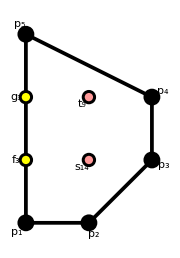
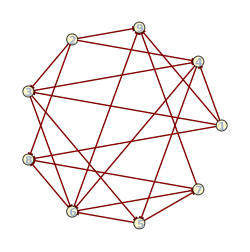
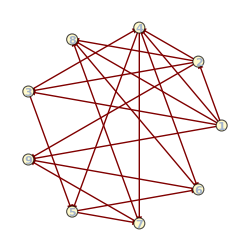
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[WL541Def1Final,#]&,modelsgrid[9,5],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL541Def1Final,Splice@Extract[modelsgrid[9,5],Position[%,True]]}
]
```

### L^(5,4,1) → K^(4,3,2,2) Phase D

```mathematica
WL541=modelsgrid[9,4][[1,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WL541zz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

-Graphics- | {1,-1} | 8 | 4 | {-(X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,8]·X_1[8,1]),X_1[2,3]·X_1[3,6]·X_1[6,7]·X_1[7,9]·X_1[9,2]} | 3.18041
 | {2,-1} | 10 | 5 | {X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,6]·X_1[6,8]·X_1[8,1],-(X_1[2,3]·X_1[3,6]·X_1[6,8]·X_1[8,7]·X_1[7,9]·X_1[9,2])} | 3.80448
 | {1,2} | 16 | 8 | {-(X_1[1,9]·X_1[9,6]·X_1[6,4]·X_1[4,2]·X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]),X_1[1,9]·X_1[9,6]·X_1[6,4]·X_1[4,2]·X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]} | 5.51139
 | {-1,0} | 4 | 2 | {X_1[1,2]·X_1[2,1],-(X_1[8,9]·X_1[9,8])} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[5,6]·X_1[6,7]·X_1[7,5]),X_1[8,9]·X_1[9,8]} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[3,4]·X_1[4,3]),X_1[5,6]·X_1[6,7]·X_1[7,5]} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,1]),X_1[3,4]·X_1[4,3]} | 1.37593

```mathematica
WL541Def2=WL541+{μ,μ,0,0}.WL541zz[{-1,0}]//IntegrateOutMassTerms//Expand;
```

```mathematica
WL541Def2Final=Simplify[μ WL541Def2/.First@Echo@FindFieldRedefinition[WL541Def2]];
```

{{X_1[3,4]→X_1[3,1]·X_1[1,4] (-1/μ-β_1[3,4])+X_1[3,6]·X_1[6,4] β_1[3,4]+X_1[3,4]/μ,X_1[4,3]→X_1[4,5]·X_1[5,3] (-1/μ-β_1[3,4])+X_1[4,2]·X_1[2,3] β_1[3,4]+X_1[4,3]/μ,X_1[5,6]→-(X_1[5,3]·X_1[3,6])/μ+X_1[5,6]/μ,X_1[6,7]→(X_1[6,8]·X_1[8,7])/μ-X_1[6,7]/μ,X_1[8,9]→X_1[8,1]·X_1[1,9] (1/μ-β_1[8,9])+X_1[8,7]·X_1[7,9] β_1[8,9]-X_1[8,9]/μ,X_1[9,8]→X_1[9,6]·X_1[6,8] (1/μ-β_1[8,9])+X_1[9,2]·X_1[2,8] β_1[8,9]-X_1[9,8]/μ}}

<|PdP_(5  b) (2)→{False,False,False,False,False,False,False,False},K^(2, 5, 1, 2)→{False,False,False,False,False,False,False,False,False,False},K^(2, 4, 1, 3)→{False,False,False,False,False},K^(4, 3, 2, 2)→{False,False,False,True,False,False,False,False,False}|>

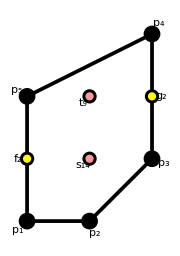
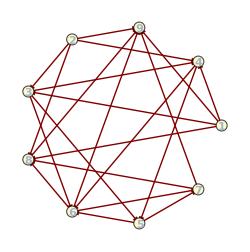
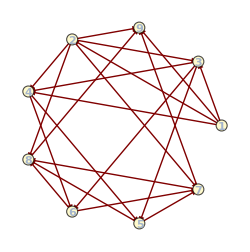
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[WL541Def2Final,#]&,modelsgrid[9,5],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL541Def2Final,Splice@Extract[modelsgrid[9,5],Position[%,True]]}
]
```

### L^(5,4,1) → K^(2,4,1,3) Phase C

```mathematica
WL541=modelsgrid[9,4][[1,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WL541zz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

-Graphics- | {1,-1} | 8 | 4 | {-(X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,8]·X_1[8,1]),X_1[2,3]·X_1[3,6]·X_1[6,7]·X_1[7,9]·X_1[9,2]} | 3.18041
 | {2,-1} | 10 | 5 | {X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,6]·X_1[6,8]·X_1[8,1],-(X_1[2,3]·X_1[3,6]·X_1[6,8]·X_1[8,7]·X_1[7,9]·X_1[9,2])} | 3.80448
 | {1,2} | 16 | 8 | {-(X_1[1,9]·X_1[9,6]·X_1[6,4]·X_1[4,2]·X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]),X_1[1,9]·X_1[9,6]·X_1[6,4]·X_1[4,2]·X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]} | 5.51139
 | {-1,0} | 4 | 2 | {X_1[1,2]·X_1[2,1],-(X_1[8,9]·X_1[9,8])} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[5,6]·X_1[6,7]·X_1[7,5]),X_1[8,9]·X_1[9,8]} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[3,4]·X_1[4,3]),X_1[5,6]·X_1[6,7]·X_1[7,5]} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,1]),X_1[3,4]·X_1[4,3]} | 1.37593

```mathematica
WL541Def3=WL541+{0,μ,0,0}.WL541zz[{-1,0}]//IntegrateOutMassTerms//Expand;
```

```mathematica
WL541Def3Final=Simplify[μ WL541Def3/.First@Echo@FindFieldRedefinition[WL541Def3]];
```

{{X_1[1,2]→X_1[1,4]·X_1[4,2] (-1/μ-β_1[1,2])+X_1[1,9]·X_1[9,2] β_1[1,2]+X_1[1,2]/μ,X_1[2,1]→X_1[2,8]·X_1[8,1] (-1/μ-β_1[1,2])+X_1[2,3]·X_1[3,1] β_1[1,2]+X_1[2,1]/μ,X_1[3,4]→X_1[3,1]·X_1[1,4] (-1/μ-β_1[3,4])+X_1[3,6]·X_1[6,4] β_1[3,4]+X_1[3,4]/μ,X_1[4,3]→X_1[4,5]·X_1[5,3] (-1/μ-β_1[3,4])+X_1[4,2]·X_1[2,3] β_1[3,4]+X_1[4,3]/μ,X_1[5,6]→-(X_1[5,3]·X_1[3,6])/μ+X_1[5,6]/μ,X_1[6,7]→(X_1[6,8]·X_1[8,7])/μ-X_1[6,7]/μ}}

<|PdP_(5  b) (2)→{False,False,False,False,False,False,False,False},K^(2, 5, 1, 2)→{False,False,False,False,False,False,False,False,False,False},K^(2, 4, 1, 3)→{False,False,True,False,False},K^(4, 3, 2, 2)→{False,False,False,False,False,False,False,False,False}|>

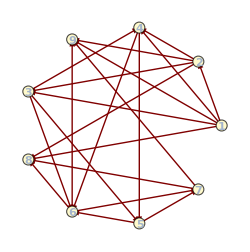
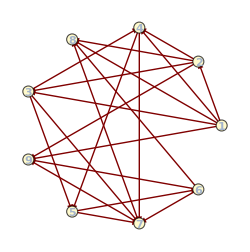
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[WL541Def3Final,#]&,modelsgrid[9,5],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL541Def3Final,Splice@Extract[modelsgrid[9,5],Position[%,True]]}
]
```

### L^(5,4,1) → K^(4,3,2,2) Phase E

```mathematica
WL541=modelsgrid[9,4][[1,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WL541zz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

-Graphics- | {1,-1} | 8 | 4 | {-(X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,8]·X_1[8,1]),X_1[2,3]·X_1[3,6]·X_1[6,7]·X_1[7,9]·X_1[9,2]} | 3.18041
 | {2,-1} | 10 | 5 | {X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,6]·X_1[6,8]·X_1[8,1],-(X_1[2,3]·X_1[3,6]·X_1[6,8]·X_1[8,7]·X_1[7,9]·X_1[9,2])} | 3.80448
 | {1,2} | 16 | 8 | {-(X_1[1,9]·X_1[9,6]·X_1[6,4]·X_1[4,2]·X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]),X_1[1,9]·X_1[9,6]·X_1[6,4]·X_1[4,2]·X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]} | 5.51139
 | {-1,0} | 4 | 2 | {X_1[1,2]·X_1[2,1],-(X_1[8,9]·X_1[9,8])} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[5,6]·X_1[6,7]·X_1[7,5]),X_1[8,9]·X_1[9,8]} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[3,4]·X_1[4,3]),X_1[5,6]·X_1[6,7]·X_1[7,5]} | 1.37593
 | {-1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,1]),X_1[3,4]·X_1[4,3]} | 1.37593

```mathematica
WL541Def4=WL541+{μ,0,μ,0}.WL541zz[{-1,0}]//IntegrateOutMassTerms//Expand;
```

```mathematica
WL541Def4Final=Simplify[μ WL541Def4/.First@Echo@FindFieldRedefinition[WL541Def4]];
```

{{X_1[5,6]→(X_1[5,3]·X_1[3,6])/μ-X_1[5,6]/μ,X_1[6,7]→-(X_1[6,8]·X_1[8,7])/μ+X_1[6,7]/μ}}

<|PdP_(5  b) (2)→{False,False,False,False,False,False,False,False},K^(2, 5, 1, 2)→{False,False,False,False,False,False,False,False,False,False},K^(2, 4, 1, 3)→{False,False,False,False,False},K^(4, 3, 2, 2)→{False,False,False,False,True,False,False,False,False}|>

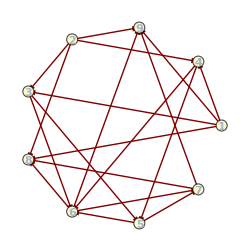
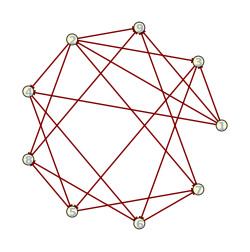
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[IsomorphicQuiverQ[WL541Def4Final,#]&,modelsgrid[9,5],{2}]
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL541Def4Final,Splice@Extract[modelsgrid[9,5],Position[%,True]]}
]
```

```mathematica
modelsgrid[9,5][[4,1]]
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

X_1[1,3]·X_1[3,2]·X_1[2,1]-X_1[1,9]·X_1[9,2]·X_1[2,1]+X_1[2,8]·X_1[8,9]·X_1[9,2]-X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,1]-X_1[2,4]·X_1[4,6]·X_1[6,3]·X_1[3,2]-X_1[2,8]·X_1[8,5]·X_1[5,7]·X_1[7,2]+X_1[3,5]·X_1[5,7]·X_1[7,6]·X_1[6,3]+X_1[4,6]·X_1[6,8]·X_1[8,5]·X_1[5,4]-X_1[6,8]·X_1[8,9]·X_1[9,7]·X_1[7,6]+X_1[1,9]·X_1[9,7]·X_1[7,2]·X_1[2,4]·X_1[4,1]

-Graphics- | {0,-1} | 6 | 3 | {X_1[1,3]·X_1[3,5]·X_1[5,7]·X_1[7,2]·X_1[2,1],-(X_1[2,4]·X_1[4,6]·X_1[6,8]·X_1[8,9]·X_1[9,7]·X_1[7,2])} | 2.83196
 | {1,-1} | 6 | 3 | {-(X_1[1,3]·X_1[3,5]·X_1[5,7]·X_1[7,2]·X_1[2,4]·X_1[4,1]),X_1[2,4]·X_1[4,6]·X_1[6,8]·X_1[8,9]·X_1[9,2]} | 2.83196
 | {1,0} | 4 | 2 | {X_1[1,3]·X_1[3,2]·X_1[2,4]·X_1[4,1],-(X_1[5,7]·X_1[7,6]·X_1[6,8]·X_1[8,5])} | 2.
 | {1,0} | 4 | 2 | {-(X_1[1,9]·X_1[9,2]·X_1[2,4]·X_1[4,1]),X_1[5,7]·X_1[7,6]·X_1[6,8]·X_1[8,5]} | 2.
 | {-1,2} | 10 | 5 | {X_1[1,9]·X_1[9,7]·X_1[7,6]·X_1[6,3]·X_1[3,2]·X_1[2,8]·X_1[8,5]·X_1[5,4]·X_1[4,1],-(X_1[1,9]·X_1[9,7]·X_1[7,6]·X_1[6,3]·X_1[3,2]·X_1[2,8]·X_1[8,5]·X_1[5,4]·X_1[4,1])} | 4.33609
 | {-1,0} | 4 | 2 | {-(X_1[3,5]·X_1[5,4]·X_1[4,6]·X_1[6,3]),X_1[2,8]·X_1[8,9]·X_1[9,7]·X_1[7,2]} | 2.
 | {-1,0} | 4 | 2 | {-(X_1[1,9]·X_1[9,7]·X_1[7,2]·X_1[2,1]),X_1[3,5]·X_1[5,4]·X_1[4,6]·X_1[6,3]} | 2.

```mathematica
WL541=modelsgrid[9,4][[1,1]];
{PolytopePlot[ToricDiagram[%],"PolytopeCellLabel"->Automatic],ZigZagData[%]};
Grid[Join[{{Item[First[%],Alignment->Center]},Splice@Table[{SpanFromAbove},Length@Last[%]-1]},Values@Last[%],2],Frame->All]
WL541zz=GroupBy[Last[%%],First->(Total[#[[4]]]&),Values];
```

### SPP/ℤ_3 (1,0,0,2) Phase A → K^(2,5,1,2) Phase A

```mathematica
WSPPZ3PhaseA=modelsgrid[9,4][[2,1]];
```

```mathematica
WSPPZ3PhaseADef1=WSPPZ3PhaseA+{μ,-μ,0}.{Subscript[X, 1][6,4]·Subscript[X, 1][4,7]·Subscript[X, 1][7,6],Subscript[X, 1][9,8]·Subscript[X, 1][8,2]·Subscript[X, 1][2,9],Subscript[X, 1][1,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,1]};
```

```mathematica
RedefChoice15={Subscript[β, 1][5,3]->Subscript[β, 1][6,4], Subscript[β, 1][9,8]->-1/μ,Subscript[β, 1][2,9]->1/μ,Subscript[β, 1][3,1]->1/μ,Subscript[α, 1][3,1]->-1/μ,Subscript[β, 1][6,4]->1/μ,Subscript[β, 1][7,6]->-1/μ,Subscript[α, 1][5,3]->-1/μ,Subscript[α, 1][2,9]->-1/μ,Subscript[α, 1][6,4]->-1/μ,Subscript[α, 1][7,6]->1/μ,Subscript[α, 1][9,8]->1/μ};
RedefRules15=FieldRedefinition[{Subscript[X, 1][2,9],Subscript[X, 1][3,1],Subscript[X, 1][5,3],Subscript[X, 1][6,4],Subscript[X, 1][7,6],Subscript[X, 1][9,8]},QuiverFromFields[WSPPZ3PhaseADef1],2]//.RedefChoice15;
RedefRules15Mass={Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][5,4]->μ Subscript[X, 1][5,4],Subscript[X, 1][6,4]->μ Subscript[X, 1][6,4],Subscript[X, 1][9,3]->μ Subscript[X, 1][9,3],Subscript[X, 1][9,7]->μ Subscript[X, 1][9,7],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8]};
RedefRules15//Column
```

X_1[2,9]→(X_1[2,1]·X_1[1,9])/μ-X_1[2,9]/μ
X_1[3,1]→(X_1[3,2]·X_1[2,1])/μ-X_1[3,1]/μ
X_1[5,3]→(X_1[5,4]·X_1[4,3])/μ-X_1[5,3]/μ
X_1[6,4]→(X_1[6,5]·X_1[5,4])/μ-X_1[6,4]/μ
X_1[7,6]→-(X_1[7,8]·X_1[8,6])/μ+X_1[7,6]/μ
X_1[9,8]→-(X_1[9,7]·X_1[7,8])/μ+X_1[9,8]/μ

```mathematica
WSPPZ3PhaseADef1Final=Simplify[WSPPZ3PhaseADef1/.RedefRules15/.RedefRules15Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WSPPZ3PhaseADef1Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[9,5][[2]]
```

{{<|1→8,5→7,9→1,2→2,3→9,6→5,4→6,7→3,8→4|>},{},{},{},{},{},{},{},{}}

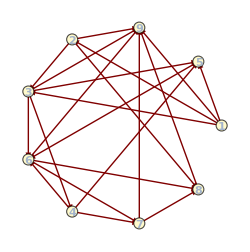
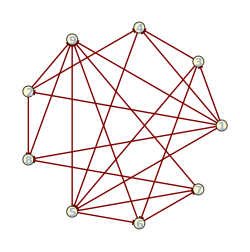
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WSPPZ3PhaseADef1Final,modelsgrid[9,5][[2,1]]}
]
```

### PdP_(5b) Phase A → PdP_(5c) Phase A

```mathematica
WPdP5bPhaseA=modelsgrid[9,5][[1,1]];
```

```mathematica
WPdP5bPhaseADef1=WPdP5bPhaseA+{μ,-μ,0}.{Subscript[X, 1][8,7]·Subscript[X, 1][7,8],Subscript[X, 1][3,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,9]·Subscript[X, 1][9,1]};
WPdP5bPhaseADef1Min=WPdP5bPhaseADef1//IntegrateOutMassTerms;
```

```mathematica
RedefChoice16={Subscript[β, 1][5,3]->-1/μ,Subscript[β, 1][2,9]->-1/μ,Subscript[β, 1][1,4]->-1/μ,Subscript[β, 1][6,5]->1/μ,Subscript[α, 1][1,4]->1/μ,Subscript[α, 1][2,9]->1/μ,Subscript[α, 1][5,3]->1/μ,Subscript[α, 1][6,5]->-1/μ};
RedefRules16=FieldRedefinition[{Subscript[X, 1][1,4],Subscript[X, 1][2,9],Subscript[X, 1][5,3],Subscript[X, 1][6,5]},QuiverFromFields[WPdP5bPhaseADef1Min],2]//.RedefChoice16;
RedefRules16Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][8,6]->μ Subscript[X, 1][8,6],Subscript[X, 1][9,1]->μ Subscript[X, 1][9,1],Subscript[X, 1][9,7]->μ Subscript[X, 1][9,7]};
RedefRules16//Column
```

X_1[1,4]→-(X_1[1,3]·X_1[3,4])/μ+X_1[1,4]/μ
X_1[2,9]→-(X_1[2,8]·X_1[8,9])/μ+X_1[2,9]/μ
X_1[5,3]→-(X_1[5,1]·X_1[1,3])/μ+X_1[5,3]/μ
X_1[6,5]→(X_1[6,7]·X_1[7,5])/μ-X_1[6,5]/μ

```mathematica
WPdP5bPhaseADef1Final=Simplify[WPdP5bPhaseADef1Min/.RedefRules16/.RedefRules16Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP5bPhaseADef1Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[9,6][[1]]
```

{{<|1→1,3→2,4→4,2→9,8→8,9→6,6→5,5→3,7→7|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

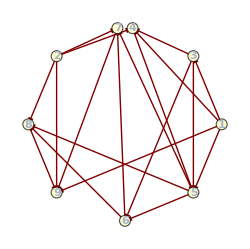
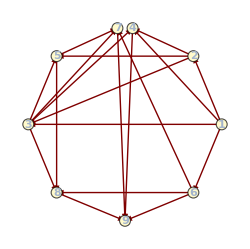
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP5bPhaseADef1Final,modelsgrid[9,6][[1,1]]}
]
```

### ℂ^3/ℤ_2×ℤ_5 (1,3,4) → L^(2,3,2)/ℤ_2 (1,0,0,1) Phase A

```mathematica
WC3Z2Z5=modelsgrid[10,3][[1,1]];
```

```mathematica
WC3Z2Z5Def1=WC3Z2Z5+{μ,-μ,μ,-μ,0}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][8,7]·Subscript[X, 1][7,8],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9],Subscript[X, 1][6,5]·Subscript[X, 1][5,6]};
WC3Z2Z5Def1Min=WC3Z2Z5Def1//IntegrateOutMassTerms;
```

```mathematica
RedefChoice17={Subscript[γ, 1][5,6]->Subscript[β, 1][6,5],Subscript[γ, 1][6,5]->Subscript[β, 1][5,6],Subscript[β, 1][6,5]->-1/μ-Subscript[β, 1][5,6],Subscript[α, 1][5,6]->1/μ,Subscript[α, 1][6,5]->1/μ};
RedefRules17=FieldRedefinition[{Subscript[X, 1][6,5],Subscript[X, 1][5,6]},QuiverFromFields[WC3Z2Z5Def1Min],2]//.RedefChoice17;
RedefRules17Mass={Subscript[X, 1][6,2]->μ Subscript[X, 1][6,2],Subscript[X, 1][6,5]->μ Subscript[X, 1][6,5],Subscript[X, 1][8,2]->μ Subscript[X, 1][8,2],Subscript[X, 1][8,3]->μ Subscript[X, 1][8,3],Subscript[X, 1][10,3]->μ Subscript[X, 1][10,3],Subscript[X, 1][10,5]->μ Subscript[X, 1][10,5]};
RedefRules17//Column
```

X_1[6,5]→X_1[6,10]·X_1[10,5] (-1/μ-β_1[5,6])+X_1[6,2]·X_1[2,5] β_1[5,6]+X_1[6,5]/μ
X_1[5,6]→X_1[5,1]·X_1[1,6] (-1/μ-β_1[5,6])+X_1[5,9]·X_1[9,6] β_1[5,6]+X_1[5,6]/μ

```mathematica
WC3Z2Z5Def1Final=Expand@Simplify[WC3Z2Z5Def1Min/.RedefRules17/.RedefRules17Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z5Def1Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,4][[1]]
```

{{},{<|1→5,6→7,8→3,2→6,5→8,7→4,3→2,9→10,4→1,10→9|>},{},{},{},{}}

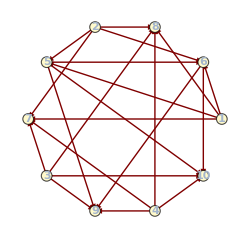
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z5Def1Final,modelsgrid[10,4][[1,1]]}
]
```

```mathematica
modelsgrid[10,4][[{1}]]
```

<|L^(2, 3, 2)/ℤ_2 (1,0,0,1)→{-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,2]·X_1[2,10]·X_1[10,1]-X_1[1,4]·X_1[4,2]·X_1[2,1]+X_1[1,9]·X_1[9,2]·X_1[2,1]-X_1[3,5]·X_1[5,6]·X_1[6,3]-X_1[4,6]·X_1[6,5]·X_1[5,4]+X_1[5,6]·X_1[6,8]·X_1[8,5]+X_1[5,7]·X_1[7,6]·X_1[6,5]-X_1[5,7]·X_1[7,8]·X_1[8,5]-X_1[6,8]·X_1[8,7]·X_1[7,6]+X_1[7,8]·X_1[8,10]·X_1[10,7]+X_1[7,9]·X_1[9,8]·X_1[8,7]+X_1[1,4]·X_1[4,6]·X_1[6,3]·X_1[3,1]-X_1[1,9]·X_1[9,8]·X_1[8,10]·X_1[10,1]+X_1[2,3]·X_1[3,5]·X_1[5,4]·X_1[4,2]-X_1[2,10]·X_1[10,7]·X_1[7,9]·X_1[9,2],-(X_1[5,7]·X_1[7,8]·X_1[8,5])-X_1[6,8]·X_1[8,7]·X_1[7,6]+X_1[7,8]·X_1[8,10]·X_1[10,7]+X_1[7,9]·X_1[9,8]·X_1[8,7]+X_1[1,3]·X_1[3,2]·X_1[2,10]·X_1[10,1]-X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,1]+X_1[1,9]·X_1[9,2]·X_1[2,4]·X_1[4,1]-X_1[1,9]·X_1[9,8]·X_1[8,10]·X_1[10,1]-X_1[2,4]·X_1[4,5]·X_1[5,3]·X_1[3,2]-X_1[2,10]·X_1[10,7]·X_1[7,9]·X_1[9,2]+X_1[3,6]·X_1[6,8]·X_1[8,5]·X_1[5,3]+X_1[4,5]·X_1[5,7]·X_1[7,6]·X_1[6,4],X_1[1,6]·X_1[6,3]·X_1[3,1]-X_1[1,6]·X_1[6,4]·X_1[4,1]-X_1[1,9]·X_1[9,8]·X_1[8,1]+X_1[1,10]·X_1[10,8]·X_1[8,1]+X_1[2,3]·X_1[3,5]·X_1[5,2]-X_1[2,4]·X_1[4,5]·X_1[5,2]-X_1[2,7]·X_1[7,9]·X_1[9,2]+X_1[2,7]·X_1[7,10]·X_1[10,2]-X_1[3,5]·X_1[5,6]·X_1[6,3]+X_1[5,6]·X_1[6,8]·X_1[8,5]-X_1[6,8]·X_1[8,7]·X_1[7,6]+X_1[7,9]·X_1[9,8]·X_1[8,7]+X_1[1,9]·X_1[9,2]·X_1[2,4]·X_1[4,1]-X_1[1,10]·X_1[10,2]·X_1[2,3]·X_1[3,1]+X_1[4,5]·X_1[5,7]·X_1[7,6]·X_1[6,4]-X_1[5,7]·X_1[7,10]·X_1[10,8]·X_1[8,5],-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,2]·X_1[2,10]·X_1[10,1]+X_1[1,6]·X_1[6,3]·X_1[3,1]-X_1[1,6]·X_1[6,4]·X_1[4,1]+X_1[2,3]·X_1[3,5]·X_1[5,2]-X_1[2,4]·X_1[4,5]·X_1[5,2]-X_1[3,5]·X_1[5,6]·X_1[6,3]+X_1[5,6]·X_1[6,8]·X_1[8,5]-X_1[5,7]·X_1[7,8]·X_1[8,5]-X_1[6,8]·X_1[8,7]·X_1[7,6]+X_1[7,8]·X_1[8,10]·X_1[10,7]+X_1[7,9]·X_1[9,8]·X_1[8,7]+X_1[1,9]·X_1[9,2]·X_1[2,4]·X_1[4,1]-X_1[1,9]·X_1[9,8]·X_1[8,10]·X_1[10,1]-X_1[2,10]·X_1[10,7]·X_1[7,9]·X_1[9,2]+X_1[4,5]·X_1[5,7]·X_1[7,6]·X_1[6,4],-(X_1[1,3]·X_1[3,4]·X_1[4,1])+X_1[3,4]·X_1[4,6]·X_1[6,3]+X_1[3,8]·X_1[8,5]·X_1[5,3]-X_1[3,8]·X_1[8,6]·X_1[6,3]+X_1[4,5]·X_1[5,7]·X_1[7,4]-X_1[4,6]·X_1[6,7]·X_1[7,4]-X_1[5,7]·X_1[7,8]·X_1[8,5]+X_1[7,8]·X_1[8,10]·X_1[10,7]+X_1[1,3]·X_1[3,2]·X_1[2,10]·X_1[10,1]+X_1[1,9]·X_1[9,2]·X_1[2,4]·X_1[4,1]-X_1[1,9]·X_1[9,8]·X_1[8,10]·X_1[10,1]-X_1[2,4]·X_1[4,5]·X_1[5,3]·X_1[3,2]-X_1[2,10]·X_1[10,7]·X_1[7,9]·X_1[9,2]+X_1[6,7]·X_1[7,9]·X_1[9,8]·X_1[8,6],X_1[1,2]·X_1[2,4]·X_1[4,1]-X_1[1,2]·X_1[2,9]·X_1[9,1]-X_1[1,3]·X_1[3,4]·X_1[4,1]+X_1[1,8]·X_1[8,9]·X_1[9,1]-X_1[1,8]·X_1[8,10]·X_1[10,1]+X_1[2,9]·X_1[9,7]·X_1[7,2]-X_1[2,10]·X_1[10,7]·X_1[7,2]+X_1[3,4]·X_1[4,6]·X_1[6,3]+X_1[3,8]·X_1[8,5]·X_1[5,3]-X_1[3,8]·X_1[8,6]·X_1[6,3]+X_1[4,5]·X_1[5,7]·X_1[7,4]-X_1[4,6]·X_1[6,7]·X_1[7,4]-X_1[5,7]·X_1[7,8]·X_1[8,5]+X_1[6,7]·X_2[7,8]·X_1[8,6]+X_1[7,8]·X_1[8,10]·X_1[10,7]-X_1[8,9]·X_1[9,7]·X_2[7,8]+X_1[1,3]·X_1[3,2]·X_1[2,10]·X_1[10,1]-X_1[2,4]·X_1[4,5]·X_1[5,3]·X_1[3,2]}|>

### ℂ^3/ℤ_2×ℤ_5 (1,3,4) → L^(1,4,1)/ℤ_2 (1,0,0,1) Phase A

```mathematica
WC3Z2Z5=modelsgrid[10,3][[1,1]];
```

```mathematica
WC3Z2Z5Def2=WC3Z2Z5+{μ,-μ,0,0,0}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][8,7]·Subscript[X, 1][7,8],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9],Subscript[X, 1][6,5]·Subscript[X, 1][5,6]};
WC3Z2Z5Def2Min=WC3Z2Z5Def2//IntegrateOutMassTerms;
```

```mathematica
RedefChoice18={Subscript[γ, 1][5,6]->Subscript[β, 1][6,5],Subscript[γ, 1][6,5]->Subscript[β, 1][5,6],Subscript[β, 1][6,5]->-1/μ-Subscript[β, 1][5,6],Subscript[α, 1][5,6]->1/μ,Subscript[α, 1][6,5]->1/μ,
Subscript[γ, 1][3,4]->Subscript[β, 1][4,3],Subscript[γ, 1][4,3]->-1/μ-Subscript[β, 1][4,3],Subscript[β, 1][4,3]->-1/μ-Subscript[β, 1][3,4],Subscript[α, 1][3,4]->1/μ,Subscript[α, 1][4,3]->1/μ,
Subscript[β, 1][9,10]->Subscript[γ, 1][10,9],Subscript[γ, 1][9,10]->Subscript[β, 1][10,9],Subscript[γ, 1][10,9]->-1/μ-Subscript[β, 1][10,9],Subscript[α, 1][9,10]->1/μ,Subscript[α, 1][10,9]->1/μ};
RedefRules18=FieldRedefinition[{Subscript[X, 1][6,5],Subscript[X, 1][5,6],Subscript[X, 1][3,4],Subscript[X, 1][4,3],Subscript[X, 1][9,10],Subscript[X, 1][10,9]},QuiverFromFields[WC3Z2Z5Def2Min],2]//.RedefChoice18;
RedefRules18Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][6,2]->μ Subscript[X, 1][6,2],Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][8,3]->μ Subscript[X, 1][8,3],Subscript[X, 1][9,4]->μ Subscript[X, 1][9,4],Subscript[X, 1][9,6]->μ Subscript[X, 1][9,6],Subscript[X, 1][10,3]->μ Subscript[X, 1][10,3],Subscript[X, 1][10,5]->μ Subscript[X, 1][10,5]};
RedefRules18//Column
```

X_1[6,5]→X_1[6,10]·X_1[10,5] (-1/μ-β_1[5,6])+X_1[6,2]·X_1[2,5] β_1[5,6]+X_1[6,5]/μ
X_1[5,6]→X_1[5,1]·X_1[1,6] (-1/μ-β_1[5,6])+X_1[5,9]·X_1[9,6] β_1[5,6]+X_1[5,6]/μ
X_1[3,4]→X_1[3,7]·X_1[7,4] (-1/μ-β_1[3,4])+X_1[3,9]·X_1[9,4] β_1[3,4]+X_1[3,4]/μ
X_1[4,3]→X_1[4,10]·X_1[10,3] (-1/μ-β_1[3,4])+X_1[4,8]·X_1[8,3] β_1[3,4]+X_1[4,3]/μ
X_1[9,10]→X_1[9,6]·X_1[6,10] (-1/μ-β_1[10,9])+X_1[9,4]·X_1[4,10] β_1[10,9]+X_1[9,10]/μ
X_1[10,9]→X_1[10,3]·X_1[3,9] (-1/μ-β_1[10,9])+X_1[10,5]·X_1[5,9] β_1[10,9]+X_1[10,9]/μ

```mathematica
WC3Z2Z5Def2Final=Expand@Simplify[WC3Z2Z5Def2Min/.RedefRules18/.RedefRules18Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z5Def2Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,4][[2]]
```

{{<|1→5,6→4,8→8,2→6,5→3,7→7,3→10,4→9,9→2,10→1|>},{}}

```mathematica
modelsgrid[10,4][[{2}]]
```

<|L^(1, 4, 1)/ℤ_2 (1,0,0,1)→{X_1[1,2]·X_1[2,4]·X_1[4,1]-X_1[1,2]·X_1[2,9]·X_1[9,1]+X_1[1,3]·X_1[3,2]·X_1[2,1]-X_1[1,3]·X_1[3,4]·X_1[4,1]-X_1[1,10]·X_1[10,2]·X_1[2,1]+X_1[1,10]·X_1[10,9]·X_1[9,1]-X_1[2,4]·X_1[4,3]·X_1[3,2]+X_1[2,9]·X_1[9,10]·X_1[10,2]+X_1[3,4]·X_1[4,6]·X_1[6,3]+X_1[3,5]·X_1[5,4]·X_1[4,3]-X_1[7,9]·X_1[9,10]·X_1[10,7]-X_1[8,10]·X_1[10,9]·X_1[9,8]-X_1[3,5]·X_1[5,8]·X_1[8,6]·X_1[6,3]-X_1[4,6]·X_1[6,7]·X_1[7,5]·X_1[5,4]+X_1[5,8]·X_1[8,10]·X_1[10,7]·X_1[7,5]+X_1[6,7]·X_1[7,9]·X_1[9,8]·X_1[8,6],X_1[1,2]·X_1[2,4]·X_1[4,1]-X_1[1,2]·X_1[2,9]·X_1[9,1]+X_1[1,3]·X_1[3,2]·X_1[2,1]-X_1[1,3]·X_1[3,4]·X_1[4,1]-X_1[1,10]·X_1[10,2]·X_1[2,1]+X_1[1,10]·X_1[10,9]·X_1[9,1]+X_1[2,9]·X_1[9,10]·X_1[10,2]+X_1[3,4]·X_1[4,6]·X_1[6,3]+X_1[3,8]·X_1[8,5]·X_1[5,3]-X_1[3,8]·X_1[8,6]·X_1[6,3]+X_1[4,5]·X_1[5,7]·X_1[7,4]-X_1[4,6]·X_1[6,7]·X_1[7,4]-X_1[5,7]·X_1[7,8]·X_1[8,5]+X_1[7,8]·X_1[8,10]·X_1[10,7]-X_1[7,9]·X_1[9,10]·X_1[10,7]-X_1[8,10]·X_1[10,9]·X_1[9,8]-X_1[2,4]·X_1[4,5]·X_1[5,3]·X_1[3,2]+X_1[6,7]·X_1[7,9]·X_1[9,8]·X_1[8,6]}|>

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z5Def2Final,modelsgrid[10,4][[2,1]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### ℂ^3/ℤ_2×ℤ_5 (1,3,4) → L^(2,3,2)/ℤ_2 (1,0,0,1) Phase B

```mathematica
WC3Z2Z5=modelsgrid[10,3][[1,1]];
```

```mathematica
WC3Z2Z5Def3=WC3Z2Z5+{μ,0,-μ,0,0}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][8,7]·Subscript[X, 1][7,8],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9],Subscript[X, 1][6,5]·Subscript[X, 1][5,6]};
WC3Z2Z5Def3Min=WC3Z2Z5Def3//IntegrateOutMassTerms;
```

```mathematica
RedefChoice19={Subscript[γ, 1][5,6]->Subscript[β, 1][6,5],Subscript[γ, 1][6,5]->Subscript[β, 1][5,6],Subscript[β, 1][6,5]->-1/μ-Subscript[β, 1][5,6],Subscript[α, 1][5,6]->1/μ,Subscript[α, 1][6,5]->1/μ,
Subscript[γ, 1][3,4]->Subscript[β, 1][4,3],Subscript[γ, 1][4,3]->-1/μ-Subscript[β, 1][4,3],Subscript[β, 1][4,3]->-1/μ-Subscript[β, 1][3,4],Subscript[α, 1][3,4]->1/μ,Subscript[α, 1][4,3]->1/μ,
Subscript[β, 1][9,10]->Subscript[γ, 1][10,9],Subscript[γ, 1][9,10]->Subscript[β, 1][10,9],Subscript[γ, 1][10,9]->-1/μ-Subscript[β, 1][10,9],Subscript[α, 1][9,10]->1/μ,Subscript[α, 1][10,9]->1/μ,
Subscript[β, 1][8,7]->1/μ-Subscript[β, 1][7,8],Subscript[γ, 1][7,8]->1/μ-Subscript[β, 1][7,8],Subscript[γ, 1][8,7]->Subscript[β, 1][7,8],Subscript[α, 1][8,7]->-1/μ,Subscript[α, 1][7,8]->-1/μ};
RedefRules19=FieldRedefinition[{Subscript[X, 1][6,5],Subscript[X, 1][5,6],Subscript[X, 1][3,4],Subscript[X, 1][4,3],Subscript[X, 1][9,10],Subscript[X, 1][10,9],Subscript[X, 1][8,7],Subscript[X, 1][7,8]},QuiverFromFields[WC3Z2Z5Def2Min],2]//.RedefChoice19;
RedefRules19Mass={Subscript[X, 1][6,2]->μ Subscript[X, 1][6,2],Subscript[X, 1][6,5]->μ Subscript[X, 1][6,5],Subscript[X, 1][8,2]->μ Subscript[X, 1][8,2],Subscript[X, 1][8,3]->μ Subscript[X, 1][8,3],Subscript[X, 1][8,7]->μ Subscript[X, 1][8,7],Subscript[X, 1][10,3]->μ Subscript[X, 1][10,3],Subscript[X, 1][10,5]->μ Subscript[X, 1][10,5],Subscript[X, 1][10,9]->μ Subscript[X, 1][10,9]};
RedefRules19//Column
```

X_1[6,5]→X_1[6,10]·X_1[10,5] (-1/μ-β_1[5,6])+X_1[6,2]·X_1[2,5] β_1[5,6]+X_1[6,5]/μ
X_1[5,6]→X_1[5,1]·X_1[1,6] (-1/μ-β_1[5,6])+X_1[5,9]·X_1[9,6] β_1[5,6]+X_1[5,6]/μ
X_1[3,4]→X_1[3,7]·X_1[7,4] (-1/μ-β_1[3,4])+X_1[3,9]·X_1[9,4] β_1[3,4]+X_1[3,4]/μ
X_1[4,3]→X_1[4,10]·X_1[10,3] (-1/μ-β_1[3,4])+X_1[4,8]·X_1[8,3] β_1[3,4]+X_1[4,3]/μ
X_1[9,10]→X_1[9,6]·X_1[6,10] (-1/μ-β_1[10,9])+X_1[9,4]·X_1[4,10] β_1[10,9]+X_1[9,10]/μ
X_1[10,9]→X_1[10,3]·X_1[3,9] (-1/μ-β_1[10,9])+X_1[10,5]·X_1[5,9] β_1[10,9]+X_1[10,9]/μ
X_1[8,7]→X_1[8,3]·X_1[3,7] (1/μ-β_1[7,8])+X_1[8,2]·X_1[2,7] β_1[7,8]-X_1[8,7]/μ
X_1[7,8]→X_1[7,1]·X_1[1,8] (1/μ-β_1[7,8])+X_1[7,4]·X_1[4,8] β_1[7,8]-X_1[7,8]/μ

```mathematica
WC3Z2Z5Def3Final=Expand@Simplify[WC3Z2Z5Def3Min/.RedefRules19/.RedefRules19Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z5Def3Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,4][[1]]
```

{{<|1→3,6→5,8→1,2→4,5→6,7→2,3→9,9→8,4→10,10→7|>},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z5Def3Final,modelsgrid[10,4][[1,2]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
WC3Z2Z5=modelsgrid[10,3][[1,1]];
```

```mathematica
WC3Z2Z5Def4=WC3Z2Z5+{μ,0,0,-μ,0}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][8,7]·Subscript[X, 1][7,8],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9],Subscript[X, 1][6,5]·Subscript[X, 1][5,6]};
WC3Z2Z5Def4Min=WC3Z2Z5Def4//IntegrateOutMassTerms;
```

```mathematica
RedefChoice20={Subscript[γ, 1][5,6]->Subscript[β, 1][6,5],Subscript[γ, 1][6,5]->Subscript[β, 1][5,6],Subscript[β, 1][6,5]->(-1/μ-Subscript[β, 1][5,6]),Subscript[α, 1][5,6]->(1/μ),Subscript[α, 1][6,5]->(1/μ),
Subscript[γ, 1][3,4]->Subscript[β, 1][4,3],Subscript[γ, 1][4,3]->1/μ-Subscript[β, 1][4,3],Subscript[β, 1][4,3]->1/μ-Subscript[β, 1][3,4],Subscript[α, 1][3,4]->-1/μ,Subscript[α, 1][4,3]->-1/μ,
Subscript[β, 1][9,10]->Subscript[γ, 1][10,9],Subscript[γ, 1][9,10]->Subscript[β, 1][10,9],Subscript[γ, 1][10,9]->-1/μ-Subscript[β, 1][10,9],Subscript[α, 1][9,10]->1/μ,Subscript[α, 1][10,9]->1/μ,
Subscript[β, 1][8,7]->1/μ-Subscript[β, 1][7,8],Subscript[γ, 1][7,8]->1/μ-Subscript[β, 1][7,8],Subscript[γ, 1][8,7]->Subscript[β, 1][7,8],Subscript[α, 1][8,7]->-1/μ,Subscript[α, 1][7,8]->-1/μ};
RedefRules20=FieldRedefinition[{Subscript[X, 1][6,5],Subscript[X, 1][5,6],Subscript[X, 1][3,4],Subscript[X, 1][4,3],Subscript[X, 1][9,10],Subscript[X, 1][10,9],Subscript[X, 1][8,7],Subscript[X, 1][7,8]},QuiverFromFields[WC3Z2Z5Def4Min],2]//.RedefChoice20;
RedefRules20Mass={Subscript[X, 1][5,6]->μ Subscript[X, 1][5,6],Subscript[X, 1][6,5]->μ Subscript[X, 1][6,5],Subscript[X, 1][7,1]->μ Subscript[X, 1][7,1],Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][8,2]->μ Subscript[X, 1][8,2],Subscript[X, 1][8,3]->μ Subscript[X, 1][8,3],Subscript[X, 1][9,4]->μ Subscript[X, 1][9,4],Subscript[X, 1][10,3]->μ Subscript[X, 1][10,3]};
RedefRules20//Column
```

X_1[6,5]→X_1[6,10]·X_1[10,5] (-1/μ-β_1[5,6])+X_1[6,2]·X_1[2,5] β_1[5,6]+X_1[6,5]/μ
X_1[5,6]→X_1[5,1]·X_1[1,6] (-1/μ-β_1[5,6])+X_1[5,9]·X_1[9,6] β_1[5,6]+X_1[5,6]/μ
X_1[3,4]→X_1[3,7]·X_1[7,4] (1/μ-β_1[3,4])+X_1[3,9]·X_1[9,4] β_1[3,4]-X_1[3,4]/μ
X_1[4,3]→X_1[4,10]·X_1[10,3] (1/μ-β_1[3,4])+X_1[4,8]·X_1[8,3] β_1[3,4]-X_1[4,3]/μ
X_1[9,10]→X_1[9,6]·X_1[6,10] (-1/μ-β_1[10,9])+X_1[9,4]·X_1[4,10] β_1[10,9]+X_1[9,10]/μ
X_1[10,9]→X_1[10,3]·X_1[3,9] (-1/μ-β_1[10,9])+X_1[10,5]·X_1[5,9] β_1[10,9]+X_1[10,9]/μ
X_1[8,7]→X_1[8,3]·X_1[3,7] (1/μ-β_1[7,8])+X_1[8,2]·X_1[2,7] β_1[7,8]-X_1[8,7]/μ
X_1[7,8]→X_1[7,1]·X_1[1,8] (1/μ-β_1[7,8])+X_1[7,4]·X_1[4,8] β_1[7,8]-X_1[7,8]/μ

```mathematica
WC3Z2Z5Def4Final=Expand@Simplify[WC3Z2Z5Def4Min/.RedefRules20/.RedefRules20Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z5Def4Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,4][[1]]
```

{{<|1→10,6→1,8→7,2→9,5→2,7→8,3→6,4→5,9→3,10→4|>},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z5Def4Final,modelsgrid[10,4][[1,2]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### PdP_1/ℤ_2 (1,1,1,1) Phase A → K^(4,4,2,2) Phase D

```mathematica
WPdP1Z2PhaseA=modelsgrid[10,4][[3,1]];
```

```mathematica
WPdP1Z2PhaseADef1=WPdP1Z2PhaseA+{μ,0,-μ,0}.{Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][4,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4],Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][8,10]·Subscript[X, 1][10,9]·Subscript[X, 1][9,8]};
WPdP1Z2PhaseADef1Min=WPdP1Z2PhaseADef1//IntegrateOutMassTerms;
```

```mathematica
RedefChoice20={Subscript[β, 1][3,4]->-Subscript[α, 1][3,4],Subscript[β, 1][4,5]->-Subscript[α, 1][4,5],Subscript[β, 1][8,10]->-Subscript[α, 1][8,10],Subscript[β, 1][9,8]->-Subscript[α, 1][9,8],Subscript[α, 1][3,4]|Subscript[α, 1][4,5]->-1/μ,Subscript[α, 1][8,10]|Subscript[α, 1][9,8]->1/μ};
RedefRules20=FieldRedefinition[FieldCases@WPdP1Z2PhaseADef1Min,QuiverFromFields[WPdP1Z2PhaseADef1Min],2]//.RedefChoice20;
RedefRules20Mass={Subscript[X, 1][4,2]->μ Subscript[X, 1][4,2],Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][8,2]->μ Subscript[X, 1][8,2],Subscript[X, 1][8,6]->μ Subscript[X, 1][8,6],Subscript[X, 1][8,10]->μ Subscript[X, 1][8,10]};
RedefRules20//Column
```

X_1[3,4]→(X_1[3,1]·X_1[1,4])/μ-X_1[3,4]/μ
X_1[4,5]→(X_1[4,6]·X_1[6,5])/μ-X_1[4,5]/μ
X_1[8,10]→-(X_1[8,2]·X_1[2,10])/μ+X_1[8,10]/μ
X_1[9,8]→-(X_1[9,7]·X_1[7,8])/μ+X_1[9,8]/μ

```mathematica
WPdP1Z2PhaseADef1Final=Expand@Simplify[WPdP1Z2PhaseADef1Min/.RedefRules20/.RedefRules20Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP1Z2PhaseADef1Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,5][[3]]
```

{{},{},{},{<|1→4,4→7,8→2,2→5,3→6,10→3,5→10,6→9,7→8,9→1|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
modelsgrid[10,5][[{3}]]//Keys
```

{K^(4, 4, 2, 2)}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP1Z2PhaseADef1Final,modelsgrid[10,5][[3,4]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
WPdP1Z2PhaseADef3=WPdP1Z2PhaseA+{μ,-μ,μ,-μ}.{Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][4,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4],Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][8,10]·Subscript[X, 1][10,9]·Subscript[X, 1][9,8]};
WPdP1Z2PhaseADef3Min=WPdP1Z2PhaseADef3//IntegrateOutMassTerms;
```

```mathematica
RedefChoice22={Subscript[β, 1][8,10]->1/μ,Subscript[β, 1][3,4]->-1/μ,Subscript[β, 1][4,5]->1/μ,Subscript[β, 1][9,8]->-1/μ,Subscript[α, 1][9,8]->1/μ,Subscript[α, 1][3,4]->1/μ,Subscript[α, 1][4,5]->-1/μ,Subscript[α, 1][8,10]->-1/μ};
RedefRules22=FieldRedefinition[FieldCases@WPdP1Z2PhaseADef3Min,QuiverFromFields[WPdP1Z2PhaseADef3Min],2]//.RedefChoice22;
RedefRules22Mass={Subscript[X, 1][4,2]->μ Subscript[X, 1][4,2],Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][8,2]->μ Subscript[X, 1][8,2],Subscript[X, 1][8,6]->μ Subscript[X, 1][8,6],Subscript[X, 1][8,10]->μ Subscript[X, 1][8,10]};
RedefRules22//Column
```

X_1[3,4]→-(X_1[3,1]·X_1[1,4])/μ+X_1[3,4]/μ
X_1[4,5]→(X_1[4,6]·X_1[6,5])/μ-X_1[4,5]/μ
X_1[8,10]→(X_1[8,2]·X_1[2,10])/μ-X_1[8,10]/μ
X_1[9,8]→-(X_1[9,7]·X_1[7,8])/μ+X_1[9,8]/μ

```mathematica
WPdP1Z2PhaseADef3Final=Expand@Simplify[WPdP1Z2PhaseADef3Min/.RedefRules22/.RedefRules22Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP1Z2PhaseADef3Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,5][[3]]
```

{{},{},{},{<|1→4,4→7,8→2,2→5,3→6,10→3,5→10,6→9,7→8,9→1|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP1Z2PhaseADef3Final,modelsgrid[10,5][[3,4]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### PdP_1/ℤ_2 (1,1,1,1) Phase A → K^(4,4,2,2) Phase E

```mathematica
WPdP1Z2PhaseA=modelsgrid[10,4][[3,1]];
```

```mathematica
WPdP1Z2PhaseADef4=WPdP1Z2PhaseA+{0,μ,0,-μ}.{Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][4,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4],Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][8,10]·Subscript[X, 1][10,9]·Subscript[X, 1][9,8]};
WPdP1Z2PhaseADef4Min=WPdP1Z2PhaseADef4//IntegrateOutMassTerms;
```

```mathematica
RedefChoice23={Subscript[γ, 1][1,2]->Subscript[β, 1][2,1],Subscript[β, 1][3,4]->1/μ,Subscript[γ, 1][2,1]->Subscript[β, 1][1,2],Subscript[β, 1][4,5]->-1/μ,Subscript[γ, 1][6,7]->Subscript[β, 1][7,6],Subscript[β, 1][9,8]->-1/μ,Subscript[β, 1][8,10]->1/μ,Subscript[γ, 1][7,6]->Subscript[β, 1][6,7],Subscript[β, 1][7,6]->-1/μ-Subscript[β, 1][6,7],Subscript[β, 1][2,1]->1/μ-Subscript[β, 1][1,2],Subscript[α, 1][1,2]->-1/μ,Subscript[α, 1][3,4]->-1/μ,Subscript[α, 1][4,5]->1/μ,Subscript[α, 1][2,1]->-1/μ,Subscript[α, 1][8,10]->-1/μ,Subscript[α, 1][6,7]->1/μ,Subscript[α, 1][7,6]->1/μ,Subscript[α, 1][9,8]->1/μ};
RedefRules23=FieldRedefinition[FieldCases@WPdP1Z2PhaseADef4Min,QuiverFromFields[WPdP1Z2PhaseADef4Min],2]//.RedefChoice23;
RedefRules23Mass={Subscript[X, 1][2,1]->μ Subscript[X, 1][2,1],Subscript[X, 1][2,10]->μ Subscript[X, 1][2,10],Subscript[X, 1][3,1]->μ Subscript[X, 1][3,1],Subscript[X, 1][3,4]->μ Subscript[X, 1][3,4],Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][7,6]->μ Subscript[X, 1][7,6],Subscript[X, 1][8,6]->μ Subscript[X, 1][8,6],Subscript[X, 1][8,10]->μ Subscript[X, 1][8,10]};
RedefRules23//Column
```

X_1[1,2]→X_1[1,4]·X_1[4,2] (1/μ-β_1[1,2])+X_1[1,8]·X_1[8,2] β_1[1,2]-X_1[1,2]/μ
X_1[2,1]→X_1[2,10]·X_1[10,1] (1/μ-β_1[1,2])+X_1[2,3]·X_1[3,1] β_1[1,2]-X_1[2,1]/μ
X_1[3,4]→(X_1[3,1]·X_1[1,4])/μ-X_1[3,4]/μ
X_1[4,5]→-(X_1[4,6]·X_1[6,5])/μ+X_1[4,5]/μ
X_1[6,7]→X_1[6,5]·X_1[5,7] (-1/μ-β_1[6,7])+X_1[6,9]·X_1[9,7] β_1[6,7]+X_1[6,7]/μ
X_1[7,6]→X_1[7,8]·X_1[8,6] (-1/μ-β_1[6,7])+X_1[7,4]·X_1[4,6] β_1[6,7]+X_1[7,6]/μ
X_1[8,10]→(X_1[8,2]·X_1[2,10])/μ-X_1[8,10]/μ
X_1[9,8]→-(X_1[9,7]·X_1[7,8])/μ+X_1[9,8]/μ

```mathematica
WPdP1Z2PhaseADef4Final=Expand@Simplify[WPdP1Z2PhaseADef4Min/.RedefRules23/.RedefRules23Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP1Z2PhaseADef4Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,5][[3]]
```

{{},{},{},{},{<|1→5,2→3,4→7,8→1,3→4,10→2,5→6,6→9,7→8,9→10|>},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP1Z2PhaseADef4Final,modelsgrid[10,5][[3,5]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### PdP_1/ℤ_2 (1,1,1,1) Phase A → K^(2,5,1,3) Phase E

```mathematica
WPdP1Z2PhaseA=modelsgrid[10,4][[3,1]];
```

```mathematica
WPdP1Z2PhaseADef2=WPdP1Z2PhaseA+{μ,0,0,-μ}.{Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][4,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4],Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][8,10]·Subscript[X, 1][10,9]·Subscript[X, 1][9,8]};
WPdP1Z2PhaseADef2Min=WPdP1Z2PhaseADef2//IntegrateOutMassTerms;
```

```mathematica
RedefChoice21={Subscript[β, 1][4,5]->Subscript[β, 1][3,4],Subscript[γ, 1][1,2]->Subscript[β, 1][2,1],Subscript[γ, 1][2,1]->Subscript[β, 1][1,2],Subscript[β, 1][8,10]->1/μ,Subscript[β, 1][3,4]->1/μ,Subscript[β, 1][9,8]->-1/μ,Subscript[β, 1][2,1]->1/μ-Subscript[β, 1][1,2],Subscript[α, 1][1,2]->-1/μ,Subscript[α, 1][3,4]->-1/μ,Subscript[α, 1][4,5]->-1/μ,Subscript[α, 1][2,1]->-1/μ,Subscript[α, 1][9,8]->1/μ,Subscript[α, 1][8,10]->-1/μ};
RedefRules21=FieldRedefinition[FieldCases@WPdP1Z2PhaseADef2Min,QuiverFromFields[WPdP1Z2PhaseADef2Min],2]//.RedefChoice21;
RedefRules21Mass={Subscript[X, 1][3,1]->μ Subscript[X, 1][3,1],Subscript[X, 1][4,2]->μ Subscript[X, 1][4,2],Subscript[X, 1][6,5]->μ Subscript[X, 1][6,5],Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][8,2]->μ Subscript[X, 1][8,2],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8],Subscript[X, 1][10,1]->μ Subscript[X, 1][10,1]};
RedefRules21//Column
```

X_1[1,2]→X_1[1,4]·X_1[4,2] (1/μ-β_1[1,2])+X_1[1,8]·X_1[8,2] β_1[1,2]-X_1[1,2]/μ
X_1[2,1]→X_1[2,10]·X_1[10,1] (1/μ-β_1[1,2])+X_1[2,3]·X_1[3,1] β_1[1,2]-X_1[2,1]/μ
X_1[3,4]→(X_1[3,1]·X_1[1,4])/μ-X_1[3,4]/μ
X_1[4,5]→(X_1[4,6]·X_1[6,5])/μ-X_1[4,5]/μ
X_1[8,10]→(X_1[8,2]·X_1[2,10])/μ-X_1[8,10]/μ
X_1[9,8]→-(X_1[9,7]·X_1[7,8])/μ+X_1[9,8]/μ

```mathematica
WPdP1Z2PhaseADef2Final=Expand@Simplify[WPdP1Z2PhaseADef2Min/.RedefRules21/.RedefRules21Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP1Z2PhaseADef2Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,5][[2]]
```

{{},{},{},{},{<|1→3,2→4,4→7,8→1,3→5,10→2,5→6,6→8,7→9,9→10|>},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP1Z2PhaseADef2Final,modelsgrid[10,5][[2,5]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### PdP_(6a) Phase A → PdP_(6b) Phase B

```mathematica
WPdP6aPhaseA=modelsgrid[10,5][[1,1]];
```

```mathematica
WPdP6aPhaseADef1=WPdP6aPhaseA+{μ,-μ,0,0}.{Subscript[X, 1][10,8]·Subscript[X, 1][8,10],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,9]·Subscript[X, 1][9,1]};
WPdP6aPhaseADef1Min=WPdP6aPhaseADef1//IntegrateOutMassTerms;
```

```mathematica
RedefChoice24={Subscript[β, 1][1,4]->-Subscript[α, 1][1,4],Subscript[β, 1][2,9]->-Subscript[α, 1][2,9],Subscript[γ, 1][3,5]->-Subscript[α, 1][3,5]-Subscript[β, 1][3,5],Subscript[γ, 1][5,3]->-Subscript[α, 1][5,3]-Subscript[β, 1][5,3],Subscript[β, 1][5,3]->-Subscript[α, 1][5,3]-Subscript[β, 1][3,5],Subscript[α, 1][3,5]->1/μ,Subscript[α, 1][2,9]->1/μ,Subscript[α, 1][1,4]->1/μ,Subscript[α, 1][5,3]->1/μ};
RedefRules24=FieldRedefinition[FieldCases@WPdP6aPhaseADef1Min,QuiverFromFields[WPdP6aPhaseADef1Min],2]//.RedefChoice24;
RedefRules24Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][9,1]->μ Subscript[X, 1][9,1],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8],Subscript[X, 1][10,6]->μ Subscript[X, 1][10,6]};
RedefRules24//Column
```

X_1[1,4]→-(X_1[1,3]·X_1[3,4])/μ+X_1[1,4]/μ
X_1[2,9]→-(X_1[2,10]·X_1[10,9])/μ+X_1[2,9]/μ
X_1[3,5]→X_1[3,4]·X_1[4,5] (-1/μ-β_1[3,5])+X_1[3,6]·X_1[6,5] β_1[3,5]+X_1[3,5]/μ
X_1[5,3]→X_1[5,7]·X_1[7,3] (-1/μ-β_1[3,5])+X_1[5,1]·X_1[1,3] β_1[3,5]+X_1[5,3]/μ

```mathematica
WPdP6aPhaseADef1Final=Expand@Simplify[WPdP6aPhaseADef1Min/.RedefRules24/.RedefRules24Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP6aPhaseADef1Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,6][[1]]
```

{{},{<|1→9,3→8,4→1,2→3,9→2,10→4,5→10,6→7,7→6,8→5|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP6aPhaseADef1Final,modelsgrid[10,6][[1,2]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
WPdP6aPhaseA=modelsgrid[10,5][[1,1]];
```

```mathematica
WPdP6aPhaseADef4=WPdP6aPhaseA+{0,μ,-μ,0}.{Subscript[X, 1][10,8]·Subscript[X, 1][8,10],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,9]·Subscript[X, 1][9,1]};
WPdP6aPhaseADef4Min=WPdP6aPhaseADef4//IntegrateOutMassTerms;
```

```mathematica
RedefChoice27={Subscript[β, 1][1,4]->-1/μ,Subscript[β, 1][2,9]->-1/μ,Subscript[γ, 1][10,8]->Subscript[γ, 1][8,10],Subscript[γ, 1][8,10]->-1/μ-Subscript[β, 1][8,10],Subscript[β, 1][10,8]->Subscript[β, 1][8,10],Subscript[α, 1][8,10]->1/μ,Subscript[α, 1][10,8]->1/μ,Subscript[α, 1][1,4]->1/μ,Subscript[α, 1][2,9]->1/μ,Subscript[α, 1][2,9]->1/μ};
RedefRules27=FieldRedefinition[FieldCases@WPdP6aPhaseADef4Min,QuiverFromFields[WPdP6aPhaseADef4Min],2]//.RedefChoice27;
RedefRules27Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][9,1]->μ Subscript[X, 1][9,1],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8],Subscript[X, 1][10,6]->μ Subscript[X, 1][10,6],Subscript[X, 1][10,8]->μ Subscript[X, 1][10,8]};
RedefRules27//Column
```

X_1[1,4]→-(X_1[1,3]·X_1[3,4])/μ+X_1[1,4]/μ
X_1[2,9]→-(X_1[2,10]·X_1[10,9])/μ+X_1[2,9]/μ
X_1[8,10]→X_1[8,2]·X_1[2,10] (-1/μ-β_1[8,10])+X_1[8,7]·X_1[7,10] β_1[8,10]+X_1[8,10]/μ
X_1[10,8]→X_1[10,6]·X_1[6,8] (-1/μ-β_1[8,10])+X_1[10,9]·X_1[9,8] β_1[8,10]+X_1[10,8]/μ

```mathematica
WPdP6aPhaseADef4Final=Expand@Simplify[WPdP6aPhaseADef4Min/.RedefRules27/.RedefRules27Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP6aPhaseADef4Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,6][[1]]
```

{{},{<|1→3,3→4,4→2,2→9,9→1,10→8,6→7,5→5,7→6,8→10|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP6aPhaseADef3Final,modelsgrid[10,6][[1,2]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### PdP_(6a) Phase A → PdP_(6b) Phase D

```mathematica
WPdP6aPhaseA=modelsgrid[10,5][[1,1]];
```

```mathematica
WPdP6aPhaseADef3=WPdP6aPhaseA+{0,0,μ,-μ}.{Subscript[X, 1][10,8]·Subscript[X, 1][8,10],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,9]·Subscript[X, 1][9,1]};
WPdP6aPhaseADef3Min=WPdP6aPhaseADef3//IntegrateOutMassTerms;
```

```mathematica
RedefChoice26={Subscript[β, 1][1,4]->1/μ,Subscript[β, 1][2,9]->-1/μ,Subscript[γ, 1][7,6]->Subscript[β, 1][6,7],Subscript[γ, 1][6,7]->Subscript[β, 1][7,6],Subscript[γ, 1][10,8]->Subscript[γ, 1][8,10],Subscript[β, 1][8,10]->Subscript[β, 1][10,8],Subscript[γ, 1][8,10]->-1/μ-Subscript[β, 1][10,8],Subscript[β, 1][7,6]->-1/μ-Subscript[β, 1][6,7],Subscript[α, 1][2,9]->1/μ,Subscript[α, 1][1,4]->-1/μ,Subscript[α, 1][10,8]->1/μ,Subscript[α, 1][6,7]->1/μ,Subscript[α, 1][7,6]->1/μ,Subscript[α, 1][8,10]->1/μ,Subscript[α, 1][8,10]->1/μ};
RedefRules26=FieldRedefinition[FieldCases@WPdP6aPhaseADef3Min,QuiverFromFields[WPdP6aPhaseADef3Min],2]//.RedefChoice26;
RedefRules26Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][7,6]->μ Subscript[X, 1][7,6],Subscript[X, 1][9,1]->μ Subscript[X, 1][9,1],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8],Subscript[X, 1][10,6]->μ Subscript[X, 1][10,6],Subscript[X, 1][10,8]->μ Subscript[X, 1][10,8]};
RedefRules26//Column
```

X_1[1,4]→(X_1[1,3]·X_1[3,4])/μ-X_1[1,4]/μ
X_1[2,9]→-(X_1[2,10]·X_1[10,9])/μ+X_1[2,9]/μ
X_1[6,7]→X_1[6,5]·X_1[5,7] (-1/μ-β_1[6,7])+X_1[6,8]·X_1[8,7] β_1[6,7]+X_1[6,7]/μ
X_1[7,6]→X_1[7,10]·X_1[10,6] (-1/μ-β_1[6,7])+X_1[7,3]·X_1[3,6] β_1[6,7]+X_1[7,6]/μ
X_1[8,10]→X_1[8,2]·X_1[2,10] (-1/μ-β_1[10,8])+X_1[8,7]·X_1[7,10] β_1[10,8]+X_1[8,10]/μ
X_1[10,8]→X_1[10,6]·X_1[6,8] (-1/μ-β_1[10,8])+X_1[10,9]·X_1[9,8] β_1[10,8]+X_1[10,8]/μ

```mathematica
WPdP6aPhaseADef3Final=Expand@Simplify[WPdP6aPhaseADef3Min/.RedefRules26/.RedefRules26Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP6aPhaseADef3Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,6][[1]]
```

{{},{},{},{<|1→9,3→10,4→1,2→3,9→2,10→4,6→6,5→8,7→7,8→5|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP6aPhaseADef3Final,modelsgrid[10,6][[1,4]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
WPdP6aPhaseA=modelsgrid[10,5][[1,1]];
```

```mathematica
WPdP6aPhaseADef5=WPdP6aPhaseA+{-μ,0,0,μ}.{Subscript[X, 1][10,8]·Subscript[X, 1][8,10],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,9]·Subscript[X, 1][9,1]};
WPdP6aPhaseADef5Min=WPdP6aPhaseADef5//IntegrateOutMassTerms;
```

```mathematica
RedefChoice28={Subscript[β, 1][1,4]->-1/μ,Subscript[γ, 1][5,3]->Subscript[β, 1][3,5],Subscript[β, 1][2,9]->1/μ,Subscript[γ, 1][3,5]->Subscript[β, 1][5,3],Subscript[β, 1][5,3]->-1/μ-Subscript[β, 1][3,5],Subscript[γ, 1][7,6]->Subscript[β, 1][6,7],Subscript[γ, 1][6,7]->Subscript[β, 1][7,6],Subscript[β, 1][7,6]->-1/μ-Subscript[β, 1][6,7],Subscript[α, 1][7,6]->1/μ,Subscript[α, 1][1,4]->1/μ,Subscript[α, 1][5,3]->1/μ,Subscript[α, 1][2,9]->-1/μ,Subscript[α, 1][6,7]->1/μ,Subscript[α, 1][3,5]->1/μ};
RedefRules28=FieldRedefinition[FieldCases@WPdP6aPhaseADef5Min,QuiverFromFields[WPdP6aPhaseADef5Min],2]//.RedefChoice28;
RedefRules28Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][7,6]->μ Subscript[X, 1][7,6],Subscript[X, 1][9,1]->μ Subscript[X, 1][9,1],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8],Subscript[X, 1][10,6]->μ Subscript[X, 1][10,6]};
RedefRules28//Column
```

X_1[1,4]→-(X_1[1,3]·X_1[3,4])/μ+X_1[1,4]/μ
X_1[2,9]→(X_1[2,10]·X_1[10,9])/μ-X_1[2,9]/μ
X_1[3,5]→X_1[3,4]·X_1[4,5] (-1/μ-β_1[3,5])+X_1[3,6]·X_1[6,5] β_1[3,5]+X_1[3,5]/μ
X_1[5,3]→X_1[5,7]·X_1[7,3] (-1/μ-β_1[3,5])+X_1[5,1]·X_1[1,3] β_1[3,5]+X_1[5,3]/μ
X_1[6,7]→X_1[6,5]·X_1[5,7] (-1/μ-β_1[6,7])+X_1[6,8]·X_1[8,7] β_1[6,7]+X_1[6,7]/μ
X_1[7,6]→X_1[7,10]·X_1[10,6] (-1/μ-β_1[6,7])+X_1[7,3]·X_1[3,6] β_1[6,7]+X_1[7,6]/μ

```mathematica
WPdP6aPhaseADef5Final=Expand@Simplify[WPdP6aPhaseADef5Min/.RedefRules28/.RedefRules28Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP6aPhaseADef5Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,6][[1]]
```

{{},{},{},{<|1→3,3→4,4→2,2→9,9→1,10→10,5→5,6→6,7→7,8→8|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP6aPhaseADef5Final,modelsgrid[10,6][[1,4]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### PdP_(6a) Phase A → PdP_(6c) Phase E

```mathematica
WPdP6aPhaseA=modelsgrid[10,5][[1,1]];
```

```mathematica
WPdP6aPhaseADef2=WPdP6aPhaseA+{μ,-μ,μ,-μ}.{Subscript[X, 1][10,8]·Subscript[X, 1][8,10],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,9]·Subscript[X, 1][9,1]};
WPdP6aPhaseADef2Min=WPdP6aPhaseADef2//IntegrateOutMassTerms;
```

```mathematica
RedefChoice25={Subscript[β, 1][1,4]->1/μ,Subscript[β, 1][2,9]->-1/μ,Subscript[α, 1][2,9]->1/μ,Subscript[α, 1][1,4]->-1/μ};
RedefRules25=FieldRedefinition[FieldCases@WPdP6aPhaseADef2Min,QuiverFromFields[WPdP6aPhaseADef2Min],2]//.RedefChoice25;
RedefRules25Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][9,1]->μ Subscript[X, 1][9,1],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8],Subscript[X, 1][10,6]->μ Subscript[X, 1][10,6]};
RedefRules25//Column
```

X_1[1,4]→(X_1[1,3]·X_1[3,4])/μ-X_1[1,4]/μ
X_1[2,9]→-(X_1[2,10]·X_1[10,9])/μ+X_1[2,9]/μ

```mathematica
WPdP6aPhaseADef2Final=Expand@Simplify[WPdP6aPhaseADef2Min/.RedefRules25/.RedefRules25Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP6aPhaseADef2Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,6][[2]]
```

{{},{},{},{},{<|1→4,3→7,4→5,2→10,9→2,10→1,6→9,5→6,7→8,8→3|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP6aPhaseADef2Final,modelsgrid[10,6][[2,5]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### PdP_(6a) Phase A → PdP_(6c) Phase C

```mathematica
WPdP6aPhaseA=modelsgrid[10,5][[1,1]];
```

```mathematica
WPdP6aPhaseADef6=WPdP6aPhaseA+{μ,0,-μ,0}.{Subscript[X, 1][10,8]·Subscript[X, 1][8,10],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,9]·Subscript[X, 1][9,1]};
WPdP6aPhaseADef6Min=WPdP6aPhaseADef6//IntegrateOutMassTerms;
```

```mathematica
RedefChoice29={Subscript[β, 1][1,4]->-1/μ,Subscript[β, 1][2,9]->-1/μ,Subscript[α, 1][2,9]->1/μ,Subscript[α, 1][1,4]->1/μ,Subscript[γ, 1][7,6]->Subscript[β, 1][6,7],Subscript[γ, 1][6,7]->1/μ-Subscript[β, 1][6,7],Subscript[β, 1][7,6]->1/μ-Subscript[β, 1][6,7],Subscript[α, 1][7,6]->-1/μ,Subscript[α, 1][6,7]->-1/μ};
RedefRules29=FieldRedefinition[FieldCases@WPdP6aPhaseADef6Min,QuiverFromFields[WPdP6aPhaseADef6Min],2]//.RedefChoice29;
RedefRules29Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][7,6]->μ Subscript[X, 1][7,6],Subscript[X, 1][9,1]->μ Subscript[X, 1][9,1],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8],Subscript[X, 1][10,6]->μ Subscript[X, 1][10,6]};
RedefRules29//Column
```

X_1[1,4]→-(X_1[1,3]·X_1[3,4])/μ+X_1[1,4]/μ
X_1[2,9]→-(X_1[2,10]·X_1[10,9])/μ+X_1[2,9]/μ
X_1[6,7]→X_1[6,5]·X_1[5,7] (1/μ-β_1[6,7])+X_1[6,8]·X_1[8,7] β_1[6,7]-X_1[6,7]/μ
X_1[7,6]→X_1[7,10]·X_1[10,6] (1/μ-β_1[6,7])+X_1[7,3]·X_1[3,6] β_1[6,7]-X_1[7,6]/μ

```mathematica
WPdP6aPhaseADef6Final=Expand@Simplify[WPdP6aPhaseADef6Min/.RedefRules29/.RedefRules29Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP6aPhaseADef6Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,6][[2]]
```

{{},{},{<|1→4,3→6,4→5,2→3,9→1,10→8,6→9,5→7,7→10,8→2|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP6aPhaseADef6Final,modelsgrid[10,6][[2,3]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### PdP_(6a) Phase A → PdP_(6c) Phase F

```mathematica
WPdP6aPhaseA=modelsgrid[10,5][[1,1]];
```

```mathematica
WPdP6aPhaseADef7=WPdP6aPhaseA+{0,μ,0,-μ}.{Subscript[X, 1][10,8]·Subscript[X, 1][8,10],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,9]·Subscript[X, 1][9,1]};
WPdP6aPhaseADef7Min=WPdP6aPhaseADef7//IntegrateOutMassTerms;
```

```mathematica
RedefChoice30={Subscript[β, 1][1,4]->1/μ,Subscript[γ, 1][5,3]->Subscript[β, 1][3,5],Subscript[γ, 1][3,5]->1/μ-Subscript[β, 1][3,5],Subscript[β, 1][2,9]->-1/μ,Subscript[γ, 1][8,10]->Subscript[γ, 1][10,8],Subscript[β, 1][5,3]->1/μ-Subscript[β, 1][3,5],Subscript[γ, 1][10,8]->-1/μ-Subscript[β, 1][10,8],Subscript[β, 1][8,10]->Subscript[β, 1][10,8],Subscript[α, 1][10,8]->1/μ,Subscript[α, 1][8,10]->1/μ,Subscript[α, 1][5,3]->-1/μ,Subscript[α, 1][1,4]->-1/μ,Subscript[α, 1][2,9]->1/μ,Subscript[α, 1][3,5]->-1/μ};
RedefRules30=FieldRedefinition[FieldCases@WPdP6aPhaseADef7Min,QuiverFromFields[WPdP6aPhaseADef6Min],2]//.RedefChoice30;
RedefRules30Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][9,1]->μ Subscript[X, 1][9,1],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8],Subscript[X, 1][10,6]->μ Subscript[X, 1][10,6],Subscript[X, 1][10,8]->μ Subscript[X, 1][10,8]};
RedefRules30//Column
```

X_1[1,4]→(X_1[1,3]·X_1[3,4])/μ-X_1[1,4]/μ
X_1[2,9]→-(X_1[2,10]·X_1[10,9])/μ+X_1[2,9]/μ
X_1[3,5]→X_1[3,4]·X_1[4,5] (1/μ-β_1[3,5])+X_1[3,6]·X_1[6,5] β_1[3,5]-X_1[3,5]/μ
X_1[5,3]→X_1[5,7]·X_1[7,3] (1/μ-β_1[3,5])+X_1[5,1]·X_1[1,3] β_1[3,5]-X_1[5,3]/μ
X_1[8,10]→X_1[8,2]·X_1[2,10] (-1/μ-β_1[10,8])+X_1[8,7]·X_1[7,10] β_1[10,8]+X_1[8,10]/μ
X_1[10,8]→X_1[10,6]·X_1[6,8] (-1/μ-β_1[10,8])+X_1[10,9]·X_1[9,8] β_1[10,8]+X_1[10,8]/μ

```mathematica
WPdP6aPhaseADef7Final=Expand@Simplify[WPdP6aPhaseADef7Min/.RedefRules30/.RedefRules30Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WPdP6aPhaseADef7Final,
Graph@Values@QuiverFromFields@#
]&/@modelsgrid[10,6][[2]]
```

{{},{},{},{},{},{<|1→10,3→1,4→3,2→9,9→8,10→6,5→2,6→5,7→4,8→7|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WPdP6aPhaseADef7Final,modelsgrid[10,6][[2,6]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### L^(5,4,1) → K^(4,4,2,4) Phase F

```mathematica
WL561=modelsgrid[11,4][[1,1]];
```

```mathematica
WL561Def1=WL561+{μ,-μ,μ,-μ,0}.{Subscript[X, 1][8,9]·Subscript[X, 1][9,8],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,2]·Subscript[X, 1][2,4]·Subscript[X, 1][4,1],Subscript[X, 1][10,11]·Subscript[X, 1][11,10]};
WL561Def1Min=WL561Def1//IntegrateOutMassTerms;
```

```mathematica
RedefChoice31={Subscript[β, 1][2,4]->1/μ, Subscript[β, 1][1,2]->-1/μ,Subscript[β, 1][1,2]->-1/μ,Subscript[γ, 1][11,10]->Subscript[β, 1][10,11],Subscript[γ, 1][10,11]->-1/μ-Subscript[β, 1][10,11],Subscript[β, 1][11,10]->-1/μ-Subscript[β, 1][10,11],Subscript[α, 1][1,2]->1/μ,Subscript[α, 1][10,11]->1/μ,Subscript[α, 1][11,10]->1/μ,Subscript[α, 1][2,4]->-1/μ};
RedefRules31=FieldRedefinition[FieldCases@WL561Def1Min,QuiverFromFields[WL561Def1Min],2]//.RedefChoice31;
RedefRules31Mass={Subscript[X, 1][4,1]->μ Subscript[X, 1][4,1],Subscript[X, 1][5,2]->μ Subscript[X, 1][5,2],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][9,6]->μ Subscript[X, 1][9,6],Subscript[X, 1][9,10]->μ Subscript[X, 1][9,10],Subscript[X, 1][11,1]->μ Subscript[X, 1][11,1],Subscript[X, 1][11,10]->μ Subscript[X, 1][11,10]};
RedefRules31//Column
```

X_1[1,2]→-(X_1[1,10]·X_1[10,2])/μ+X_1[1,2]/μ
X_1[2,4]→(X_1[2,3]·X_1[3,4])/μ-X_1[2,4]/μ
X_1[10,11]→X_1[10,2]·X_1[2,11] (-1/μ-β_1[10,11])+X_1[10,8]·X_1[8,11] β_1[10,11]+X_1[10,11]/μ
X_1[11,10]→X_1[11,9]·X_1[9,10] (-1/μ-β_1[10,11])+X_1[11,1]·X_1[1,10] β_1[10,11]+X_1[11,10]/μ

```mathematica
WL561Def1Final=Simplify[WL561Def1Min/.RedefRules31/.RedefRules31Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WL561Def1Final,
Graph@Values@QuiverFromFields@#]&/@
modelsgrid[11,5][[2]]
```

{{},{},{},{},{},{<|1→11,2→1,10→9,3→2,4→3,11→10,6→5,5→4,7→6,8→7,9→8|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL561Def1Final,modelsgrid[11,5][[2,6]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
WL561=modelsgrid[11,4][[1,1]];
```

```mathematica
WL561Def2=WL561+{μ,-μ,μ,0,-μ}.{Subscript[X, 1][8,9]·Subscript[X, 1][9,8],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,2]·Subscript[X, 1][2,4]·Subscript[X, 1][4,1],Subscript[X, 1][10,11]·Subscript[X, 1][11,10]};
WL561Def2Min=WL561Def1//IntegrateOutMassTerms;
```

```mathematica
RedefChoice32={Subscript[β, 1][2,4]->1/μ,Subscript[β, 1][1,2]->-1/μ,Subscript[γ, 1][11,10]->Subscript[β, 1][10,11],Subscript[γ, 1][10,11]->Subscript[β, 1][11,10],Subscript[β, 1][11,10]->-1/μ-Subscript[β, 1][10,11],Subscript[α, 1][10,11]->1/μ,Subscript[α, 1][1,2]->1/μ,Subscript[α, 1][11,10]->1/μ,Subscript[α, 1][2,4]->-1/μ};
RedefRules32=FieldRedefinition[FieldCases@WL561Def2Min,QuiverFromFields[WL561Def2Min],2]//.RedefChoice32;
RedefRules32Mass={Subscript[X, 1][4,1]->μ Subscript[X, 1][4,1],Subscript[X, 1][5,2]->μ Subscript[X, 1][5,2],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][9,6]->μ Subscript[X, 1][9,6],Subscript[X, 1][9,10]->μ Subscript[X, 1][9,10],Subscript[X, 1][11,1]->μ Subscript[X, 1][11,1],Subscript[X, 1][11,10]->μ Subscript[X, 1][11,10]};
RedefRules32//Column
```

X_1[1,2]→-(X_1[1,10]·X_1[10,2])/μ+X_1[1,2]/μ
X_1[2,4]→(X_1[2,3]·X_1[3,4])/μ-X_1[2,4]/μ
X_1[10,11]→X_1[10,2]·X_1[2,11] (-1/μ-β_1[10,11])+X_1[10,8]·X_1[8,11] β_1[10,11]+X_1[10,11]/μ
X_1[11,10]→X_1[11,9]·X_1[9,10] (-1/μ-β_1[10,11])+X_1[11,1]·X_1[1,10] β_1[10,11]+X_1[11,10]/μ

```mathematica
WL561Def2Final=Simplify[WL561Def2Min/.RedefRules32/.RedefRules32Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WL561Def2Final,
Graph@Values@QuiverFromFields@#]&/@
modelsgrid[11,5][[2]]
```

{{},{},{},{},{},{<|1→11,2→1,10→9,3→2,4→3,11→10,6→5,5→4,7→6,8→7,9→8|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL561Def2Final,modelsgrid[11,5][[2,6]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### L^(5,4,1) → K^(4,4,2,4) Phase C

```mathematica
WL561=modelsgrid[11,4][[1,1]];
```

```mathematica
WL561Def3=WL561+{μ,0,-μ,0,0}.{Subscript[X, 1][8,9]·Subscript[X, 1][9,8],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,2]·Subscript[X, 1][2,4]·Subscript[X, 1][4,1],Subscript[X, 1][10,11]·Subscript[X, 1][11,10]};
WL561Def3Min=WL561Def3//IntegrateOutMassTerms;
```

```mathematica
RedefChoice33={Subscript[β, 1][10,11]->Subscript[γ, 1][11,10],Subscript[β, 1][1,2]->Subscript[β, 1][2,4],Subscript[β, 1][2,4]->-1/μ,Subscript[β, 1][11,10]->Subscript[γ, 1][10,11],Subscript[γ, 1][11,10]->-1/μ-Subscript[γ, 1][10,11],Subscript[γ, 1][7,6]->1/μ-Subscript[γ, 1][6,7],Subscript[β, 1][7,6]->Subscript[γ, 1][6,7],Subscript[γ, 1][6,7]->1/μ-Subscript[β, 1][6,7],Subscript[α, 1][11,10]->1/μ,Subscript[α, 1][10,11]->1/μ,Subscript[α, 1][2,4]->1/μ,Subscript[α, 1][1,2]->1/μ,Subscript[α, 1][7,6]->-1/μ,Subscript[α, 1][6,7]->-1/μ};
RedefRules33=FieldRedefinition[FieldCases@WL561Def3Min,QuiverFromFields[WL561Def3Min],2]//.RedefChoice33;
RedefRules33Mass={Subscript[X, 1][4,1]->μ Subscript[X, 1][4,1],Subscript[X, 1][5,2]->μ Subscript[X, 1][5,2],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][7,6]->μ Subscript[X, 1][7,6],Subscript[X, 1][9,6]->μ Subscript[X, 1][9,6],Subscript[X, 1][9,10]->μ Subscript[X, 1][9,10],Subscript[X, 1][11,1]->μ Subscript[X, 1][11,1],Subscript[X, 1][11,10]->μ Subscript[X, 1][11,10]};
RedefRules33//Column
```

X_1[1,2]→-(X_1[1,10]·X_1[10,2])/μ+X_1[1,2]/μ
X_1[2,4]→-(X_1[2,3]·X_1[3,4])/μ+X_1[2,4]/μ
X_1[6,7]→X_1[6,5]·X_1[5,7] (1/μ-β_1[6,7])+X_1[6,8]·X_1[8,7] β_1[6,7]-X_1[6,7]/μ
X_1[7,6]→X_1[7,9]·X_1[9,6] (1/μ-β_1[6,7])+X_1[7,3]·X_1[3,6] β_1[6,7]-X_1[7,6]/μ
X_1[10,11]→X_1[10,8]·X_1[8,11] (-1/μ-γ_1[10,11])+X_1[10,2]·X_1[2,11] γ_1[10,11]+X_1[10,11]/μ
X_1[11,10]→X_1[11,1]·X_1[1,10] (-1/μ-γ_1[10,11])+X_1[11,9]·X_1[9,10] γ_1[10,11]+X_1[11,10]/μ

```mathematica
WL561Def3Final=Simplify[WL561Def3Min/.RedefRules33/.RedefRules33Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WL561Def3Final,
Graph@Map[Reverse]@Values@QuiverFromFields@#]&/@
modelsgrid[11,5][[2]]
```

{{},{},{<|1→3,2→4,10→6,3→1,4→2,11→5,6→10,5→11,7→9,8→8,9→7|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL561Def3Final,modelsgrid[11,5][[2,3]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### L^(5,4,1) → K^(4,4,2,4) Phase E

```mathematica
WL561=modelsgrid[11,4][[1,1]];
```

```mathematica
WL561Def4=WL561+{μ,0,0,-μ,0}.{Subscript[X, 1][8,9]·Subscript[X, 1][9,8],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,2]·Subscript[X, 1][2,4]·Subscript[X, 1][4,1],Subscript[X, 1][10,11]·Subscript[X, 1][11,10]};
WL561Def4Min=WL561Def4//IntegrateOutMassTerms;
```

```mathematica
RedefChoice34={Subscript[β, 1][2,4]->1/μ,Subscript[β, 1][1,2]->-1/μ,Subscript[γ, 1][5,3]->Subscript[β, 1][3,5],Subscript[γ, 1][11,10]->Subscript[β, 1][10,11],Subscript[γ, 1][3,5]->1/μ-Subscript[β, 1][3,5],Subscript[γ, 1][10,11]->Subscript[β, 1][11,10],Subscript[β, 1][5,3]->1/μ-Subscript[β, 1][3,5],Subscript[γ, 1][7,6]->Subscript[β, 1][6,7],Subscript[γ, 1][6,7]->1/μ-Subscript[β, 1][6,7],Subscript[β, 1][7,6]->1/μ-Subscript[β, 1][6,7],Subscript[β, 1][11,10]->-1/μ-Subscript[β, 1][10,11],Subscript[α, 1][2,4]->-1/μ,Subscript[α, 1][1,2]->1/μ,Subscript[α, 1][11,10]->1/μ,Subscript[α, 1][5,3]->-1/μ,Subscript[α, 1][10,11]->1/μ,Subscript[α, 1][3,5]->-1/μ,Subscript[α, 1][6,7]->-1/μ,Subscript[α, 1][7,6]->-1/μ};
RedefRules34=FieldRedefinition[FieldCases@WL561Def4Min,QuiverFromFields[WL561Def4Min],2]//.RedefChoice34;
RedefRules34Mass={Subscript[X, 1][4,1]->μ Subscript[X, 1][4,1],Subscript[X, 1][5,2]->μ Subscript[X, 1][5,2],Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][7,6]->μ Subscript[X, 1][7,6],Subscript[X, 1][9,6]->μ Subscript[X, 1][9,6],Subscript[X, 1][9,10]->μ Subscript[X, 1][9,10],Subscript[X, 1][11,1]->μ Subscript[X, 1][11,1],Subscript[X, 1][11,10]->μ Subscript[X, 1][11,10]};
RedefRules34//Column
```

X_1[1,2]→-(X_1[1,10]·X_1[10,2])/μ+X_1[1,2]/μ
X_1[2,4]→(X_1[2,3]·X_1[3,4])/μ-X_1[2,4]/μ
X_1[3,5]→X_1[3,4]·X_1[4,5] (1/μ-β_1[3,5])+X_1[3,6]·X_1[6,5] β_1[3,5]-X_1[3,5]/μ
X_1[5,3]→X_1[5,7]·X_1[7,3] (1/μ-β_1[3,5])+X_1[5,2]·X_1[2,3] β_1[3,5]-X_1[5,3]/μ
X_1[6,7]→X_1[6,5]·X_1[5,7] (1/μ-β_1[6,7])+X_1[6,8]·X_1[8,7] β_1[6,7]-X_1[6,7]/μ
X_1[7,6]→X_1[7,9]·X_1[9,6] (1/μ-β_1[6,7])+X_1[7,3]·X_1[3,6] β_1[6,7]-X_1[7,6]/μ
X_1[10,11]→X_1[10,2]·X_1[2,11] (-1/μ-β_1[10,11])+X_1[10,8]·X_1[8,11] β_1[10,11]+X_1[10,11]/μ
X_1[11,10]→X_1[11,9]·X_1[9,10] (-1/μ-β_1[10,11])+X_1[11,1]·X_1[1,10] β_1[10,11]+X_1[11,10]/μ

```mathematica
WL561Def4Final=Expand@Simplify[WL561Def4Min/.RedefRules34/.RedefRules34Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WL561Def4Final,
Graph@Map[Reverse]@Values@QuiverFromFields@#]&/@
modelsgrid[11,5][[2]]
```

{{},{},{},{},{<|1→3,2→1,10→2,3→9,4→11,11→4,5→10,6→8,7→7,8→5,9→6|>},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL561Def4Final,modelsgrid[11,5][[2,5]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### L^(5,4,1) → K^(2,5,1,4) Phase C

```mathematica
WL561=modelsgrid[11,4][[1,1]];
```

```mathematica
WL561Def5=WL561+{μ,-μ,0,0,0}.{Subscript[X, 1][8,9]·Subscript[X, 1][9,8],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,2]·Subscript[X, 1][2,4]·Subscript[X, 1][4,1],Subscript[X, 1][10,11]·Subscript[X, 1][11,10]};
WL561Def5Min=WL561Def5//IntegrateOutMassTerms;
```

```mathematica
RedefChoice35={Subscript[α, 1][1,2]->1/μ,Subscript[α, 1][2,4]->1/μ,Subscript[α, 1][3,5]->1/μ,Subscript[α, 1][5,3]->1/μ,Subscript[α, 1][10,11]->1/μ,Subscript[α, 1][11,10]->1/μ,Subscript[β, 1][1,2]->-1/μ,Subscript[β, 1][2,4]->-1/μ,Subscript[β, 1][5,3]->-1/μ-Subscript[β, 1][3,5],Subscript[β, 1][11,10]->-1/μ-Subscript[β, 1][10,11],Subscript[γ, 1][3,5]->-1/μ-Subscript[β, 1][3,5],Subscript[γ, 1][5,3]->Subscript[β, 1][3,5],Subscript[γ, 1][10,11]->-1/μ-Subscript[β, 1][10,11],Subscript[γ, 1][11,10]->Subscript[β, 1][10,11]};
RedefRules35=FieldRedefinition[FieldCases@WL561Def5Min,QuiverFromFields[WL561Def5Min],2]//.RedefChoice35;
RedefRules35Mass={Subscript[X, 1][4,1]->μ Subscript[X, 1][4,1],Subscript[X, 1][5,2]->μ Subscript[X, 1][5,2],Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][9,6]->μ Subscript[X, 1][9,6],Subscript[X, 1][9,10]->μ Subscript[X, 1][9,10],Subscript[X, 1][11,1]->μ Subscript[X, 1][11,1],Subscript[X, 1][11,10]->μ Subscript[X, 1][11,10]};
RedefRules35//Column
```

X_1[1,2]→-(X_1[1,10]·X_1[10,2])/μ+X_1[1,2]/μ
X_1[2,4]→-(X_1[2,3]·X_1[3,4])/μ+X_1[2,4]/μ
X_1[3,5]→X_1[3,4]·X_1[4,5] (-1/μ-β_1[3,5])+X_1[3,6]·X_1[6,5] β_1[3,5]+X_1[3,5]/μ
X_1[5,3]→X_1[5,7]·X_1[7,3] (-1/μ-β_1[3,5])+X_1[5,2]·X_1[2,3] β_1[3,5]+X_1[5,3]/μ
X_1[10,11]→X_1[10,2]·X_1[2,11] (-1/μ-β_1[10,11])+X_1[10,8]·X_1[8,11] β_1[10,11]+X_1[10,11]/μ
X_1[11,10]→X_1[11,9]·X_1[9,10] (-1/μ-β_1[10,11])+X_1[11,1]·X_1[1,10] β_1[10,11]+X_1[11,10]/μ

```mathematica
WL561Def5Final=Expand@Simplify[WL561Def5Min/.RedefRules35/.RedefRules35Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WL561Def5Final,
Graph@Values@QuiverFromFields@#]&/@
modelsgrid[11,5][[1]]
```

{{},{},{<|1→11,2→1,10→9,3→3,4→2,11→10,5→4,6→5,7→6,8→7,9→8|>},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL561Def5Final,modelsgrid[11,5][[1,3]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### L^(5,4,1) → K^(2,5,1,4) Phase B

```mathematica
WL561=modelsgrid[11,4][[1,1]];
```

```mathematica
WL561Def6=WL561+{0,μ,-μ,0,0}.{Subscript[X, 1][8,9]·Subscript[X, 1][9,8],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,2]·Subscript[X, 1][2,4]·Subscript[X, 1][4,1],Subscript[X, 1][10,11]·Subscript[X, 1][11,10]};
WL561Def6Min=WL561Def6//IntegrateOutMassTerms;
```

```mathematica
RedefChoice36={Subscript[β, 1][2,4]->-1/μ,Subscript[α, 1][1,2]->1/μ,Subscript[α, 1][2,4]->1/μ,Subscript[α, 1][8,9]->1/μ,Subscript[α, 1][9,8]->1/μ,Subscript[α, 1][10,11]->1/μ,Subscript[α, 1][11,10]->1/μ,Subscript[β, 1][1,2]->-1/μ,Subscript[β, 1][8,9]->-1/μ-Subscript[γ, 1][8,9],Subscript[β, 1][9,8]->Subscript[γ, 1][8,9],Subscript[β, 1][11,10]->-1/μ-Subscript[β, 1][10,11],Subscript[γ, 1][9,8]->-1/μ-Subscript[γ, 1][8,9],Subscript[γ, 1][10,11]->-1/μ-Subscript[β, 1][10,11],Subscript[γ, 1][11,10]->Subscript[β, 1][10,11]};
RedefRules36=FieldRedefinition[FieldCases@WL561Def6Min,QuiverFromFields[WL561Def6Min],2]//.RedefChoice36;
RedefRules36Mass={Subscript[X, 1][4,1]->μ Subscript[X, 1][4,1],Subscript[X, 1][5,2]->μ Subscript[X, 1][5,2],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][9,6]->μ Subscript[X, 1][9,6],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8],Subscript[X, 1][9,10]->μ Subscript[X, 1][9,10],Subscript[X, 1][11,1]->μ Subscript[X, 1][11,1],Subscript[X, 1][11,10]->μ Subscript[X, 1][11,10]};
RedefRules36//Column
```

X_1[1,2]→-(X_1[1,10]·X_1[10,2])/μ+X_1[1,2]/μ
X_1[2,4]→-(X_1[2,3]·X_1[3,4])/μ+X_1[2,4]/μ
X_1[8,9]→X_1[8,11]·X_1[11,9] (-1/μ-γ_1[8,9])+X_1[8,7]·X_1[7,9] γ_1[8,9]+X_1[8,9]/μ
X_1[9,8]→X_1[9,6]·X_1[6,8] (-1/μ-γ_1[8,9])+X_1[9,10]·X_1[10,8] γ_1[8,9]+X_1[9,8]/μ
X_1[10,11]→X_1[10,2]·X_1[2,11] (-1/μ-β_1[10,11])+X_1[10,8]·X_1[8,11] β_1[10,11]+X_1[10,11]/μ
X_1[11,10]→X_1[11,9]·X_1[9,10] (-1/μ-β_1[10,11])+X_1[11,1]·X_1[1,10] β_1[10,11]+X_1[11,10]/μ

```mathematica
WL561Def6Final=Expand@Simplify[WL561Def6Min/.RedefRules36/.RedefRules36Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WL561Def6Final,
Graph@Values@QuiverFromFields@#]&/@
modelsgrid[11,5][[1]]
```

{{},{<|1→11,2→1,10→9,3→3,4→2,11→10,6→6,5→4,7→5,8→7,9→8|>},{},{},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL561Def6Final,modelsgrid[11,5][[1,2]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### L^(5,4,1) → K^(2,5,1,4) Phase D

```mathematica
BraneTilingGraph[WL561]
```

-Graphics-

```mathematica
WL561=modelsgrid[11,4][[1,1]];
```

```mathematica
WL561Def7=WL561+{0,0,μ,-μ,0}.{Subscript[X, 1][8,9]·Subscript[X, 1][9,8],Subscript[X, 1][6,7]·Subscript[X, 1][7,6],Subscript[X, 1][3,5]·Subscript[X, 1][5,3],Subscript[X, 1][1,2]·Subscript[X, 1][2,4]·Subscript[X, 1][4,1],Subscript[X, 1][10,11]·Subscript[X, 1][11,10]};
WL561Def7Min=WL561Def7//IntegrateOutMassTerms;
```

```mathematica
RedefChoice37={Subscript[β, 1][2,4]->1/μ,Subscript[β, 1][1,2]->-1/μ,Subscript[β, 1][6,7]->-1/μ-Subscript[γ, 1][6,7],Subscript[β, 1][7,6]->Subscript[γ, 1][6,7],Subscript[β, 1][9,8]->-1/μ-Subscript[β, 1][8,9],Subscript[β, 1][11,10]->-1/μ-Subscript[β, 1][10,11],Subscript[γ, 1][7,6]->-1/μ-Subscript[γ, 1][6,7],Subscript[γ, 1][8,9]->-1/μ-Subscript[β, 1][8,9],Subscript[γ, 1][9,8]->Subscript[β, 1][8,9],Subscript[γ, 1][10,11]->-1/μ-Subscript[β, 1][10,11],Subscript[γ, 1][11,10]->Subscript[β, 1][10,11],Subscript[α, 1][1,2]->1/μ,Subscript[α, 1][2,4]->-1/μ,Subscript[α, 1][6,7]->1/μ,Subscript[α, 1][7,6]->1/μ,Subscript[α, 1][8,9]->1/μ,Subscript[α, 1][9,8]->1/μ,Subscript[α, 1][10,11]->1/μ,Subscript[α, 1][11,10]->1/μ};
RedefRules37=FieldRedefinition[FieldCases@WL561Def7Min,QuiverFromFields[WL561Def7Min],2]//.RedefChoice37;
RedefRules37Mass={Subscript[X, 1][4,1]->μ Subscript[X, 1][4,1],Subscript[X, 1][5,2]->μ Subscript[X, 1][5,2],Subscript[X, 1][7,3]->μ Subscript[X, 1][7,3],Subscript[X, 1][7,6]->μ Subscript[X, 1][7,6],Subscript[X, 1][9,6]->μ Subscript[X, 1][9,6],Subscript[X, 1][9,8]->μ Subscript[X, 1][9,8],Subscript[X, 1][9,10]->μ Subscript[X, 1][9,10],Subscript[X, 1][11,1]->μ Subscript[X, 1][11,1],Subscript[X, 1][11,10]->μ Subscript[X, 1][11,10]};
RedefRules37//Column
```

X_1[1,2]→-(X_1[1,10]·X_1[10,2])/μ+X_1[1,2]/μ
X_1[2,4]→(X_1[2,3]·X_1[3,4])/μ-X_1[2,4]/μ
X_1[6,7]→X_1[6,8]·X_1[8,7] (-1/μ-γ_1[6,7])+X_1[6,5]·X_1[5,7] γ_1[6,7]+X_1[6,7]/μ
X_1[7,6]→X_1[7,3]·X_1[3,6] (-1/μ-γ_1[6,7])+X_1[7,9]·X_1[9,6] γ_1[6,7]+X_1[7,6]/μ
X_1[8,9]→X_1[8,7]·X_1[7,9] (-1/μ-β_1[8,9])+X_1[8,11]·X_1[11,9] β_1[8,9]+X_1[8,9]/μ
X_1[9,8]→X_1[9,10]·X_1[10,8] (-1/μ-β_1[8,9])+X_1[9,6]·X_1[6,8] β_1[8,9]+X_1[9,8]/μ
X_1[10,11]→X_1[10,2]·X_1[2,11] (-1/μ-β_1[10,11])+X_1[10,8]·X_1[8,11] β_1[10,11]+X_1[10,11]/μ
X_1[11,10]→X_1[11,9]·X_1[9,10] (-1/μ-β_1[10,11])+X_1[11,1]·X_1[1,10] β_1[10,11]+X_1[11,10]/μ

```mathematica
WL561Def7Final=Expand@Simplify[WL561Def7Min/.RedefRules37/.RedefRules37Mass];
```

```mathematica
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WL561Def7Final,
Graph@Values@QuiverFromFields@#]&/@
modelsgrid[11,5][[1]]
```

{{},{},{},{<|1→2,2→3,10→1,3→6,4→4,11→11,6→7,5→5,7→8,8→10,9→9|>},{},{},{}}

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WL561Def7Final,modelsgrid[11,5][[1,4]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### ℂ^3/ℤ_2×ℤ_6 (1,0,1)(1,0,5) → 𝒞/ℤ_3×ℤ_2 (1,0,0,2)(0,1,1,0) Phase D

```mathematica
WC3Z2Z6=modelsgrid[12,3][[1,1]];
```

```mathematica
WC3Z2Z6Def1=WC3Z2Z6+{μ,-μ,μ,-μ,μ,-μ}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][5,6]·Subscript[X, 1][6,5],Subscript[X, 1][11,12]·Subscript[X, 1][12,11],Subscript[X, 1][7,8]·Subscript[X, 1][8,7],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9]};
WC3Z2Z6Def1Min=WC3Z2Z6Def1//IntegrateOutMassTerms;
```

```mathematica
WC3Z2Z6Def1Final=Expand@Simplify[μ WC3Z2Z6Def1Min];
```

```mathematica
Map[
Join[
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def1Final,
Graph@Values@QuiverFromFields@#],
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def1Final,
Graph@Map[Reverse]@Values@QuiverFromFields@#]
]&,
modelsgrid[12,4],{2}]
```

<|SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)→{{},{},{},{},{},{},{},{}},L^(1, 5, 1)/ℤ_2 (1,0,0,1)→{{},{}},𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)→{{},{},{},{<|1→1,6→2,9→12,2→4,5→3,10→11,3→9,7→7,4→10,8→8,12→6,11→5|>,<|1→2,6→1,9→6,2→3,5→4,10→5,3→8,7→10,4→7,8→9,12→12,11→11|>},{},{},{},{},{},{},{}}|>

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z6Def1Final,modelsgrid[12,4][[3,4]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### ℂ^3/ℤ_2×ℤ_6 (1,0,1)(1,0,5) → 𝒞/ℤ_3×ℤ_2 (1,0,0,2)(0,1,1,0) Phase B

```mathematica
WC3Z2Z6=modelsgrid[12,3][[1,1]];
```

```mathematica
WC3Z2Z6Def2=WC3Z2Z6+{μ,0,0,-μ,0,0}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][5,6]·Subscript[X, 1][6,5],Subscript[X, 1][11,12]·Subscript[X, 1][12,11],Subscript[X, 1][7,8]·Subscript[X, 1][8,7],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9]};
WC3Z2Z6Def2Min=WC3Z2Z6Def2//IntegrateOutMassTerms;
```

```mathematica
RedefChoice39={Subscript[α, 1][3,4]->1/μ,Subscript[α, 1][4,3]->1/μ,Subscript[α, 1][5,6]->-1/μ,Subscript[α, 1][6,5]->-1/μ,Subscript[α, 1][9,10]->1/μ,Subscript[α, 1][10,9]->1/μ,Subscript[α, 1][11,12]->-1/μ,Subscript[α, 1][12,11]->-1/μ,Subscript[β, 1][3,4]->-1/μ-Subscript[γ, 1][3,4],Subscript[β, 1][4,3]->Subscript[γ, 1][3,4],Subscript[β, 1][5,6]->1/μ-Subscript[γ, 1][5,6],Subscript[β, 1][6,5]->Subscript[γ, 1][5,6],Subscript[β, 1][9,10]->-1/μ-Subscript[γ, 1][9,10],Subscript[β, 1][10,9]->Subscript[γ, 1][9,10],Subscript[β, 1][12,11]->1/μ-Subscript[β, 1][11,12],Subscript[γ, 1][4,3]->-1/μ-Subscript[γ, 1][3,4],Subscript[γ, 1][6,5]->1/μ-Subscript[γ, 1][5,6],Subscript[γ, 1][10,9]->-1/μ-Subscript[γ, 1][9,10],Subscript[γ, 1][11,12]->1/μ-Subscript[β, 1][11,12],Subscript[γ, 1][12,11]->Subscript[β, 1][11,12]};
RedefRules39=FieldRedefinition[FieldCases@WC3Z2Z6Def2Min,QuiverFromFields[WC3Z2Z6Def2Min],2]//.RedefChoice39;
RedefRules39Mass={Subscript[X, 1][5,6]->μ Subscript[X, 1][5,6],Subscript[X, 1][6,5]->μ Subscript[X, 1][6,5],Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][8,3]->μ Subscript[X, 1][8,3],Subscript[X, 1][9,2]->μ Subscript[X, 1][9,2],Subscript[X, 1][9,4]->μ Subscript[X, 1][9,4],Subscript[X, 1][10,1]->μ Subscript[X, 1][10,1],Subscript[X, 1][10,3]->μ Subscript[X, 1][10,3],Subscript[X, 1][11,12]->μ Subscript[X, 1][11,12],Subscript[X, 1][12,11]->μ Subscript[X, 1][12,11]};
RedefRules39//Column
```

X_1[3,4]→X_1[3,9]·X_1[9,4] (-1/μ-γ_1[3,4])+X_1[3,7]·X_1[7,4] γ_1[3,4]+X_1[3,4]/μ
X_1[4,3]→X_1[4,8]·X_1[8,3] (-1/μ-γ_1[3,4])+X_1[4,10]·X_1[10,3] γ_1[3,4]+X_1[4,3]/μ
X_1[5,6]→X_1[5,12]·X_1[12,6] (1/μ-γ_1[5,6])+X_1[5,1]·X_1[1,6] γ_1[5,6]-X_1[5,6]/μ
X_1[6,5]→X_1[6,2]·X_1[2,5] (1/μ-γ_1[5,6])+X_1[6,11]·X_1[11,5] γ_1[5,6]-X_1[6,5]/μ
X_1[9,10]→X_1[9,4]·X_1[4,10] (-1/μ-γ_1[9,10])+X_1[9,2]·X_1[2,10] γ_1[9,10]+X_1[9,10]/μ
X_1[10,9]→X_1[10,1]·X_1[1,9] (-1/μ-γ_1[9,10])+X_1[10,3]·X_1[3,9] γ_1[9,10]+X_1[10,9]/μ
X_1[11,12]→X_1[11,5]·X_1[5,12] (1/μ-β_1[11,12])+X_1[11,7]·X_1[7,12] β_1[11,12]-X_1[11,12]/μ
X_1[12,11]→X_1[12,8]·X_1[8,11] (1/μ-β_1[11,12])+X_1[12,6]·X_1[6,11] β_1[11,12]-X_1[12,11]/μ

```mathematica
WC3Z2Z6Def2Final=Expand@Simplify[WC3Z2Z6Def2Min/.RedefRules39/.RedefRules39Mass];
```

```mathematica
Map[
Join[
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def2Final,
Graph@Values@QuiverFromFields@#],
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def2Final,
Graph@Map[Reverse]@Values@QuiverFromFields@#]
]&,
modelsgrid[12,4],{2}]
```

<|SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)→{{},{},{},{},{},{},{},{}},L^(1, 5, 1)/ℤ_2 (1,0,0,1)→{{},{}},𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)→{{},{<|1→1,6→2,9→12,2→4,5→3,10→11,3→10,4→9,7→8,8→7,12→5,11→6|>,<|1→4,6→2,9→12,2→1,5→3,10→11,3→9,4→10,7→8,8→7,12→6,11→5|>},{},{},{},{},{},{},{},{},{}}|>

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z6Def2Final,modelsgrid[12,4][[3,2]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### ℂ^3/ℤ_2×ℤ_6 (1,0,1)(1,0,5) → 𝒞/ℤ_3×ℤ_2 (1,0,0,2)(0,1,1,0) Phase C

```mathematica
WC3Z2Z6=modelsgrid[12,3][[1,1]];
```

```mathematica
WC3Z2Z6Def3=WC3Z2Z6+{μ,0,-μ,μ,-μ,0}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][5,6]·Subscript[X, 1][6,5],Subscript[X, 1][11,12]·Subscript[X, 1][12,11],Subscript[X, 1][7,8]·Subscript[X, 1][8,7],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9]};
WC3Z2Z6Def3Min=WC3Z2Z6Def3//IntegrateOutMassTerms;
```

```mathematica
RedefChoice40={Subscript[α, 1][5,6]->-1/μ,Subscript[α, 1][6,5]->-1/μ,Subscript[α, 1][9,10]->1/μ,Subscript[α, 1][10,9]->1/μ,Subscript[β, 1][6,5]->1/μ-Subscript[β, 1][5,6],Subscript[β, 1][10,9]->-1/μ-Subscript[β, 1][9,10],Subscript[γ, 1][5,6]->1/μ-Subscript[β, 1][5,6],Subscript[γ, 1][6,5]->Subscript[β, 1][5,6],Subscript[γ, 1][9,10]->-1/μ-Subscript[β, 1][9,10],Subscript[γ, 1][10,9]->Subscript[β, 1][9,10]};
RedefRules40=FieldRedefinition[FieldCases@WC3Z2Z6Def3Min,QuiverFromFields[WC3Z2Z6Def3Min],2]//.RedefChoice40;
RedefRules40Mass={Subscript[X, 1][3,7]->μ Subscript[X, 1][3,7],Subscript[X, 1][6,2]->μ Subscript[X, 1][6,2],Subscript[X, 1][6,5]->μ Subscript[X, 1][6,5],Subscript[X, 1][9,2]->μ Subscript[X, 1][9,2],Subscript[X, 1][9,4]->μ Subscript[X, 1][9,4],Subscript[X, 1][9,10]->μ Subscript[X, 1][9,10],Subscript[X, 1][11,5]->μ Subscript[X, 1][11,5],Subscript[X, 1][11,7]->μ Subscript[X, 1][11,7]};
RedefRules40//Column
```

X_1[5,6]→X_1[5,1]·X_1[1,6] (1/μ-β_1[5,6])+X_1[5,12]·X_1[12,6] β_1[5,6]-X_1[5,6]/μ
X_1[6,5]→X_1[6,11]·X_1[11,5] (1/μ-β_1[5,6])+X_1[6,2]·X_1[2,5] β_1[5,6]-X_1[6,5]/μ
X_1[9,10]→X_1[9,2]·X_1[2,10] (-1/μ-β_1[9,10])+X_1[9,4]·X_1[4,10] β_1[9,10]+X_1[9,10]/μ
X_1[10,9]→X_1[10,3]·X_1[3,9] (-1/μ-β_1[9,10])+X_1[10,1]·X_1[1,9] β_1[9,10]+X_1[10,9]/μ

```mathematica
WC3Z2Z6Def3Final=Expand@Simplify[WC3Z2Z6Def3Min/.RedefRules40/.RedefRules40Mass];
```

```mathematica
Map[
Join[
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def3Final,
Graph@Values@QuiverFromFields@#],
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def3Final,
Graph@Map[Reverse]@Values@QuiverFromFields@#]
]&,
modelsgrid[12,4],{2}]
```

<|SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)→{{},{},{},{},{},{},{},{}},L^(1, 5, 1)/ℤ_2 (1,0,0,1)→{{},{}},𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)→{{},{},{<|1→7,6→6,9→10,2→8,5→5,10→9,3→11,7→4,4→12,8→1,12→2,11→3|>,<|1→8,6→6,9→10,2→7,5→5,10→9,3→12,7→4,4→11,8→1,12→3,11→2|>},{},{},{},{},{},{},{},{}}|>

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z6Def3Final,modelsgrid[12,4][[3,3]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### ℂ^3/ℤ_2×ℤ_6 (1,0,1)(1,0,5) → SPP/ℤ_2×ℤ_2 (1,0,0,1)(0,1,1,0) Phase C

```mathematica
WC3Z2Z6=modelsgrid[12,3][[1,1]];
```

```mathematica
WC3Z2Z6Def4=WC3Z2Z6+μ{1,0,-1,1,0,-1}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][5,6]·Subscript[X, 1][6,5],Subscript[X, 1][11,12]·Subscript[X, 1][12,11],Subscript[X, 1][7,8]·Subscript[X, 1][8,7],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9]};
WC3Z2Z6Def4Min=WC3Z2Z6Def4//IntegrateOutMassTerms;
```

```mathematica
RedefChoice41={Subscript[α, 1][3,4]->-1/μ,Subscript[α, 1][4,3]->-1/μ,Subscript[α, 1][5,6]->-1/μ,Subscript[α, 1][6,5]->-1/μ,Subscript[β, 1][4,3]->1/μ-Subscript[β, 1][3,4],Subscript[β, 1][6,5]->1/μ-Subscript[β, 1][5,6],Subscript[γ, 1][3,4]->1/μ-Subscript[β, 1][3,4],Subscript[γ, 1][4,3]->Subscript[β, 1][3,4],Subscript[γ, 1][5,6]->1/μ-Subscript[β, 1][5,6],Subscript[γ, 1][6,5]->Subscript[β, 1][5,6]};
RedefRules41=FieldRedefinition[FieldCases@WC3Z2Z6Def4Min,QuiverFromFields[WC3Z2Z6Def4Min],2]//.RedefChoice41;
RedefRules41Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][6,2]->μ Subscript[X, 1][6,2],Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][8,3]->μ Subscript[X, 1][8,3],Subscript[X, 1][9,4]->μ Subscript[X, 1][9,4],Subscript[X, 1][10,3]->μ Subscript[X, 1][10,3],Subscript[X, 1][11,5]->μ Subscript[X, 1][11,5],Subscript[X, 1][12,6]->μ Subscript[X, 1][12,6]};
RedefRules41//Column
```

X_1[3,4]→X_1[3,7]·X_1[7,4] (1/μ-β_1[3,4])+X_1[3,9]·X_1[9,4] β_1[3,4]-X_1[3,4]/μ
X_1[4,3]→X_1[4,10]·X_1[10,3] (1/μ-β_1[3,4])+X_1[4,8]·X_1[8,3] β_1[3,4]-X_1[4,3]/μ
X_1[5,6]→X_1[5,1]·X_1[1,6] (1/μ-β_1[5,6])+X_1[5,12]·X_1[12,6] β_1[5,6]-X_1[5,6]/μ
X_1[6,5]→X_1[6,11]·X_1[11,5] (1/μ-β_1[5,6])+X_1[6,2]·X_1[2,5] β_1[5,6]-X_1[6,5]/μ

```mathematica
WC3Z2Z6Def4Final=Expand@Simplify[WC3Z2Z6Def4Min/.RedefRules41/.RedefRules41Mass];
```

```mathematica
DeleteCases[0]@Union[
FTermsConstraint[WC3Z2Z6Def4Final],
Union@@Cases[Expand@FTermsConstraint[WC3Z2Z6Def4Final,Abs],
p_Plus:>Cases[p,Abs[e_]:>e/;FreeQ[e,α]]
]
]==0//Solve//Expand
```

{{}}

```mathematica
Map[
Join[
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def4Final,
Graph@Values@QuiverFromFields@#],
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def4Final,
Graph@Map[Reverse]@Values@QuiverFromFields@#]
]&,
modelsgrid[12,4],{2}]
```

<|SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)→{{},{},{<|1→11,6→1,9→9,2→12,5→2,10→10,3→8,4→7,7→6,8→5,12→4,11→3|>,<|1→11,6→2,9→10,2→12,5→1,10→9,3→8,4→7,7→5,8→6,12→4,11→3|>},{},{},{},{},{}},L^(1, 5, 1)/ℤ_2 (1,0,0,1)→{{},{}},𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)→{{},{},{},{},{},{},{},{},{},{},{}}|>

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z6Def4Final,modelsgrid[12,4][[1,3]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### ℂ^3/ℤ_2×ℤ_6 (1,0,1)(1,0,5) → SPP/ℤ_2×ℤ_2 (1,0,0,1)(0,1,1,0) Phase B

```mathematica
WC3Z2Z6=modelsgrid[12,3][[1,1]];
```

```mathematica
WC3Z2Z6Def5=WC3Z2Z6+μ{1,-1,1,-1,0,0}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][5,6]·Subscript[X, 1][6,5],Subscript[X, 1][11,12]·Subscript[X, 1][12,11],Subscript[X, 1][7,8]·Subscript[X, 1][8,7],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9]};
WC3Z2Z6Def5Min=WC3Z2Z6Def5//IntegrateOutMassTerms;
```

```mathematica
RedefChoice42={Subscript[α, 1][3,4]->1/μ,Subscript[α, 1][4,3]->1/μ,Subscript[α, 1][9,10]->1/μ,Subscript[α, 1][10,9]->1/μ,Subscript[β, 1][3,4]->-1/μ-Subscript[γ, 1][3,4],Subscript[β, 1][4,3]->Subscript[γ, 1][3,4],Subscript[β, 1][9,10]->-1/μ-Subscript[γ, 1][9,10],Subscript[β, 1][10,9]->Subscript[γ, 1][9,10],Subscript[γ, 1][4,3]->-1/μ-Subscript[γ, 1][3,4],Subscript[γ, 1][10,9]->-1/μ-Subscript[γ, 1][9,10]};
RedefRules42=FieldRedefinition[FieldCases@WC3Z2Z6Def5Min,QuiverFromFields[WC3Z2Z6Def5Min],2]//.RedefChoice42;
RedefRules42Mass={Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][8,3]->μ Subscript[X, 1][8,3],Subscript[X, 1][9,2]->μ Subscript[X, 1][9,2],Subscript[X, 1][9,4]->μ Subscript[X, 1][9,4],Subscript[X, 1][10,1]->μ Subscript[X, 1][10,1],Subscript[X, 1][10,3]->μ Subscript[X, 1][10,3],Subscript[X, 1][11,5]->μ Subscript[X, 1][11,5],Subscript[X, 1][12,6]->μ Subscript[X, 1][12,6]};
RedefRules42//Column
```

X_1[3,4]→X_1[3,9]·X_1[9,4] (-1/μ-γ_1[3,4])+X_1[3,7]·X_1[7,4] γ_1[3,4]+X_1[3,4]/μ
X_1[4,3]→X_1[4,8]·X_1[8,3] (-1/μ-γ_1[3,4])+X_1[4,10]·X_1[10,3] γ_1[3,4]+X_1[4,3]/μ
X_1[9,10]→X_1[9,4]·X_1[4,10] (-1/μ-γ_1[9,10])+X_1[9,2]·X_1[2,10] γ_1[9,10]+X_1[9,10]/μ
X_1[10,9]→X_1[10,1]·X_1[1,9] (-1/μ-γ_1[9,10])+X_1[10,3]·X_1[3,9] γ_1[9,10]+X_1[10,9]/μ

```mathematica
WC3Z2Z6Def5Final=Expand@Simplify[WC3Z2Z6Def5Min/.RedefRules42/.RedefRules42Mass];
```

```mathematica
DeleteCases[0]@Union[
FTermsConstraint[WC3Z2Z6Def5Final],
Union@@Cases[Expand@FTermsConstraint[WC3Z2Z6Def5Final,Abs],
p_Plus:>Cases[p,Abs[e_]:>e/;FreeQ[e,α]]
]
]==0//Solve//Expand
```

{{}}

```mathematica
Map[
Join[
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def5Final,
Graph@Values@QuiverFromFields@#],
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def5Final,
Graph@Map[Reverse]@Values@QuiverFromFields@#]
]&,
modelsgrid[12,4],{2}]
```

<|SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)→{{},{<|1→11,6→2,9→10,2→12,5→1,10→9,3→7,4→8,7→5,8→6,12→3,11→4|>,<|1→11,6→1,9→9,2→12,5→2,10→10,3→7,4→8,7→6,8→5,12→3,11→4|>},{},{},{},{},{},{}},L^(1, 5, 1)/ℤ_2 (1,0,0,1)→{{},{}},𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)→{{},{},{},{},{},{},{},{},{},{},{}}|>

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z6Def5Final,modelsgrid[12,4][[1,2]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### ℂ^3/ℤ_2×ℤ_6 (1,0,1)(1,0,5) → SPP/ℤ_2×ℤ_2 (1,0,0,1)(0,1,1,0) Phase A

```mathematica
WC3Z2Z6=modelsgrid[12,3][[1,1]];
```

```mathematica
WC3Z2Z6Def6=WC3Z2Z6+μ{1,0,0,0,-1,0}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][5,6]·Subscript[X, 1][6,5],Subscript[X, 1][11,12]·Subscript[X, 1][12,11],Subscript[X, 1][7,8]·Subscript[X, 1][8,7],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9]};
WC3Z2Z6Def6Min=WC3Z2Z6Def6//IntegrateOutMassTerms;
```

```mathematica
RedefChoice43={Subscript[α, 1][5,6]->-1/μ,Subscript[α, 1][6,5]->-1/μ,Subscript[α, 1][7,8]->-1/μ,Subscript[α, 1][8,7]->-1/μ,Subscript[α, 1][9,10]->1/μ,Subscript[α, 1][10,9]->1/μ,Subscript[α, 1][11,12]->-1/μ,Subscript[α, 1][12,11]->-1/μ,Subscript[β, 1][5,6]->1/μ-Subscript[γ, 1][5,6],Subscript[β, 1][6,5]->Subscript[γ, 1][5,6],Subscript[β, 1][7,8]->1/μ-Subscript[γ, 1][7,8],Subscript[β, 1][8,7]->Subscript[γ, 1][7,8],Subscript[β, 1][10,9]->-1/μ-Subscript[β, 1][9,10],Subscript[β, 1][12,11]->1/μ-Subscript[β, 1][11,12],Subscript[γ, 1][6,5]->1/μ-Subscript[γ, 1][5,6],Subscript[γ, 1][8,7]->1/μ-Subscript[γ, 1][7,8],Subscript[γ, 1][9,10]->-1/μ-Subscript[β, 1][9,10],Subscript[γ, 1][10,9]->Subscript[β, 1][9,10],Subscript[γ, 1][11,12]->1/μ-Subscript[β, 1][11,12],Subscript[γ, 1][12,11]->Subscript[β, 1][11,12]};
RedefRules43=FieldRedefinition[FieldCases@WC3Z2Z6Def6Min,QuiverFromFields[WC3Z2Z6Def6Min],2]//.RedefChoice43;
RedefRules43Mass={Subscript[X, 1][6,2]->μ Subscript[X, 1][6,2],Subscript[X, 1][6,5]->μ Subscript[X, 1][6,5],Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][7,8]->μ Subscript[X, 1][7,8],Subscript[X, 1][7,12]->μ Subscript[X, 1][7,12],Subscript[X, 1][9,2]->μ Subscript[X, 1][9,2],Subscript[X, 1][9,4]->μ Subscript[X, 1][9,4],Subscript[X, 1][9,10]->μ Subscript[X, 1][9,10],Subscript[X, 1][11,5]->μ Subscript[X, 1][11,5],Subscript[X, 1][11,12]->μ Subscript[X, 1][11,12]};
RedefRules43//Column
```

X_1[5,6]→X_1[5,12]·X_1[12,6] (1/μ-γ_1[5,6])+X_1[5,1]·X_1[1,6] γ_1[5,6]-X_1[5,6]/μ
X_1[6,5]→X_1[6,2]·X_1[2,5] (1/μ-γ_1[5,6])+X_1[6,11]·X_1[11,5] γ_1[5,6]-X_1[6,5]/μ
X_1[7,8]→X_1[7,12]·X_1[12,8] (1/μ-γ_1[7,8])+X_1[7,4]·X_1[4,8] γ_1[7,8]-X_1[7,8]/μ
X_1[8,7]→X_1[8,3]·X_1[3,7] (1/μ-γ_1[7,8])+X_1[8,11]·X_1[11,7] γ_1[7,8]-X_1[8,7]/μ
X_1[9,10]→X_1[9,2]·X_1[2,10] (-1/μ-β_1[9,10])+X_1[9,4]·X_1[4,10] β_1[9,10]+X_1[9,10]/μ
X_1[10,9]→X_1[10,3]·X_1[3,9] (-1/μ-β_1[9,10])+X_1[10,1]·X_1[1,9] β_1[9,10]+X_1[10,9]/μ
X_1[11,12]→X_1[11,5]·X_1[5,12] (1/μ-β_1[11,12])+X_1[11,7]·X_1[7,12] β_1[11,12]-X_1[11,12]/μ
X_1[12,11]→X_1[12,8]·X_1[8,11] (1/μ-β_1[11,12])+X_1[12,6]·X_1[6,11] β_1[11,12]-X_1[12,11]/μ

```mathematica
WC3Z2Z6Def6Final=Expand@Simplify[WC3Z2Z6Def6Min/.RedefRules43/.RedefRules43Mass];
```

```mathematica
DeleteCases[0]@Union[
FTermsConstraint[WC3Z2Z6Def6Final],
Union@@Cases[Expand@FTermsConstraint[WC3Z2Z6Def6Final,Abs],
p_Plus:>Cases[p,Abs[e_]:>e/;FreeQ[e,α]]
]
]==0//Solve//Expand
```

{{}}

```mathematica
Map[
Join[
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def6Final,
Graph@Values@QuiverFromFields@#],
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def6Final,
Graph@Map[Reverse]@Values@QuiverFromFields@#]
]&,
modelsgrid[12,4],{2}]
```

<|SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)→{{<|1→3,6→5,9→1,2→4,5→6,10→2,3→12,7→9,4→11,8→10,12→7,11→8|>,<|1→4,6→5,9→1,2→3,5→6,10→2,3→11,7→9,4→12,8→10,12→8,11→7|>},{},{},{},{},{},{},{}},L^(1, 5, 1)/ℤ_2 (1,0,0,1)→{{},{}},𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)→{{},{},{},{},{},{},{},{},{},{},{}}|>

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z6Def6Final,modelsgrid[12,4][[1,1]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### ℂ^3/ℤ_2×ℤ_6 (1,0,1)(1,0,5) → L^(1,5,1)/ℤ_2 (1,0,0,1) Phase A

```mathematica
WC3Z2Z6=modelsgrid[12,3][[1,1]];
```

```mathematica
WC3Z2Z6Def7=WC3Z2Z6+μ{1,-1,0,0,0,0}.{Subscript[X, 1][1,2]·Subscript[X, 1][2,1],Subscript[X, 1][5,6]·Subscript[X, 1][6,5],Subscript[X, 1][11,12]·Subscript[X, 1][12,11],Subscript[X, 1][7,8]·Subscript[X, 1][8,7],Subscript[X, 1][3,4]·Subscript[X, 1][4,3],Subscript[X, 1][9,10]·Subscript[X, 1][10,9]};
WC3Z2Z6Def7Min=WC3Z2Z6Def7//IntegrateOutMassTerms;
```

```mathematica
RedefChoice44={Subscript[α, 1][3,4]->1/μ,Subscript[α, 1][4,3]->1/μ,Subscript[α, 1][7,8]->1/μ,Subscript[α, 1][8,7]->1/μ,Subscript[α, 1][9,10]->1/μ,Subscript[α, 1][10,9]->1/μ,Subscript[α, 1][11,12]->1/μ,Subscript[α, 1][12,11]->1/μ,Subscript[β, 1][4,3]->-1/μ-Subscript[β, 1][3,4],Subscript[β, 1][8,7]->-1/μ-Subscript[β, 1][7,8],Subscript[β, 1][9,10]->-1/μ-Subscript[γ, 1][9,10],Subscript[β, 1][10,9]->Subscript[γ, 1][9,10],Subscript[β, 1][11,12]->-1/μ-Subscript[γ, 1][11,12],Subscript[β, 1][12,11]->Subscript[γ, 1][11,12],Subscript[γ, 1][3,4]->-1/μ-Subscript[β, 1][3,4],Subscript[γ, 1][4,3]->Subscript[β, 1][3,4],Subscript[γ, 1][7,8]->-1/μ-Subscript[β, 1][7,8],Subscript[γ, 1][8,7]->Subscript[β, 1][7,8],Subscript[γ, 1][10,9]->-1/μ-Subscript[γ, 1][9,10],Subscript[γ, 1][12,11]->-1/μ-Subscript[γ, 1][11,12]};
RedefRules44=FieldRedefinition[FieldCases@WC3Z2Z6Def7Min,QuiverFromFields[WC3Z2Z6Def7Min],2]//.RedefChoice44;
RedefRules44Mass={Subscript[X, 1][7,4]->μ Subscript[X, 1][7,4],Subscript[X, 1][8,3]->μ Subscript[X, 1][8,3],Subscript[X, 1][9,2]->μ Subscript[X, 1][9,2],Subscript[X, 1][9,4]->μ Subscript[X, 1][9,4],Subscript[X, 1][10,1]->μ Subscript[X, 1][10,1],Subscript[X, 1][10,3]->μ Subscript[X, 1][10,3],Subscript[X, 1][11,5]->μ Subscript[X, 1][11,5],Subscript[X, 1][11,7]->μ Subscript[X, 1][11,7],Subscript[X, 1][12,6]->μ Subscript[X, 1][12,6],Subscript[X, 1][12,8]->μ Subscript[X, 1][12,8]};
RedefRules44//Column
```

X_1[3,4]→X_1[3,7]·X_1[7,4] (-1/μ-β_1[3,4])+X_1[3,9]·X_1[9,4] β_1[3,4]+X_1[3,4]/μ
X_1[4,3]→X_1[4,10]·X_1[10,3] (-1/μ-β_1[3,4])+X_1[4,8]·X_1[8,3] β_1[3,4]+X_1[4,3]/μ
X_1[7,8]→X_1[7,4]·X_1[4,8] (-1/μ-β_1[7,8])+X_1[7,12]·X_1[12,8] β_1[7,8]+X_1[7,8]/μ
X_1[8,7]→X_1[8,11]·X_1[11,7] (-1/μ-β_1[7,8])+X_1[8,3]·X_1[3,7] β_1[7,8]+X_1[8,7]/μ
X_1[9,10]→X_1[9,4]·X_1[4,10] (-1/μ-γ_1[9,10])+X_1[9,2]·X_1[2,10] γ_1[9,10]+X_1[9,10]/μ
X_1[10,9]→X_1[10,1]·X_1[1,9] (-1/μ-γ_1[9,10])+X_1[10,3]·X_1[3,9] γ_1[9,10]+X_1[10,9]/μ
X_1[11,12]→X_1[11,7]·X_1[7,12] (-1/μ-γ_1[11,12])+X_1[11,5]·X_1[5,12] γ_1[11,12]+X_1[11,12]/μ
X_1[12,11]→X_1[12,6]·X_1[6,11] (-1/μ-γ_1[11,12])+X_1[12,8]·X_1[8,11] γ_1[11,12]+X_1[12,11]/μ

```mathematica
WC3Z2Z6Def7Final=Expand@Simplify[WC3Z2Z6Def7Min/.RedefRules44/.RedefRules44Mass];
```

```mathematica
Map[
Join[
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def7Final,
Graph@Values@QuiverFromFields@#],
FindGraphIsomorphism[
Graph@Values@QuiverFromFields@WC3Z2Z6Def7Final,
Graph@Map[Reverse]@Values@QuiverFromFields@#]
]&,
modelsgrid[12,4],{2}]
```

<|SPP/(ℤ_2×ℤ_2) (1,0,0,1)(0,1,1,0)→{{},{},{},{},{},{},{},{}},L^(1, 5, 1)/ℤ_2 (1,0,0,1)→{{<|1→1,6→12,9→4,2→2,5→11,10→3,3→5,4→6,7→7,8→8,12→10,11→9|>,<|1→2,6→12,9→4,2→1,5→11,10→3,3→6,4→5,7→7,8→8,12→9,11→10|>},{}},𝒞/(ℤ_3×ℤ_2) (1,0,0,2)(0,1,1,0)→{{},{},{},{},{},{},{},{},{},{},{}}|>

```mathematica
Map[
{PolytopePlot[ToricDiagram@#,"PolytopeCellLabel"->"PerfectMatchings"],QuiverGraph@#}&,
{WC3Z2Z6Def7Final,modelsgrid[12,4][[2,1]]}
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

1.55568

1.36595

2.01247

1.0886

1.15782

0.431253

0.730067

0.371312

0.583653

1.72112

2.16156

$Aborted

BraneTilingGraph[ZigZagDeformation[X_1[1,5]·X_1[5,2]·X_2[2,1]-X_1[1,5]·X_2[5,6]·X_1[6,1]+X_1[2,6]·X_1[6,1]·X_2[1,2]-X_1[2,6]·X_2[6,5]·X_1[5,2]-X_1[1,4]·X_1[4,7]·X_1[7,3]·X_1[3,1]-X_1[2,3]·X_1[3,8]·X_1[8,4]·X_1[4,2]+X_1[3,8]·X_1[8,6]·X_1[6,7]·X_1[7,3]+X_1[4,7]·X_1[7,5]·X_1[5,8]·X_1[8,4],X_1[1,5]·X_1[5,2]·X_1[2,6]·X_1[6,1]]]

BraneTilingGraph[X_1[1,5]·X_1[5,2]·X_2[2,1]-X_1[1,5]·X_2[5,6]·X_1[6,1]+X_1[2,6]·X_1[6,1]·X_2[1,2]-X_1[2,6]·X_2[6,5]·X_1[5,2]-X_1[1,4]·X_1[4,7]·X_1[7,3]·X_1[3,1]-X_1[2,3]·X_1[3,8]·X_1[8,4]·X_1[4,2]+X_1[3,8]·X_1[8,6]·X_1[6,7]·X_1[7,3]+X_1[4,7]·X_1[7,5]·X_1[5,8]·X_1[8,4],ZigZags→{X_1[1,5]·X_1[5,2]·X_1[2,6]·X_1[6,1],X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5],X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1]}]